```mathematica
Threshold regularization with algebraic subtraction
```

```mathematica
Quit[]
```

## Resources

### Global parameters

```mathematica
PDGtoMasses=Association[Join[Table[i->0,{i,-5,-1}],Table[i->0,{i,1,5}],{22->0,25->125.,21->0,6->173.,-6->173., 1337->0.}]];
```

Now create the hyperparameters file of interest

```mathematica
(*
PY3session=StartExternalSession["Python"];
Hyperparams = ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"hyperparameters.yaml"];
*)
```

```mathematica
Hyperparams=<|"CrossSection"-><|"NormalisingFunction"-><|"center"->1.,"name"->"left_right_exponential","spread"->1.|>,"compare_with_additional_topologies"->False,"do_rescaling"->True,"fixed_cut_momenta"->{},"gs"->1.21772,"incoming_momenta"->{{500.,0.,0.,500.},{500.,0.,0.,-500.}},"inherit_deformation_for_uv_counterterm"->True,"integrand_type"->"PF","m_uv_sq"->36100.,"mu_r_sq"->8315.25,"picobarns"->True,"small_mass_sq"->0.,"sum_diagram_sets"->False,"uv_cutoff_scale_sq"->250000.|>,"Deformation"-><|"additive"-><|"a_ij"->0.01,"a_ijs"->{},"mode"->"exponential"|>,"fixed"-><|"M_ij"->-0.069,"a_ijs"->{},"dampen_on_pinch"->True,"dampen_on_pinch_after_lambda"->True,"delta"->0.3,"include_normal_source"->False,"ir_alpha"->1.,"ir_beta_ellipse"->1.,"ir_beta_energy"->1.,"ir_beta_pinch"->1.,"ir_handling_strategy"->"none","ir_interpolation_length"->0.,"ir_k_com"->0.,"ir_k_shift"->1.,"ir_threshold"->1.*10^-8,"local"->False,"m_ijs"->{},"maximize_radius"->False,"mode"->"hyperbolic","normalisation_of_subspace_components"->True,"normalize_per_source"->False,"pinch_dampening_alpha"->2.,"pinch_dampening_k_com"->1.,"pinch_dampening_k_shift"->0.,"sigma"->0.,"source_dampening_factor"->-0.0005,"use_heuristic_centers"->True|>,"lambdas"->{},"normalize_on_E_surfaces_m"->-1.,"overall_scaling"->"constant","overall_scaling_constant"->1.,"scaling"-><|"branch_cut_alpha"->1.,"branch_cut_check"->True,"branch_cut_m"->-1.,"expansion_check_strategy"->"ratio","expansion_threshold"->-0.3,"lambda"->1.,"pinch_dampening_m"->0.069,"pole_check_strategy"->"real_solution","soft_dampening_m"->0.069,"soft_dampening_power"->1.5,"softmin_sigma"->0.,"source_branch_cut_m"->-1.,"source_branch_cut_multiplier"->0.8,"source_branch_cut_threshold"->0.8,"theta_c"->10.,"theta_r_in"->10.,"theta_r_out"->10.|>|>,"General"-><|"absolute_precision"->1.*10^99,"amplitude"->"","cut_filter"->{},"debug"->0,"deformation_strategy"->"none","derive_overlap_structure"->False,"minimal_precision_for_returning_result"->10.,"mu_uv_sq_re_im"->{10000.,0},"multi_channeling"->False,"multi_channeling_alpha"->-1.,"multi_channeling_channel"->Null,"numerical_threshold"->0.,"partial_fractioning_multiloop"->True,"partial_fractioning_threshold"->-1,"python_numerator"->Null,"res_file_prefix"->"","stability_checks"->{<|"accepted_radius_range_in_x_space"->{0,1.},"escalate_for_large_weight_threshold"->0.8,"minimal_precision_to_skip_further_checks"->1000.,"n_samples"->3,"prec"->16,"relative_precision"->10.,"use_pf"->True|>,<|"accepted_radius_range_in_x_space"->{0,1.},"escalate_for_large_weight_threshold"->0.8,"minimal_precision_to_skip_further_checks"->1000.,"n_samples"->3,"prec"->32,"relative_precision"->8.,"use_pf"->True|>,<|"accepted_radius_range_in_x_space"->{0,1.},"escalate_for_large_weight_threshold"->-1.,"minimal_precision_to_skip_further_checks"->1000.,"n_samples"->3,"prec"->1000,"relative_precision"->8.,"use_pf"->True|>},"stability_nudge_size"->0.,"topology"->"Box","use_collinear_ct"->False,"use_ct"->False,"use_lmb_channels"->False,"use_optimal_channels"->True|>,"Integrator"-><|"border"->0.001,"dashboard"->True,"eps_abs"->0.,"eps_rel"->1.*10^-8,"flatness"->50.,"integrated_phase"->"real","integrator"->"vegas","internal_parallelization"->True,"keep_state_file"->False,"learning_rate"->1.5,"load_from_state_file"->False,"max_discrete_bin_probability_ratio"->100.,"maxchisq"->0.,"maxpass"->5,"min_samples_for_update"->1000,"mindeviation"->0.025,"n_bins"->16,"n_increase"->10000,"n_max"->1000000000,"n_min"->2,"n_new"->100000,"n_start"->100000,"n_vec"->5000,"quiet_mode"->False,"refine_n_points"->0,"refine_n_runs"->0,"reset_vegas_integrator"->True,"seed"->1,"show_plot"->False,"state_filename_prefix"->"","survey_n_iterations"->0,"survey_n_points"->0,"train_on_avg"->False,"use_only_last_sample"->False|>,"Observables"->{<|"type"->"cross_section"|>},"Parameterization"-><|"b"->1.,"input_rescaling"->{{{0.,1.},{0.,1.},{0.,1.}},{{0.,1.},{0.,1.},{0.,1.}},{{0.,1.},{0.,1.},{0.,1.}},{{0.,1.},{0.,1.},{0.,1.}},{{0.,1.},{0.,1.},{0.,1.}},{{0.,1.},{0.,1.},{0.,1.}}},"mapping"->"linear","mode"->"spherical","shifts"->{{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.}}|>,"Selectors"->{}|>;
```

### cLTD package

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD.m"];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";(*"<PASTE_HERE_YOUR_FULL_FORM_PATH_HERE_INSTEAD>"*)
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→./
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

### Supergraph and environment setup

Note that in alphaLoop, the supergraph studied are typically obtained using the following command:

python3.7 ./bin/mg5_aMC --mode=global_dampening generate_epem_a_httx_NNLO_SG_QG_182.aL

import model aL_sm-no_widths
set_alphaLoop_option perturbative_orders {‘QCD’:4}
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model epem
set_FORM_option number_of_lmbs None

set_alphaLoop_option FORM_compile_cores 32
set_FORM_option cores 32

set_alphaLoop_option qgraf_model SM_no_aqq
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
set_alphaLoop_option FORM_compile_optimization 3
set_alphaLoop_option FORM_integrand_type both
set_FORM_option generate_arb_prec_output True
set_FORM_option on_shell_renormalisation True

set_alphaLoop_option SG_name_list [“SG_QG182”,]
set_FORM_option reference_lmb {“SG_QG182”:[“pq4”,”pq7”,”pq10”,“pq13”],}
qgraf_define j = d d~ g gh gh~
qgraf_generate e+ e- > a > h t t~ / u s c b QCD^2==2 QED^2==3 [QCD QCD]
#!rm -rf epem_a_httx_NNLO_SG_QG182
output qgraf epem_a_httx_NNLO_SG_QG182

but making sure you have p_1^μ=(500,0,0,500), p_2^μ=(500,0,0,-500) and thus Q^μ=(1000,0,0,0)

### Evaluation analysis functions

Clean monofont print with Sleep safety

```mathematica
MyPrint[msg_]:=Block[{},Pause[0.1];Print[Style[msg,FontFamily->"Monaco"]]]
ToStringFloat[flt_]:=If[ListQ[flt],Table[ToStringFloat[f],{f,flt}],If[NumberQ[flt],ToString[If[Im[flt]==0,Style[If[flt≥0,"+","-"]<>ToString[FortranForm[Abs[flt]]],FontFamily->"Monaco"],Style[ToString[FortranForm[flt]],FontFamily->"Monaco"]]],flt]]
MyDataset[ds_,OptionsPattern[DatasetTheme->"Scientific"]]:=Dataset[ds,DatasetTheme->OptionValue[DatasetTheme],ItemDisplayFunction->{#1&,ToStringFloat[#1]&}]
SafeLog10[x_]:=If[x≠0,Log10[x],0];
```

```mathematica
SetMomenta[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[{validLMBs,selectedLMB,externalMomenta,rotMatrix,shifts,LMBMomenta,MomentaInSelectedLMB,ECM,momPadding,momPaddingIndex=0},validLMBs=Select[SGYaml["multi_channeling_lmb_bases"],Function[lmbSpec,AllTrue[Keys[edgeMomenta],MemberQ[lmbSpec["defining_propagators"],#1]&]]];If[Length[validLMBs]==0,MyPrint["Could not find a valid LMB for the following specified momenta: "<>ToString[Keys[edgeMomenta]]];Return[Null];];selectedLMB=validLMBs⟦1⟧;If[OptionValue[DEBUG],MyPrint["Selected LMB: "<>ToString[selectedLMB["defining_propagators"]]]];ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;momPadding=If[OptionValue[MomentumPadding]===Automatic,{},OptionValue[MomentumPadding]];If[!OptionValue[Seed]===Automatic,SeedRandom[OptionValue[Seed]];];momPadding=Join[momPadding,Table[Table[ECM RandomReal[],{j,0,2}],{i,0,Length[selectedLMB["defining_propagators"]]-Length[edgeMomenta]-Length[momPadding]-1}]];externalMomenta=Table[p⟦2;;All⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];rotMatrix=Inverse[Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦1⟧,{definingEdgeIndex,Length[selectedLMB["defining_propagators"]]}]];shifts=Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦2⟧,{definingEdgeIndex,Length[selectedLMB["defining_propagators"]]}].externalMomenta;If[OptionValue[DEBUG],MyPrint["Rotation matrix to map to LMB: "<>ToString[rotMatrix]]];If[OptionValue[DEBUG],MyPrint["Shifts to map to LMB: "<>ToString[shifts]]];MomentaInSelectedLMB=Table[If[MemberQ[Keys[edgeMomenta],edgeName],edgeMomenta[edgeName],momPaddingIndex++;momPadding⟦momPaddingIndex⟧],{edgeName,selectedLMB["defining_propagators"]}];If[OptionValue[DEBUG],MyPrint["Momenta in selected LMB: "<>ToString[MomentaInSelectedLMB]]];LMBMomenta=rotMatrix.(MomentaInSelectedLMB-shifts);If[OptionValue[DEBUG],MyPrint["Momenta mapped to LMB: "<>ToString[LMBMomenta]]];LMBMomenta]
```

```mathematica
SetMomentaAssoc[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[{lmbMoms},lmbMoms=SetMomenta[edgeMomenta,SGYaml,paramsYaml,MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],Seed->OptionValue[Seed]];Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->lmbMoms⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]]]
```

```mathematica
ComputeAllMomenta[lmbMomentaAssoc_,SGYaml_,paramsYaml_,OptionsPattern[{DatasetOutput->False,NoExternal->False,OnlyDifferentLoopSignatures->False}]]:=Module[{externalMomenta,res,lmbMomenta,edgeToConsider},lmbMomenta=Table[lmbMomentaAssoc[em],{em,SGYaml["loop_momentum_basis"]}];externalMomenta=Table[p⟦2;;All⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];res=Association[Table[k->SGYaml["edge_signatures"][k]⟦1⟧.lmbMomenta+SGYaml["edge_signatures"][k]⟦2⟧.externalMomenta,{k,AlphabeticSort[Keys[SGYaml["edge_signatures"]]]}]];edgeToConsider=Keys[SGYaml["edge_signatures"]];If[OptionValue[NoExternal],edgeToConsider=Select[Keys[SGYaml["edge_signatures"]],!AllTrue[SGYaml["edge_signatures"][#1]⟦1⟧,Function[s,s===0]]&];];If[OptionValue[OnlyDifferentLoopSignatures],edgeToConsider=DeleteDuplicatesBy[edgeToConsider,SGYaml["edge_signatures"][#1]⟦1⟧&];];res=Association[Table[e->res[e],{e,edgeToConsider}]];If[!OptionValue[DatasetOutput],res,MyDataset[Association[Table[k->Association[{"\!\(\*SubscriptBox[\(p\), \(x\)]\)"->res[k]⟦1⟧,"\!\(\*SubscriptBox[\(p\), \(y\)]\)"->res[k]⟦2⟧,"\!\(\*SubscriptBox[\(p\), \(z\)]\)"->res[k]⟦3⟧}],{k,AlphabeticSort[Keys[res]]}]]]]]
```

```mathematica
GenerateLoopMomenta[SGYaml_,OptionsPattern[{moms->Null,symbol->"k"}]]:=Module[{loopMoms},loopMoms=Table[Table[ToExpression[OptionValue[symbol]<>ToString[i]<>Association[1->"x",2->"y",3->"z"][j]],{j,1,3}],{i,Length[SGYAMLinfo["loop_momentum_basis"]]}];If[OptionValue[moms]===Null,loopMoms,Flatten[Table[Table[loopMoms⟦i⟧⟦j⟧->OptionValue[moms][SGYaml["loop_momentum_basis"]⟦i⟧]⟦j⟧,{j,1,3}],{i,1,Length[loopMoms]}]]]]
```

```mathematica
BuildESurfaceEquation[Esurf_,SGYaml_,paramsYaml_]:=Module[{externalMomenta,externalMomentaEs,loopMoms,q,EsurfEq,edgesToMass},If[Esurf["IncomingEdges"]===Null&&Esurf["OutgoingEdges"]===Null,Return[Association["Eq"->Null,"GradEq"->Null]];];edgesToMass=Association[Table[e⟦1⟧->PDGtoMasses[e⟦2⟧],{e,SGYAMLinfo["edge_PDGs"]}]];loopMoms=GenerateLoopMomenta[SGYaml];externalMomenta=Chop[Table[p⟦2;;All⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],1/10^15];externalMomentaEs=Chop[Table[p⟦1⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],1/10^15];EsurfEq=Total[Table[q=SGYaml["edge_signatures"][eOUT]⟦1⟧.loopMoms+SGYaml["edge_signatures"][eOUT]⟦2⟧.externalMomenta;√(q.q+edgesToMass[eOUT]^2),{eOUT,Esurf["OutgoingEdges"]}]]-If[Esurf["type"]=="s-channel",Total[Table[SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomentaEs,{eIN,Esurf["IncomingEdges"]}]],Total[Table[q=SGYaml["edge_signatures"][eIN]⟦1⟧.loopMoms+SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomenta;√(q.q+edgesToMass[eIN]^2),{eIN,Esurf["IncomingEdges"]}]]];EsurfEq=Chop[EsurfEq,1/10^20];Association["Eq"->EsurfEq,"GradEq"->Table[Table[Simplify[D[EsurfEq, lme]],{lme,lm}],{lm,loopMoms}]]]
```

```mathematica
FindPointOnEsurfaces[Esurfs_,SGYaml_,paramsYaml_,OptionsPattern[{AcceptThreshold->1/10^16,DEBUG->False,QuietMode->False,SolveInComplex->{},Seed->Automatic,PrecisionIncrease->0,MaxTries->1,SelectedMethod->None,MinimizeNiterations->Automatic}]]:=Module[{minimizeRes,loopMoms,ECM,deformedMoms,system,toComplexRepl,MinimizeFunction,loopVars,unFlattenedLoopMoms,unFlattenedDefomedMoms,precisionOffset,MinimizeMethod,res,iTest},If[AnyTrue[Esurfs,#1["Eq"]===Null&],Return[Null];];precisionOffset=If[Length[OptionValue[SolveInComplex]]>0,20,5]+OptionValue[PrecisionIncrease];ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;unFlattenedLoopMoms=GenerateLoopMomenta[SGYaml];unFlattenedDefomedMoms=GenerateLoopMomenta[SGYaml,symbol->"kappa"];unFlattenedDefomedMoms=Table[If[MemberQ[OptionValue[SolveInComplex],iKappa],unFlattenedDefomedMoms⟦iKappa⟧,{0,0,0}],{iKappa,Length[unFlattenedDefomedMoms]}];loopMoms=Flatten[unFlattenedLoopMoms];deformedMoms=Flatten[unFlattenedDefomedMoms];toComplexRepl=Table[loopMoms⟦ii⟧->Simplify[loopMoms⟦ii⟧+ⅈ deformedMoms⟦ii⟧],{ii,Length[loopMoms]}];system=If[Length[OptionValue[SolveInComplex]]>0,SetPrecision[Total[Table[Norm[Es["Eq"]/.toComplexRepl],{Es,Esurfs}]]/ECM,-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14],SetPrecision[Total[Table[Es["Eq"]^2,{Es,Esurfs}]]/ECM^2,-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14]];iTest=0;res={};If[!OptionValue[Seed]===Automatic,SeedRandom[OptionValue[Seed]];];While[res==={}&&iTest<OptionValue[MaxTries],iTest=iTest+1;If[Length[OptionValue[SolveInComplex]]>0,loopVars=Join[loopMoms,Select[deformedMoms,!#1===0&]];,loopVars=loopMoms;];If[OptionValue[Seed]===Automatic,MinimizeFunction=NMinimize;MinimizeMethod=Automatic;,MinimizeFunction=FindMinimum;MinimizeMethod="ConjugateGradient";loopVars=Table[{lv,SetPrecision[ECM RandomReal[{-1.,1.}],-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14]},{lv,loopVars}]];If[!OptionValue[SelectedMethod]===None,MinimizeMethod=OptionValue[SelectedMethod];];If[OptionValue[QuietMode],Quiet[minimizeRes=MinimizeFunction[system,loopVars,PrecisionGoal->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2,AccuracyGoal->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2,WorkingPrecision->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+12,Method->MinimizeMethod,MaxIterations->OptionValue[MinimizeNiterations]];],minimizeRes=MinimizeFunction[system,loopVars,PrecisionGoal->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2,AccuracyGoal->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2,WorkingPrecision->-Log10[OptionValue[AcceptThreshold]]+precisionOffset+12,Method->MinimizeMethod,MaxIterations->OptionValue[MinimizeNiterations]];];If[OptionValue[DEBUG],MyPrint["FindPointOnEsurfaces found the following solution with evaluation "<>ToStringFloat[minimizeRes⟦1⟧]<>If[Abs[minimizeRes⟦1⟧]<OptionValue[AcceptThreshold]," < "<>ToStringFloat[OptionValue[AcceptThreshold]]," > "<>ToStringFloat[OptionValue[AcceptThreshold]]]<>" : "<>ToStringFloat[If[Length[OptionValue[SolveInComplex]]>0,unFlattenedLoopMoms+ⅈ unFlattenedDefomedMoms/.minimizeRes⟦2⟧,unFlattenedLoopMoms/.minimizeRes⟦2⟧]]]];res=If[Abs[minimizeRes⟦1⟧]<OptionValue[AcceptThreshold],SetPrecision[Association[Table[SGYaml["loop_momentum_basis"]⟦lmi⟧->Chop[unFlattenedLoopMoms⟦lmi⟧/.minimizeRes⟦2⟧,ECM/10^16]+If[Length[OptionValue[SolveInComplex]]>0,ⅈ Chop[unFlattenedDefomedMoms⟦lmi⟧/.minimizeRes⟦2⟧,ECM/10^16],0],{lmi,Length[unFlattenedLoopMoms]}]],-Log10[OptionValue[AcceptThreshold]]],{}];];res]
```

### Graph functions for supergraphs analysis

```mathematica
GetSuperGraph[SGYaml_,OptionsPattern[{ShowVertexLabels->None,Size->300}]]:=Module[{EdgeToNameMap},
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
DirectedGraph[
Table[e⟦2⟧->e⟦3⟧,{e,SGYAMLinfo["topo_edges"]}],
VertexLabels->OptionValue[ShowVertexLabels],
ImageSize->OptionValue[Size],
EdgeLabels->If[Not[OptionValue[ShowVertexLabels]===None],Table[e->EdgeToNameMap[e],{e,Keys[EdgeToNameMap]}],None]
]
]
```

```mathematica
GenerateAllLMBs[SGYaml_,OptionsPattern[{DEBUG->False}]]:=Module[{g,spanningTrees},
g=GetSuperGraph[SGYaml];
spanningTrees=Select[TreeGraphQ[UndirectedGraph[#1]]&][Select[VertexCount[#1]==VertexCount[g]&][Subsets[EdgeList[g],{EdgeCount[g]-SGYAMLinfo["topo"]["n_loops"]}]]];
Table[DirectedGraph[Select[EdgeList[g],Function[e,Not[MemberQ[EdgeList[st],e]]]] ],{st,spanningTrees}]
]
```

```mathematica
GraphsMinusEsurface[embeddingGraph_,Esurf_,OptionsPattern[{IncludeBoundaryEdges->True}]]:=Module[{diff},
diff=Graph[
Select[VertexList[embeddingGraph],Not[MemberQ[VertexList[Esurf["graph"]],#]]&]
,
Select[
EdgeList[embeddingGraph],
Not[MemberQ[Join[Esurf["edges"],EdgeList[Esurf["graph"]]],#]]&
]];

If[OptionValue[IncludeBoundaryEdges],
Table[DirectedGraph[edges],{edges,Table[Select[EdgeList[embeddingGraph],
AnyTrue[g,Function[v,MemberQ[#,v]]]& ],{g,WeaklyConnectedComponents[diff]}]}]
,
Table[
Graph[g,
Select[EdgeList[embeddingGraph],
AllTrue[{#⟦1⟧,#⟦2⟧},Function[v,MemberQ[g,v]]]& ]
],{g,WeaklyConnectedComponents[diff]}]
]
]
```

```mathematica
GenerateAllSGEsurfaces[SGYaml_,OptionsPattern[{DEBUG->False,paramsYaml->Null,AcceptThreshold->10^-25,QuietMode->True,GenerateExamplePoints->True,returnEsurfaceForConnectedCluster->False}]]:=Module[
{g,gNoTreeEdges,
externalLeftEdgeNames,externalLeftGraph,
externalRightEdgeNames,externalRightGraph,LeftAndRigthExternalTreeGraphs,
allConnectedClusters,treeEdgesNames,treeEdges,NameToEdgeMap,EdgeToNameMap,Esurfaces,EsurfacesProcessed,
sChannelEsurfaces,internalEsurfaces,unclassifiedEsurfaces,softEsurfaces,joinedEsurfaces,
tmpA,tmpB
},
g=GetSuperGraph[SGYaml];
NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
treeEdgesNames=Select[Keys[SGYaml["edge_signatures"]],(AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,(#==0)&])&];
treeEdges=Table[NameToEdgeMap[en],{en,treeEdgesNames}];
LeftAndRigthExternalTreeGraphs=WeaklyConnectedGraphComponents[DirectedGraph[treeEdges]];
externalLeftEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦;;Length[SGYaml["edge_signatures"][#]⟦2⟧]/2⟧,1]==1)&];
externalLeftGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalLeftEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
externalRightEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦Length[SGYaml["edge_signatures"][#]⟦2⟧]/2+1;;⟧,1]==1)&];
externalRightGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalRightEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
gNoTreeEdges=GraphDifference[g,DirectedGraph[treeEdges]];
gNoTreeEdges=Subgraph[gNoTreeEdges,Sort[WeaklyConnectedComponents[gNoTreeEdges]]⟦-1⟧];

If[OptionValue[returnEsurfaceForConnectedCluster]===False,
allConnectedClusters=Select[Subgraph[gNoTreeEdges,#,VertexLabels->Automatic]&/@Subsets[VertexList[gNoTreeEdges],{1,Length[VertexList[gNoTreeEdges]]-1}],WeaklyConnectedGraphQ[#]&];,
allConnectedClusters={OptionValue[returnEsurfaceForConnectedCluster]};
];
(*allConnectedClusters=Select[allConnectedClusters,AllTrue[externalEdges,MemberQ[#,#]&]&];*)

(* First identify the list of edges at the boundary of the cluster *)

Esurfaces=Table[
<|
"graph"->cc,
"edges"->Select[EdgeList[GraphDifference[gNoTreeEdges,cc]],AnyTrue[VertexList[cc],Function[v,MemberQ[#,v]]]&]
|>
,{cc,allConnectedClusters}] ;

(* Then split the original graph into disconnected subgraphs with the edges above as boundary *)

EsurfacesProcessed=Table[
Table[
Select[
EdgeList[complementGraph],
AnyTrue[VertexList[Esurf["graph"]],Function[v,MemberQ[#,v]]]&
],
{complementGraph,GraphsMinusEsurface[gNoTreeEdges,Esurf]}
],
{Esurf,Esurfaces}
];
EsurfacesProcessed=Table[Sort[Table[Sort[eList],{eList,alleList}]],{alleList,EsurfacesProcessed}];

Esurfaces=Table[<|
"graph"->Esurfaces⟦iSurf⟧["graph"],
"edges"->EsurfacesProcessed⟦iSurf⟧,
(* For these E-surfaces, we cannot know if they are complex conjugated or not because we do not know the cut yet *)
"complex_conjugate"->False,
"edgeNames"->Table[Table[EdgeToNameMap[e],{e,es}],{es,EsurfacesProcessed⟦iSurf⟧}],
"complementGraphs"->GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False],
"externalStructures"->Sort[Table[ {
Length[Intersection[VertexList[g],VertexList[externalLeftGraph]]]>0,
Length[Intersection[VertexList[g],VertexList[externalRightGraph]]]>0
},{g,Join[{Esurfaces⟦iSurf⟧["graph"]},GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False]]}]]
|>,{iSurf,Length[Esurfaces]}];

(* Remove copies *)
Esurfaces=DeleteDuplicatesBy[Esurfaces,(#["edges"])&];

sChannelEsurfaces=Select[Esurfaces,
(And[Length[#["externalStructures"]]==2,AllTrue[#["externalStructures"],Function[conf,Xor@@conf]]])&
];
sChannelEsurfaces=Table[AssociateTo[es,"type"->"s-channel"],{es,sChannelEsurfaces}];

softEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==1,Not[MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],#["edges"]⟦1⟧]]] )&
];

internalEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==2,AllTrue[#["edges"],Function[e,MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],e]]]] )&
];

internalEsurfaces=Table[AssociateTo[es,"type"->"internal"],{es,internalEsurfaces}];

unclassifiedEsurfaces=Select[Esurfaces,
AllTrue[
{sChannelEsurfaces,internalEsurfaces,softEsurfaces},
Function[classifiedList,Not[MemberQ[Table[es["edges"],{es,classifiedList}],#["edges"]]]]
]&
];
unclassifiedEsurfaces=Table[AssociateTo[es,"type"->"composite"],{es,unclassifiedEsurfaces}];

Esurfaces=<|
"s-channel"->sChannelEsurfaces,
"soft"->softEsurfaces,
"internal"->internalEsurfaces,
"composite"->unclassifiedEsurfaces
|>;

Esurfaces=Association[Table[
cat->Table[AssociateTo[es,
{
"IncomingEdges"->If[
cat=="s-channel",externalLeftEdgeNames,
If[cat!="composite",If[Length[es["edges"]]==2,
Table[EdgeToNameMap[en],{en,es["edges"]⟦2⟧}],{}],
Null
]
],
"OutgoingEdges"->If[cat!="composite",Table[EdgeToNameMap[en],{en,es["edges"]⟦1⟧}],Null],
"type"->cat
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

tmpA=Table[
tmpB=Association[Table[Esurfaces[cat]⟦ies⟧["edges"]->ies,{ies,Length[Esurfaces[cat]]}]];
cat->Table[AssociateTo[es,"id"->tmpB[es["edges"]]],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}
];
Esurfaces=Association[tmpA];

If[Not[OptionValue[paramsYaml]===Null],
Esurfaces=Association[Table[
cat->Table[
tmpA=BuildESurfaceEquation[es,SGYaml,OptionValue[paramsYaml]];
AssociateTo[es,
{
"Eq"->tmpA["Eq"],
"GradEq"->tmpA["GradEq"]
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

If[OptionValue[GenerateExamplePoints],
Monitor[
Esurfaces=Association[Table[
cat->Table[
AssociateTo[es,
"ExamplePoint"->FindPointOnEsurfaces[{es},SGYaml,OptionValue[paramsYaml],DEBUG->OptionValue[DEBUG],QuietMode->OptionValue[QuietMode],AcceptThreshold->OptionValue[AcceptThreshold]]
]
,{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];,
"Finding a point on "<>cat<>" E-surface with id "<>ToString[es["id"]]<>" ..."
]
];

];

If[Not[OptionValue[returnEsurfaceForConnectedCluster]===False],
joinedEsurfaces=Join[Table[Esurfaces[cat],{cat,Keys[Esurfaces]}]];
If[Length[joinedEsurfaces]!=1,
Print["Error: could not build E-surface for selected connected cluster:"<>ToString[OptionValue[returnEsurfaceForConnectedCluster]]];Return[Null];,
joinedEsurfaces⟦1⟧
];
,
Esurfaces
]

]
```

```mathematica
DisplayESurface[SGYaml_,ESurface_,OptionsPattern[{DEBUG->False,Size->300,Supergraph->Automatic,ShowVertexLabels->None,Colors->Automatic}]]:=Module[{g,EdgeToNameMap,NameToEdgeMap,edges,ColorsToUse},
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
If[OptionValue[Colors]===Automatic,
If[ESurface["type"]==="YAML",
ColorsToUse={Darker[Yellow],Orange,Red},
ColorsToUse={Red,Darker[Green],Purple};
];,
ColorsToUse=OptionValue[Colors];
];
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],ImageSize->OptionValue[Size],VertexLabels->OptionValue[ShowVertexLabels],
EdgeLabels->Table[e->EdgeToNameMap[e],{e,Keys[EdgeToNameMap]}]
],OptionValue[Supergraph]];
edges=If[ESurface["type"]==="YAML",
{
Table[NameToEdgeMap[en],{en,Select[ESurface["IncomingEdges"],Not[MemberQ[ESurface["OutgoingEdges"],#]]&]}],
Table[NameToEdgeMap[en],{en,Select[ESurface["IncomingEdges"],MemberQ[ESurface["OutgoingEdges"],#]&]}],
Table[NameToEdgeMap[en],{en,Select[ESurface["OutgoingEdges"],Not[MemberQ[ESurface["IncomingEdges"],#]]&]}],
},ESurface["edges"]];
HighlightGraph[g,
Table[
If[Length[ColorsToUse]>=iEs,Style[edges⟦iEs⟧,ColorsToUse⟦iEs⟧],edges⟦iEs⟧],
{iEs,Length[edges]}
]
]
]
```

```mathematica
DisplayESurfaces[SGYaml_,ESurfaces_,OptionsPattern[{categories->Automatic,DEBUG->False,Supergraph->Automatic,Size->300,ShowVertexLabels->None,Colors->Automatic,nCols->5}]]:=Module[{g},
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],VertexLabels->OptionValue[ShowVertexLabels],ImageSize->OptionValue[Size]],OptionValue[Supergraph]];
Table[
Print["All "<>ToString[Length[ESurfaces[cat]]]<>" "<>cat<>" E-surfaces:"];
Print[
Table[Multicolumn[{"ID "<>If[ESurfaces[cat]⟦iSurf⟧["id"]===iSurf,ToString[iSurf],"#"<>ToString[iSurf]<>" ("<>ToString[ESurfaces[cat]⟦iSurf⟧["id"]]<>")"]<>":",
DisplayESurface[SGYaml,ESurfaces[cat]⟦iSurf⟧,DEBUG->OptionValue[DEBUG],Size->OptionValue[Size],Supergraph->g,Colors->OptionValue[Colors],ShowVertexLabels->None]}
,2],{iSurf, Length[ESurfaces[cat]]}]//Multicolumn[#,OptionValue[nCols]]&];
,{cat,If[OptionValue[categories]===Automatic,Select[Keys[ESurfaces],Not[MatchQ[#,"UV"]]&],OptionValue[categories]]}
];
]
```

### Tools for consistency checks with YAML

```mathematica
ImportEsurfacesFromYaml[SGYaml_,paramsYaml_,OptionsPattern[{
DEBUG->False,AcceptThreshold->10^-25,QuietMode->True,EsurfID->None,GenerateExamplePoints->True
}]]:=Module[
{importedESurfaces,iCut,iDiagSet,iSide,allInfos,thresholds, propagators,loopMoms,ampLMBSpatialMoms,
externalMomenta, externalMomentaEs,oneEsurface,allAmpPropagators,incomingEdges, outgoingEdges,incomingEdgeNames, outgoingEdgeNames,
EsurfaceShift,NameToEdgeMap,g,definingEdges,definingEdgeNames,t, graphWithoutAmpEsurf,graphWithoutAmpEsurfConnectedGraphComponents,
graphWithoutAmpEsurfAndCCEdges,EdgeToNameMap,treeEdgesNames,treeEdges,
LeftAndRigthExternalTreeGraphs,externalLeftEdgeNames,externalLeftGraph,EsurfType,cutkoskyCutMomenta,cutkoskyCutEnergies,cutkoskyCutEnergiesNoShift,
externalRightEdgeNames,externalRightGraph,gNoTreeEdges,ESurfAmpGraph,processedEsurf,EsurfEq,EsurfGradEq,cbTOlmbMatrix,iesCount,thresholdEnergyShift,
isSoft,ccEdgesNotFromEsurf,EsurfParamEq
},
importedESurfaces={};
g=GetSuperGraph[SGYaml];

NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
treeEdgesNames=Select[Keys[SGYaml["edge_signatures"]],(AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,(#==0)&])&];
treeEdges=Table[NameToEdgeMap[en],{en,treeEdgesNames}];
LeftAndRigthExternalTreeGraphs=WeaklyConnectedGraphComponents[DirectedGraph[treeEdges]];
externalLeftEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦;;Length[SGYaml["edge_signatures"][#]⟦2⟧]/2⟧,1]==1)&];
externalLeftGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalLeftEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
externalRightEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦Length[SGYaml["edge_signatures"][#]⟦2⟧]/2+1;;⟧,1]==1)&];
externalRightGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalRightEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
gNoTreeEdges=GraphDifference[g,DirectedGraph[treeEdges]];
gNoTreeEdges=Subgraph[gNoTreeEdges,Sort[WeaklyConnectedComponents[gNoTreeEdges]]⟦-1⟧];

loopMoms=GenerateLoopMomenta[SGYaml];
externalMomenta=Chop[Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
externalMomentaEs=Chop[Table[p⟦1⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];

Monitor[
For[iCut=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦1⟧],If[OptionValue[EsurfID]===None,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut==(OptionValue[EsurfID]⟦1⟧)],iCut++,

cutkoskyCutMomenta=Join[Table[c["signature"]⟦1⟧.loopMoms+c["signature"]⟦2⟧.externalMomenta,{c,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦;;-2⟧}],
Table[Table[Null,{i,3}],{j,Length[SGYaml["loop_momentum_basis"]]-(Length[SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]]-1)}]
];
cutkoskyCutEnergies=Table[If[cutkoskyCutMomenta⟦icm⟧⟦1⟧===Null,ALARM,
SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["sign"]Sqrt[cutkoskyCutMomenta⟦icm⟧.cutkoskyCutMomenta⟦icm⟧+SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["m_squared"]]
],{icm,Length[cutkoskyCutMomenta]}];
cutkoskyCutEnergiesNoShift=Table[If[cutkoskyCutEnergies⟦icm⟧===ALARM,ALARM,cutkoskyCutEnergies⟦icm⟧-SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["signature"]⟦2⟧.externalMomentaEs],{icm,Length[cutkoskyCutEnergies]}];

For[iDiagSet=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦2⟧],If[OptionValue[EsurfID]===None,iDiagSet<=1,iDiagSet==(OptionValue[EsurfID]⟦2⟧)],iDiagSet++,

cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦iCut⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+SGYaml["n_loops"]-1⟧,{i,1,Length[cbTOlmbMatrix],SGYaml["n_loops"]}];
For[iSide=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦3⟧],If[OptionValue[EsurfID]===None,iSide<=Length[SGYaml["cutkosky_cuts"]⟦iCut⟧["amplitudes"]],iSide==(OptionValue[EsurfID]⟦3⟧)],iSide++,

allInfos=SGYaml["cutkosky_cuts"]⟦iCut⟧["amplitudes"]⟦iSide⟧;
thresholds=allInfos["thresholds"];
If[Length[thresholds]==0, Continue[]];

ampLMBSpatialMoms=Table[ampLMBsig⟦1⟧.loopMoms+ampLMBsig⟦2⟧.externalMomenta,{ampLMBsig,allInfos["graph"]["loop_momentum_map"]}];

allAmpPropagators=Association[Table[p["id"]->AssociateTo[p,
"mom"->p["amp_sig"].ampLMBSpatialMoms+p["amp_shift_in_cmb_sig"]⟦1⟧.cutkoskyCutMomenta+p["amp_shift_in_cmb_sig"]⟦2⟧.externalMomenta
],{p,allInfos["propagators"]}]];
importedESurfaces=Join[importedESurfaces,Table[
t=thresholds⟦iEsurf⟧;

If[OptionValue[DEBUG],Print["Now importing YAML E-surface with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]]];

thresholdEnergyShift=Simplify[t["shift_in_lmb_sig"]⟦1⟧.(cbTOlmbMatrix.cutkoskyCutEnergiesNoShift)+t["shift_in_lmb_sig"]⟦2⟧.externalMomentaEs];
isSoft=If[
Simplify[thresholdEnergyShift/.{Sqrt[x___]->0}]==0.,
(Simplify[thresholdEnergyShift/.{Sqrt[x___]->1}]>0)
,
(Simplify[thresholdEnergyShift/.{Sqrt[x___]->0}]>0)
];
(*isSoft=(Simplify[thresholdEnergyShift/.{Sqrt[x___]->0}]>0);*)
EsurfEq=Total[Table[Sqrt[allAmpPropagators[iProp]["mom"].allAmpPropagators[iProp]["mom"]+If[allAmpPropagators[iProp]["uv_mass"],paramsYaml["CrossSection"]["m_uv_sq"],(allAmpPropagators[iProp]["mass"])^2]],{iProp,t["foci"]}]];
EsurfParamEq=Sqrt[TODO];
EsurfEq=EsurfEq+thresholdEnergyShift+t["mass_shift"];

If[AnyTrue[t["foci"],allAmpPropagators[#]["uv_only"]&],
EsurfType="UV";
outgoingEdgeNames=Null;
incomingEdgeNames=AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]];
definingEdgeNames={AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]]};
definingEdges=Null
,
EsurfType="YAML";
outgoingEdgeNames =AlphabeticSort[Table[cut["name"],{cut,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]}]];
graphWithoutAmpEsurf=GraphDifference[gNoTreeEdges,DirectedGraph[Table[NameToEdgeMap[allAmpPropagators[iProp]["name"]],{iProp,t["foci"]}]]];
graphWithoutAmpEsurfConnectedGraphComponents=WeaklyConnectedGraphComponents[graphWithoutAmpEsurf];
If[Length[graphWithoutAmpEsurfConnectedGraphComponents]==2,
If[isSoft,
incomingEdgeNames=AlphabeticSort[
Join[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}],outgoingEdgeNames]
];,
incomingEdgeNames=AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]];
];
,
If[Length[graphWithoutAmpEsurfConnectedGraphComponents]!=1,
Print["Error: graph without amp edge cuts should have exactly one or two connected components. iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]];Return[];];
graphWithoutAmpEsurfAndCCEdges=GraphDifference[graphWithoutAmpEsurf,DirectedGraph[Table[NameToEdgeMap[eCut],{eCut,outgoingEdgeNames}]]];
ESurfAmpGraph=Select[WeaklyConnectedGraphComponents[graphWithoutAmpEsurfAndCCEdges],And[
Length[Intersection[VertexList[#],VertexList[externalLeftGraph]]]==0,
Length[Intersection[VertexList[#],VertexList[externalRightGraph]]]==0
]&];
If[Length[ESurfAmpGraph]<1,Print["Error: could not find amplitude graph with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]];Return[];];
ESurfAmpGraph=ESurfAmpGraph⟦1⟧;
ccEdgesNotFromEsurf=Select[outgoingEdgeNames,
And[
Not[MemberQ[VertexList[ESurfAmpGraph],(NameToEdgeMap[#]/.{DirectedEdge[a_,b_]:>a})]],
Not[MemberQ[VertexList[ESurfAmpGraph],(NameToEdgeMap[#]/.{DirectedEdge[a_,b_]:>b})]]
]&
];
incomingEdgeNames=AlphabeticSort[Join[
Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}],
(* Decide to include the complement to the CC cut or the CC cut itself depending on whether this is a soft E-surface or not *)
If[isSoft,
Select[outgoingEdgeNames,Not[MemberQ[ccEdgesNotFromEsurf,#]]&],
ccEdgesNotFromEsurf
]
]];
(*If[isSoft,outgoingEdgeNames={};];*)
];
definingEdgeNames={AlphabeticSort[incomingEdgeNames],AlphabeticSort[outgoingEdgeNames]};
definingEdges=Sort[{Sort[Table[NameToEdgeMap[ie],{ie,incomingEdgeNames}]],Sort[Table[NameToEdgeMap[oe],{oe,outgoingEdgeNames}]]}];
];

(* MAKE SURE THERE IS NO ALARM *)
If[MemberQ[EsurfEq,ALARM,{0,-1},Heads->True],
Print["Error: with iCut="<>ToString[iCut]<>", iAmplitude="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]<>" : ALARM remains in E-surface equation:\n"<>ToString[EsurfEq]];
];

EsurfGradEq=Table[Table[Simplify[D[EsurfEq,lme]],{lme,lm}],{lm,loopMoms}];

oneEsurface=<|
"graph"->Null,"edges"->definingEdges,"edgeNames"->definingEdgeNames,"complementGraphs"->Null,"externalStructures"->Null,
"type"->EsurfType,"IncomingEdges"->incomingEdgeNames,"OutgoingEdges"->outgoingEdgeNames,"id"->{iCut,iDiagSet,iSide,iEsurf},
"ParamEq"->EsurfParamEq,"Eq"->EsurfEq,"GradEq"->EsurfGradEq,"complex_conjugate"->SGYaml["cutkosky_cuts"]⟦iCut⟧["amplitudes"]⟦iSide⟧["conjugate_deformation"]
|>;

oneEsurface
,{iEsurf,
If[OptionValue[EsurfID]===None,Length[thresholds],{OptionValue[EsurfID]⟦4⟧}]
}]
];
];
];
];
,
("Now importing YAML E-surface with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf])
];

If[OptionValue[GenerateExamplePoints],
iesCount=0;
Monitor[
importedESurfaces=Table[
iesCount=iesCount+1;
If[OptionValue[DEBUG],Print["Finding a point on imported #"<>ToString[iesCount]<>"/"<>ToString[Length[importedESurfaces]]<>" E-surface ("<>es["type"]<>") with id "<>ToString[es["id"]]<>" ..."];];
AssociateTo[es,
"ExamplePoint"->FindPointOnEsurfaces[{es},SGYaml,paramsYaml,DEBUG->OptionValue[DEBUG],QuietMode->OptionValue[QuietMode],AcceptThreshold->OptionValue[AcceptThreshold]]
]
,{es,importedESurfaces}];,
"Finding a point on imported #"<>ToString[iesCount]<>"/"<>ToString[Length[importedESurfaces]]<>" E-surface ("<>es["type"]<>") with id "<>ToString[es["id"]]<>" ..."
]
];

If[OptionValue[EsurfID]===None,
Association[Table[cat->SortBy[Select[importedESurfaces,(#["type"]==cat)&],(#["id"])&],{cat,{"YAML","UV"}}]],
importedESurfaces⟦1⟧]
]
```

```mathematica
FindMappingOfYAMLEsurfaces[SGYaml_,YAMLEsurfaces_,AllEsurfaces_]:=Module[
{mappings,cutkoskyCutMapping,iCut,cutNames,graphCheck,g,sChannelEsurf,sChannelEsurfID,mappingsForThisCut,sortedAmpCutNames,aMatch,aKey,nonMappedEsurfaces},
mappings=<||>;
g=GetSuperGraph[SGYaml];
For[iCut=1,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut++,
cutNames=AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]}]];
cutkoskyCutMapping=Select[AllEsurfaces["s-channel"],(AlphabeticSort[#["edgeNames"]⟦1⟧]==cutNames)&];
If[Length[cutkoskyCutMapping]!=1,Print["Error: Could not find s-channel E-surface corresponding to cut #"<>ToString[iCut]];Return[];];
cutkoskyCutMapping=cutkoskyCutMapping⟦1⟧;
graphCheck=GraphDifference[Graph[g],Graph[cutkoskyCutMapping["edges"]⟦1⟧]];
mappingsForThisCut=<||>;
Table[
For[sChannelEsurfID=1,sChannelEsurfID<=Length[AllEsurfaces[cat]],sChannelEsurfID++,
sChannelEsurf=AllEsurfaces[cat]⟦sChannelEsurfID⟧;
sortedAmpCutNames=AlphabeticSort[sChannelEsurf["edgeNames"]⟦1⟧];
If[Or[
Length[Select[sortedAmpCutNames,Not[MemberQ[cutNames,#]]&]]<=1,
Length[WeaklyConnectedGraphComponents[GraphDifference[graphCheck,Graph[sChannelEsurf["edges"]⟦1⟧]]]]>3],
Continue[];];
Do[
If[shiftExternalEnergy,
If[And[cat=="s-channel",Length[Intersection[cutNames,sortedAmpCutNames]]==0],
sortedAmpCutNames=AlphabeticSort[Join[sortedAmpCutNames,cutNames]];
,
Continue[];
];
];
(*If[And[cat=="soft",Length[Intersection[cutNames,sortedAmpCutNames]]>0],Continue[];];*)
aKey={{"s-channel",cutkoskyCutMapping["id"]},{cat,sChannelEsurf["id"],shiftExternalEnergy}};
aMatch=Select[YAMLEsurfaces["YAML"],(And[#["id"]⟦1⟧==iCut,#["IncomingEdges"]==sortedAmpCutNames])&];
If[Length[aMatch]!=1,
Print["Error: Found "<>ToString[Length[aMatch]]<>" matches for cutkosky cut "<>ToString[iCut]<>
" (s-channel E-surf #"<>ToString[cutkoskyCutMapping["id"]]<>")"<>" with edges "<>ToString[cutNames]<>" and "<>cat<>" E-surface with edges "<>ToString[sortedAmpCutNames]];
mappingsForThisCut=AssociateTo[mappingsForThisCut,aKey->Null];
Continue[];
];
mappingsForThisCut=AssociateTo[mappingsForThisCut,aKey->{"YAML",aMatch⟦1⟧["id"]}];
,{shiftExternalEnergy,{False,True}}];
];
,{cat,{"s-channel","soft"}}
];
mappings=AssociateTo[mappings,iCut->mappingsForThisCut];
nonMappedEsurfaces = Select[YAMLEsurfaces["YAML"],And[#["id"]⟦1⟧==iCut,Not[MemberQ[mappingsForThisCut,{"YAML",#["id"]}]]]&];
If[Length[nonMappedEsurfaces]>0,
Print["Error: for cutkosky cut "<>ToString[iCut]<>
" (s-channel E-surf #"<>ToString[cutkoskyCutMapping["id"]]<>")"<>" with edges "<>ToString[cutNames]<>" the following YAML E-surfaces are unaccounted for:\n"<>StringRiffle[
Table[ToString[nme["id"]],{nme,nonMappedEsurfaces}]," | "
]];
];
];
mappings
]
```

```mathematica
CompareEquations[SGYaml_,paramsYaml_,EsurfMappings_,YAMLEsurfaces_,AllEsurfaces_ ,OptionsPattern[{DEBUG->False,AcceptThreshold->10^-12}]]:=Module[
{failedComparisons,failedComparisonsForThisCut,iComp,aKey,sChanEsurf,otherEsurf,mappedEsurf,YAMLEsurfMap,aPointOnEsurf,NumTest,iCut,nFails,nComparisons,
evalEqschannelEsurf,ECM, evalEqotherEsurf, evalEqYAML},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
YAMLEsurfMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,YAMLEsurfaces["YAML"]}]];
failedComparisons=<||>;
nComparisons=0;
For[iCut=1,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut++,
failedComparisonsForThisCut=<||>;
For[iComp=1,iComp<=Length[Keys[EsurfMappings[iCut]]],iComp++,
aKey=Keys[EsurfMappings[iCut]]⟦iComp⟧;
sChanEsurf=AllEsurfaces[aKey⟦1⟧⟦1⟧]⟦aKey⟦1⟧⟦2⟧⟧;
otherEsurf=AllEsurfaces[aKey⟦2⟧⟦1⟧]⟦aKey⟦2⟧⟦2⟧⟧;
If[EsurfMappings[iCut][aKey]===Null,
If[OptionValue[DEBUG],Print["Error: could not perform comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" because the YAML mapped E-surface is missing."];];
Continue[];
];
mappedEsurf=YAMLEsurfMap[EsurfMappings[iCut][aKey]⟦2⟧];
If[Length[sChanEsurf["ExamplePoint"]]==0,
If[OptionValue[DEBUG],Print["Error: could not perform comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" because a point could not be generated on the Cutkosky cut."];];
Continue[];
];
evalEqschannelEsurf=sChanEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]];
evalEqotherEsurf=(otherEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]])+(2 ECM If[aKey⟦2⟧⟦3⟧,1,0]);
evalEqYAML=mappedEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]];
NumTest=Abs[Abs[evalEqotherEsurf-evalEqschannelEsurf]-Abs[evalEqYAML]]/ECM;
nComparisons=nComparisons+1;
If[NumTest>OptionValue[AcceptThreshold],
If[OptionValue[DEBUG],Print["Failed comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" with ID "<>ToString[otherEsurf["id"]]<>If[aKey⟦2⟧⟦3⟧," (and energy shift flipped)",""]<>" vs YAML E-surface "<>ToString[EsurfMappings[iCut][aKey]⟦2⟧]<>" : "<>ToStringFloat[NumTest]<>" > "
<>ToStringFloat[OptionValue[AcceptThreshold]]<>"\n Eq s-channel E surf = "<>ToStringFloat[evalEqschannelEsurf]
<>"\n Eq other E surf     = "<>ToStringFloat[evalEqotherEsurf]<>"\n Eq YAML E surf      = "<>ToStringFloat[evalEqYAML]];];
failedComparisonsForThisCut=AssociateTo[failedComparisonsForThisCut,aKey->NumTest];
];
];
AssociateTo[failedComparisons,iCut->failedComparisonsForThisCut];
];
nFails=Total[Table[Length[fc],{fc,failedComparisons}]];
If[nFails==0,
Print["SUCCESS: All "<>ToString[nComparisons]<>" equation comparisons are successful."];,
Print["ERROR: A total of "<>ToString[nFails]<>" comparisons out of "<>ToString[nComparisons]<>" equation comparisons failed."];
];
failedComparisons
]
```

### Tools for testing deformation on (intersections of) E-surfaces

```mathematica
FindExistingIntersections[Esurfaces_,SGYaml_,paramsYaml_,OptionsPattern[{MaxNEsurfaces->5,SpecifyCut->None,AdditionalEsurfConstraints->{}}]]:=Module[
{IDtoEsurfMap,existingIntersections,intersectionToTest,aPoint,newIntersection,testedIntersections,nTested,nFound,nFailed},
IDtoEsurfMap=Join@@Table[Table[{cat,es},{es,Esurfaces[cat]}],{cat,Keys[Esurfaces]}];
If[Not[OptionValue[SpecifyCut]===None],IDtoEsurfMap=Select[IDtoEsurfMap,(#⟦2⟧["id"]⟦1⟧===(OptionValue[SpecifyCut]+1))&];];
IDtoEsurfMap=Association[Table[{es⟦1⟧,es⟦2⟧["id"]}->es⟦2⟧,{es,IDtoEsurfMap}]];
existingIntersections=<||>;
testedIntersections={};
Monitor[
Do[
AssociateTo[existingIntersections,nIntersections->{}];
nTested=0;
nFound=0;
nFailed=0;
Do[
Do[
If[MemberQ[inter⟦1⟧,esID],Continue[];];
newIntersection=Sort[Join[inter⟦1⟧,{esID}]];
If[MemberQ[testedIntersections,newIntersection],Continue[];];
aPoint=FindPointOnEsurfaces[Join[OptionValue[AdditionalEsurfConstraints],Table[IDtoEsurfMap[oneEsID],{oneEsID,newIntersection}]],SGYaml,paramsYaml,
SolveInComplex->{},DEBUG->False,AcceptThreshold->10^-16,PrecisionIncrease->0,Seed->Automatic,QuietMode->True,MaxTries->1];
nTested=nTested+1;
AppendTo[testedIntersections,newIntersection];
If[aPoint==={},nFailed=nFailed+1;Continue[];];
nFound=nFound+1;
AppendTo[existingIntersections[nIntersections],{newIntersection,aPoint}];
,{inter,If[nIntersections===1,{{{},Null}},existingIntersections[nIntersections-1]]}];
,{esID,If[nIntersections===1,Keys[IDtoEsurfMap],Table[ei⟦1⟧⟦1⟧,{ei,existingIntersections[1]}]]}];
,{nIntersections,OptionValue[MaxNEsurfaces]}];
,
("Testing intersections of "<>ToString[nIntersections]<>" E-surfaces"<>
If[OptionValue[SpecifyCut]===None,""," for cut #"<>ToString[OptionValue[SpecifyCut]]]<>", intersections # tested = "
<>ToString[nTested]<>", # existing = "<>ToString[nFound]<>", # non-existing = "<>ToString[nFailed])
];
existingIntersections
]
```

```mathematica
FindYAMLEsurfaceIntersections[Esurfaces_,CutkoskyCutEsurfaces_,SGYaml_,paramsYaml_,OptionsPattern[{MaxNEsurfaces->5}]]:=Module[
{EsurfForThisCut,sortedEdgeCuts},
Association[Table[
sortedEdgeCuts=AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]];
If[Not[MemberQ[Keys[CutkoskyCutEsurfaces],sortedEdgeCuts]],Print["Error: could not find Cutkoksy cut E-surface for cut #"<>ToString[iCut]<>" and edges "<>ToString[sortedEdgeCuts]];Return[];];
EsurfForThisCut=CutkoskyCutEsurfaces[sortedEdgeCuts];
iCut->FindExistingIntersections[Esurfaces,SGYaml,paramsYaml,MaxNEsurfaces->OptionValue[MaxNEsurfaces],SpecifyCut->iCut,AdditionalEsurfConstraints->{EsurfForThisCut}],
{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}]
]
]
```

```mathematica
IsSoft[momenta_,ECM_]:=Module[{},
Catch[
Do[
If[(Norm[Re[mom]]/ECM)<10^-8,Throw[True];];
,{mom,momenta}];
False
]
]
```

```mathematica
IsCollinear[momenta_,ECM_]:=Module[{},
Catch[
If[IsSoft[momenta,ECM],Throw[False];];
Do[
Do[
If[j<=i,Continue[];];
If[((Re[momenta[Keys[momenta]⟦i⟧]].Re[momenta[Keys[momenta]⟦j⟧]])/(Norm[Re[momenta[Keys[momenta]⟦i⟧]]]Norm[Re[momenta[Keys[momenta]⟦j⟧]]]))>0.999,Throw[True];];
,{j,Length[Keys[momenta]]}];
,{i,Length[Keys[momenta]]}];
False
]
]
```

### Tools for implementing algebraic subtraction

```mathematica
BuildOrientationMap[SG_,CFFterm_]:=Module[
{},
Association[
Join[
Table[GetEdgeId[EdgeList[GraphDifference[SG,DirectedGraph[cFFGetExternalEdges[SG]]]][[io]]]->CFFterm⟦1⟧⟦io⟧,{io,Length[CFFterm⟦1⟧]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetIncomingExternalEdgesIndices[SG]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetOutgoingExternalEdgeIndices[SG]}]
]]
]
```

```mathematica
GetHalfEdges[g_]:=Module[{},
Flatten[Select[Table[EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]],{iV, VertexList[g]}],Length[#]==1&]]
]
```

```mathematica
RemoveHalfEdges[g_]:=Module[
{
HalfEdges
},
HalfEdges=GetHalfEdges[g];
DirectedGraph[Select[EdgeList[g],Not[MemberQ[HalfEdges,#]]&]]
];
```

```mathematica
RecursiveRemoveHalfEdges[g_]:=Module[
{
res
},
res=RemoveHalfEdges[g];
While[Length[GetHalfEdges[res]]>0,
res=RecursiveRemoveHalfEdges[res];
];
res
];
```

```mathematica
GetEdgeProperty[edge_,prop_]:=Module[{},
(edge/.{DirectedEdge[_,_,props_]:>props})[prop]
]
```

```mathematica
GetEdgeId[edge_]:=Module[{},
(edge/.{DirectedEdge[_,_,props_]:>props})["id"]
]
```

```mathematica
GetOutgoingExternalEdgeIndices[g_]:=Module[{},
Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[_,#⟦1⟧,___]]==1]&]]
];
```

```mathematica
GetIncomingExternalEdgesIndices[g_]:=Module[{},
Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[#⟦1⟧,_,___]]==1]&]]
];
```

```mathematica
MakeAllExternalLegsIncoming[g_]:=Module[
{
OutgoingEdgesIndices
},
OutgoingEdgesIndices=Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[_,#⟦1⟧,___]]==1]&]];
DirectedGraph[
Table[If[MemberQ[OutgoingEdgesIndices,ie],
EdgeList[g]⟦ie⟧/.{DirectedEdge[x_,y_,z___]:>DirectedEdge[y,x,z]},
EdgeList[g]⟦ie⟧
],{ie,Length[EdgeList[g]]}]
]
]
```

```mathematica
ShowGraph[g_, OptionsPattern[{size->500, showDetails->True,edgeIDMap->Null}]]:=Module[{},

DirectedGraph[EdgeList[g],
VertexLabels->Automatic,
EdgeLabels->Table[e->(e/.(DirectedEdge[_,_,p___]:>
StringRiffle[ToString[#,StandardForm]&/@Join[
{Style[ToString[p["id"]],FontSize->15,Red]},
If[And[OptionValue[showDetails],Not[OptionValue[edgeIDMap]===Null]],{Style[ToString[OptionValue[edgeIDMap][p["id"]]],FontSize->15,Blue]},{}],
If[OptionValue[showDetails],{Style[p["mass"],FontSize->12,Black]},{}],
If[OptionValue[showDetails],{Style[p["sig"],FontSize->10,Black]},{}]
]," | "]
)),{e,EdgeList[g]}],
ImageSize->OptionValue[size]]

]
```

```mathematica
GetEsurfacesToEdgeIdsMap[Esurfaces_,edgeNameIDmap_,categories_]:=Module[{},
Association[
Join[Table[
Join[
Table[{cat,es["id"]}->Sort[Table[edgeNameIDmap[en],{en,Flatten[es["edgeNames"]]}]],{es,Esurfaces[cat]}],
Table[Sort[Table[edgeNameIDmap[en],{en,Flatten[es["edgeNames"]]}]]->{cat,es["id"]},{es,Esurfaces[cat]}]
],
{cat, categories}
]
]
]
]
```

```mathematica
AssignShiftToCut[g_,allCutEdgeIDs_,orientations_,externalShiftAssignment_]:=Module[
{groupOfConnectedEdges,cutEdgeIDs,externalCutEdgeIDs, reducedGraph,selectedCircling,directions,directionSign,thisEdge, externalShift,edgeID},

externalShift = 0;

cutEdgeIDs=Select[allCutEdgeIDs,Not[MemberQ[Keys[externalShiftAssignment],#]]&];
externalCutEdgeIDs=Select[allCutEdgeIDs,MemberQ[Keys[externalShiftAssignment],#]&];

reducedGraph=RemoveHalfEdges[g];

(* Split the graph into two circlings *)
groupOfConnectedEdges=WeaklyConnectedComponents[Graph[VertexList[reducedGraph],
Select[EdgeList[reducedGraph],Not[MemberQ[cutEdgeIDs,GetEdgeId[#]]]&]
]];

If[Length[groupOfConnectedEdges]!=2,
Throw["E-surface with edge ids"<>ToString[cutEdgeIDs]<>" does not split factorized graph into two."];
];

(* Select the circling with the edge with the minimum ID*)
groupOfConnectedEdges=SortBy[groupOfConnectedEdges,Min[#]&];
selectedCircling =groupOfConnectedEdges⟦1⟧;

(* If some external half edges of this circling are not specified in externalShiftAssignment, then pick the other circling *)
If[
AnyTrue[
GetIncomingExternalEdgesIndices[g],
(And[
MemberQ[selectedCircling,
EdgeList[g]⟦#⟧/.{DirectedEdge[_,b_,___]:>b}
],
Not[MemberQ[
Keys[externalShiftAssignment],
GetEdgeId[EdgeList[g]⟦#⟧]
]]
])&
]
,
selectedCircling =groupOfConnectedEdges⟦2⟧;
];

(* Identify if internal cut edges are incoming or outgoing wrt the circling *)
directions = Table[
thisEdge=GetEdgeWithIDFromList[ceid,EdgeList[reducedGraph]];
If[
AnyTrue[selectedCircling,MatchQ[thisEdge,DirectedEdge[#,_,___]]&],
If[Not[orientations[ceid]],"out","in"],
If[
AnyTrue[selectedCircling,MatchQ[thisEdge,DirectedEdge[_,#,___]]&],
If[Not[orientations[ceid]],"in","out"],
Throw["Cannot find cut edge with id "<>ToString[ceid]<>" in the boundary of circling "<>ToString[selectedCircling]];
]
]
,{ceid, cutEdgeIDs}];

directionSign=If[
AllTrue[directions, (#==="out")&],-1,
If[AllTrue[directions, (# === "in")&], 1,
Throw["Cut edges in the boundary of circling "<>ToString[selectedCircling]<>" are not either all incoming or outgoing: "<>ToString[directions]];
]
];

externalShift = 0;

(* Do not forget that here we also add the shift from the cut edges not part of the circling as they will need to cancel out *)

Do[
edgeID=GetEdgeId[EdgeList[g]⟦eInIndex⟧];
If[
MemberQ[selectedCircling,
EdgeList[g]⟦eInIndex⟧/.{DirectedEdge[_,b_,___]:>b}
],
externalShift =externalShift+directionSign * If[Not[orientations[edgeID]],1,-1]*externalShiftAssignment[edgeID];,
If[MemberQ[externalCutEdgeIDs,edgeID],
(* Need to double check sign here so that this always cancel the OSE coming from the defining edges *)
externalShift =externalShift + directionSign * If[Not[orientations[edgeID]],1,-1]*externalShiftAssignment[edgeID];
];
];
,{eInIndex,GetIncomingExternalEdgesIndices[g]}
];

Do[
edgeID=GetEdgeId[EdgeList[g]⟦eInIndex⟧];
If[
MemberQ[selectedCircling,
EdgeList[g]⟦eInIndex⟧/.{DirectedEdge[a_,_,___]:>a}
],
externalShift =externalShift-directionSign * If[Not[orientations[edgeID]],1,-1]*externalShiftAssignment[edgeID];,
If[MemberQ[externalCutEdgeIDs,edgeID],
(* Need to double check sign here so that this always cancel the OSE coming from the defining edges *)
externalShift =externalShift - directionSign * If[Not[orientations[edgeID]],1,-1]*externalShiftAssignment[edgeID];
];
];
,{eInIndex,GetOutgoingExternalEdgeIndices[g]}
];

externalShift

]
```

```mathematica
SubstituteEsurfInCFFTerm[SG_,CFFterm_,edgetoEsurfMap_,externalEs_]:=Module[
{i,reducedGraph,orientations,res,subtitutions,edges, eshift},
reducedGraph=GraphDifference[SG,DirectedGraph[cFFGetExternalEdges[SG]]];
orientations=Association[Table[EdgeList[reducedGraph][[io]]->CFFterm⟦1⟧⟦io⟧,{io,Length[CFFterm⟦1⟧]}]];
subtitutions=Table[
edges=Select[EdgeList[SG],MemberQ[sub,(#/.DirectedEdge[_,_,props_]:>props)["id"]]&];
eshift=-Total[Table[If[orientations[e],-1,1]*((e/.DirectedEdge[_,_,props_]:>props)["sig"][[2]]),{e,edges}]];
eshift=Total[Table[eshift⟦iext⟧*externalEs⟦iext⟧,{iext,Length[externalEs]}]];
Total[Table[OSE[ei],{ei,sub}]]:>Evaluate[eta@@Join[edgetoEsurfMap[sub],{-eshift}]]
,{sub,SortBy[Select[edgetoEsurfMap,NumberQ[#⟦1⟧]&],-Length[#]&]}
];
(* Support new format with wrapEtaDefinitions too here *) 
res=CFFterm⟦2⟧/.{eta[a___]:>Total[Table[OSE[ai],{ai,a}]]};
For[i=1,i<=Length[subtitutions],i++,
(*Print[subtitutions⟦i⟧];*)
res=res/.{subtitutions⟦i⟧};];
{CFFterm⟦1⟧,res}
]
```

```mathematica
SubstituteShiftInCFFTerm[SG_,CFFterm_,externalEs_, OptionsPattern[{NumericalExternals->Null}]]:=Module[
{i,reducedGraph,orientations,res,subtitutions,edges, eshift,paramShift, numShift},
reducedGraph=GraphDifference[SG,DirectedGraph[cFFGetExternalEdges[SG]]];
orientations=Association[
Join[
Table[GetEdgeId[EdgeList[reducedGraph][[io]]]->CFFterm⟦1⟧⟦io⟧,{io,Length[CFFterm⟦1⟧]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetIncomingExternalEdgesIndices[SG]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetOutgoingExternalEdgeIndices[SG]}]
]];

res=CFFterm⟦2⟧/.{
eta[oses___]:>eta@@Join[{oses},
paramShift=AssignShiftToCut[SG,oses,orientations,externalEs];
If[
OptionValue[NumericalExternals]===Null,
{},
numShift = paramShift/.OptionValue[NumericalExternals];
If[Not[NumberQ[numShift]],Null,
If[
numShift==0,
{"s"},
If[numShift>0,{"+"},{"-"}]
]
]
]
,
{paramShift}
]
};
{CFFterm⟦1⟧,res}
]
```

```mathematica
GetIRDivergentCouplets[ESurfaces_]:=Module[
{couplets, eInter,eIN,eOUT,massesIN,massesOUT},
couplets=Join@@Table[Table[{i,j},{j,i+1,Length[ESurfaces]}],{i,Length[ESurfaces]}];
Select[couplets,
(
eInter=Intersection[ESurfaces⟦#⟦1⟧⟧["OutgoingEdges"],ESurfaces⟦#⟦2⟧⟧["OutgoingEdges"]];
eIN=Complement[ESurfaces⟦#⟦1⟧⟧["OutgoingEdges"],eInter];
eOUT=Complement[ESurfaces⟦#⟦2⟧⟧["OutgoingEdges"],eInter];
massesIN=Select[Table[EdgeNameToMassMap[en],{en,eIN}],(#>0.)&];
massesOUT=Select[Table[EdgeNameToMassMap[en],{en,eOUT}],(#>0.)&];
And[
Length[eInter]>=1,
Or[Length[massesIN]+Length[massesOUT]==0,
And[Length[massesIN]==1,Length[massesOUT]==1,massesIN⟦1⟧==massesOUT⟦1⟧]
]
]
)&
]
]
```

```mathematica
GetIRSectors[ESurfaces_,IRCouplets_]:=Module[
{i,j,s,c,currSectors,sectors,nUnresolved},
sectors=IRCouplets;
currSectors=IRCouplets;
For[i=1,i<=Length[sectors],i++,
s=sectors⟦i⟧;
For[j=1,j<=Length[IRCouplets],j++,
c=IRCouplets⟦j⟧;
Table[
If[
MemberQ[s,c⟦perm⟦1⟧⟧]&&Not[MemberQ[s,c⟦perm⟦2⟧⟧]],
AppendTo[currSectors,Union[s,c]]
]
,{perm,{{1,2},{2,1}}}];
];
];
]
```

```mathematica
GetMatchingEdge[edgeList_,searchedEdge_]:=Module[
{filteredEdge,target},
target=searchedEdge/.{DirectedEdge[a_,b_,___]:>{a,b}};
filteredEdge=Select[edgeList,((#/.{DirectedEdge[a_,b_,___]:>{a,b}})==target)&];
If[Length[filteredEdge]!=1,
Throw["Could not find edge "<>ToString[searchedEdge]<>" in EdgeList "<>ToString[edgeList]];
];
filteredEdge⟦1⟧
]
```

```mathematica
RemoveEdges[edgeList_,edgesToRemove_]:=Module[{},
Select[edgeList,AllTrue[edgesToRemove,Function[e,Not[((e/.{DirectedEdge[a_,b_,___]:>DirectedEdge[a,b]})===(#/.{DirectedEdge[a_,b_,___]:>DirectedEdge[a,b]}))]]]&]
]
```

```mathematica
GetEdgeWithIDFromList[id_,edgeList_]:=Module[
{filteredList},
filteredList=Select[edgeList,(GetEdgeId[#]===id)&];
If[Length[filteredList]!=1,Throw["Could not find exactly one match for edge with ID "<>ToString[id]<>" in the following edge list: "<>ToString[Table[GetEdgeId[e],{e,edgeList}]]];
];
filteredList⟦1⟧
]
```

```mathematica
AreMaximallyDivergent[SG_,Esurfaces_,OptionsPattern[{DEBUG->False}]]:=Module[
{edgesToRemove,connectedGraphs},
edgesToRemove = Join@@Table[Flatten[esurf["edges"]],{esurf,Esurfaces}];
connectedGraphs=WeaklyConnectedComponents[Graph[VertexList[SG],RemoveEdges[EdgeList[SG],edgesToRemove]]];
If[OptionValue[DEBUG],Print[connectedGraphs]];
Length[connectedGraphs]===Length[Esurfaces]+1
]
```

```mathematica
FactorizeGraph[SG_,CFFterm_,edgeIDsToRemove_]:=Module[

{reducedGraph,onlyLoopsGraph, orientations,
groupOfConnectedEdges,connectedGraphs, nexternals,INmasses,cgWithSig,
cgExternalsNotFlipped,subgraphlmb,subgraphNoHalfEdges
},

reducedGraph=GraphDifference[SG,DirectedGraph[cFFGetExternalEdges[SG]]];
orientations=Association[
Join[
Table[GetEdgeId[EdgeList[reducedGraph][[io]]]->CFFterm⟦1⟧⟦io⟧,{io,Length[CFFterm⟦1⟧]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetIncomingExternalEdgesIndices[SG]}],
Table[GetEdgeId[EdgeList[SG][[oei]]]->False,{oei,GetOutgoingExternalEdgeIndices[SG]}]
]];
groupOfConnectedEdges=WeaklyConnectedComponents[Graph[VertexList[SG],Select[EdgeList[SG],Not[MemberQ[edgeIDsToRemove,GetEdgeId[#]]]&]]];

(* Build the connected graphs, make sure all external half-edges are distinct *)
connectedGraphs=Table[

nexternals=0;

DirectedGraph[
Table[
edge/.{DirectedEdge[a_,b_,props__]:>
DirectedEdge[
If[MemberQ[eg,a],a,nexternals++; {a,nexternals}],
If[MemberQ[eg,b],b,nexternals++; {b,nexternals}],
props]
}
,{edge,Select[EdgeList[SG],
AnyTrue[
eg,
Function[e,
MatchQ[#,DirectedEdge[e,_,___]]||MatchQ[#,DirectedEdge[_,e,___]]
]
]&
]}]]
,{eg,groupOfConnectedEdges}];

INmasses=Association[Table[GetEdgeId[e]->GetEdgeProperty[e,"mass"],{e,EdgeList[SG]}]];

(* Now assign information about these factorized graphs *)
connectedGraphs=Table[

(* Correct signature *)
cgExternalsNotFlipped=DirectedGraph[
Table[edge/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[a,b,props["id"]]},{edge,EdgeList[cg]}]
];
onlyLoopsGraph=RecursiveRemoveHalfEdges[cgExternalsNotFlipped];
subgraphlmb =Select[
Table[GetEdgeId[lmbe],{lmbe,cFFGetLMBEdges[SG]}],
MemberQ[Table[e/.{DirectedEdge[_,_,id_]:>id},{e,EdgeList[onlyLoopsGraph]}],#]&
];
cgWithSig = AssignSignatures[MakeAllExternalLegsIncoming[cgExternalsNotFlipped],
masses->INmasses,
lmb->subgraphlmb
];

reducedGraph=GraphDifference[cgWithSig,DirectedGraph[cFFGetExternalEdges[cgWithSig]]];
subgraphNoHalfEdges=DirectedGraph[EdgeList[RemoveHalfEdges[cgWithSig]],VertexLabels->Automatic];
<|
"graph"->DirectedGraph[EdgeList[cgWithSig],VertexLabels->Automatic],
"graphNoHalfEdges"->subgraphNoHalfEdges,
"internalEdgeIDs"->Table[GetEdgeId[e],{e,EdgeList[subgraphNoHalfEdges]}],
"internalTreeEdgeIDs"->Table[GetEdgeId[e],{e,
Select[EdgeList[subgraphNoHalfEdges],AllTrue[GetEdgeProperty[#,"sig"]⟦1⟧,Function[s,s==0]]&]
}],
"internalLoopEdgeIDs"->Table[GetEdgeId[e],{e,
Select[EdgeList[subgraphNoHalfEdges],AnyTrue[GetEdgeProperty[#,"sig"]⟦1⟧,Function[s,s!=0]]&]
}],
"orientation"->Table[orientations[GetEdgeId[e]],{e,EdgeList[reducedGraph]}],
"orientationMap"->Association[
Table[GetEdgeId[e]->orientations[GetEdgeId[e]],{e,EdgeList[cgWithSig]}]
],
"external_sign_wrt_incoming"->
Association[
Join[
Table[
GetEdgeId[EdgeList[cgWithSig]⟦oei⟧]->-1
,{oei,GetOutgoingExternalEdgeIndices[cgExternalsNotFlipped]}
],
Table[
GetEdgeId[EdgeList[cgWithSig]⟦oei⟧]->1
,{oei,GetIncomingExternalEdgesIndices[cgExternalsNotFlipped]}
]
]
]
|>

,{cg,connectedGraphs}];

connectedGraphs
]
```

```mathematica
GetGraphBetweenEsurfaces[SG_,EsurfA_,EsurfB_,LeftVertex_,RightVertex_]:=Module[
{edgesToRemove,connectedGraphs, sandwichedVertices},
edgesToRemove = Join@@Table[Flatten[esurf["edges"]],{esurf,{EsurfA,EsurfB}}];
connectedGraphs=WeaklyConnectedComponents[Graph[VertexList[SG],RemoveEdges[EdgeList[SG],edgesToRemove]]];
sandwichedVertices=Join@@Select[connectedGraphs,Not[MemberQ[#,LeftVertex]||MemberQ[#,RightVertex]]&];
Graph[sandwichedVertices,Select[EdgeList[SG],
(Length[Intersection[#/.{DirectedEdge[a_,b_,___]:>{a,b}},sandwichedVertices]]==2)&
],VertexLabels->Automatic]
]
```

```mathematica
GetSummands[sum_]:=Module[{MARKER},
If[sum===0,
{0},
DeleteCases[List@@(sum+MARKER),MARKER]
]
]
```

```mathematica
GetFactors[prod_]:=Module[{MARKER},
If[prod===0,
{0},
If[prod===1,
{1},
DeleteCases[List@@(prod*MARKER),MARKER]
]
]
]
```

```mathematica
RemoveTermsWithoutEsurfContributionsFrom[Esurfs_,CFFTerm_]:=Module[
{numDenom,remainingEsurfsToFind},
numDenom=NumeratorDenominator[CFFTerm];

If[Not[CFFTerm===1]&&numDenom⟦2⟧===1,
(* Handle inputs of the type 1/A + 1/B*)
Return[
Total[Table[
RemoveTermsWithoutEsurfContributionsFrom[Esurfs,t],
{t,GetSummands[CFFTerm]}
]]
];
];

remainingEsurfsToFind=Select[Esurfs,Not[AnyTrue[GetFactors[numDenom⟦2⟧],
Function[eSurf,MatchQ[eSurf,#]]
]]&
];

If[numDenom⟦1⟧===1,
If[Length[remainingEsurfsToFind]>0,
0,
CFFTerm
],
Total[Table[
RemoveTermsWithoutEsurfContributionsFrom[remainingEsurfsToFind,t],
{t,GetSummands[numDenom⟦1⟧]}
]]/numDenom⟦2⟧
]

]
```

```mathematica
CollectEsurfaces[CFFTerm_]:=Module[{numDenom},

numDenom=NumeratorDenominator[CFFTerm];

If[Not[CFFTerm===1]&&numDenom⟦2⟧===1,
(* Handle inputs of the type 1/A + 1/B*)
Return[
Join@@Table[
CollectEsurfaces[t],
{t,GetSummands[CFFTerm]}
]];
];

Sort[DeleteDuplicates[If[numDenom⟦1⟧===1,
GetFactors[numDenom⟦2⟧],
Flatten[Join[
GetFactors[numDenom⟦2⟧],
Table[
CollectEsurfaces[t],
{t,GetSummands[numDenom⟦1⟧]}
]
]]
]]]

]
```

```mathematica
Toperator[SG_,Esurfaces_,CFFterm_, OptionsPattern[{ESurfaceTypeToSubtract->eta,ESurfacePatternToSubtract->{_,"-",___}, DEBUG->False}]]:=Module[
{trimmedCFFExpr,connectedGraphs,allESurfacesToApproximate, factorizeGraphs,validSubGraphs, approximatedEsurface,approximatedEsurfaceArgs},

(* First trim the CFF term to only keep the maximally divergent terms *)
trimmedCFFExpr=RemoveTermsWithoutEsurfContributionsFrom[
Table[OptionValue[ESurfaceTypeToSubtract]@@es,{es,Esurfaces}],
CFFterm⟦2⟧];

(* Verify that this cut is maximally divergent *)
connectedGraphs=WeaklyConnectedComponents[Graph[VertexList[SG],Select[
EdgeList[SG],
Not[AnyTrue[Esurfaces,Function[es,
MemberQ[es[[1]],GetEdgeId[#]]
]]]&
]]];
If[Length[connectedGraphs]!=Length[Esurfaces]+1,
If[OptionValue[DEBUG],
Print["Subtraction expression set to zero since E-surfaces "<>ToString[Esurfaces]<>" do not split the graph into N+1 connected components."]];
trimmedCFFExpr=0;
];

(* Return immediately if zero *)
If[trimmedCFFExpr===0,
Return[0];
];

(* This is only going to be done at the top-level of the recursion, alternatively, it could have been done in input preparation *)
If[OptionValue[ESurfaceTypeToSubtract]===eta,

(* Tag the defining ones *)
Do[
If[AnyTrue[Esurfaces,Function[esurfPattern,MatchQ[es,eta@@esurfPattern]]],
trimmedCFFExpr=trimmedCFFExpr//.{es:>etaDef@@((List@@es))}
];
,{es,CollectEsurfaces[trimmedCFFExpr]}
];

(* Tag the tree propagator ones, as they never need to be approximated *)
trimmedCFFExpr=trimmedCFFExpr/.{eta[a_,b___]:>
If[
AllTrue[
a,
AllTrue[GetEdgeProperty[GetEdgeWithIDFromList[#,EdgeList[SG]],"sig"]⟦1⟧,Function[s,s==0]]&
],
etaProp[a,b],
eta[a,b]
]
};
];

(* Now identify all potential E-surfaces to approximate *)
If[Not[OptionValue[ESurfacePatternToSubtract]===Null],
allESurfacesToApproximate=Select[CollectEsurfaces[trimmedCFFExpr],MatchQ[#,OptionValue[ESurfaceTypeToSubtract]@@OptionValue[ESurfacePatternToSubtract]]&];,
allESurfacesToApproximate=Select[CollectEsurfaces[trimmedCFFExpr],MatchQ[#,eta[___]]&];
];

(* Remove the ones to subtract *)
allESurfacesToApproximate=Select[allESurfacesToApproximate,
AllTrue[
Esurfaces,
Function[esurfPattrn,Not[MatchQ[
#,
OptionValue[ESurfaceTypeToSubtract]@@esurfPattrn
]]]
]&
];

(* Now there is no potential E-surface to approximate, return expression itself *)
If[
Length[allESurfacesToApproximate]==0,
Return[trimmedCFFExpr];
];

(* Now construct the factorized graphs in order to identify which E-surfaces to really approximate and how *)
factorizeGraphs=FactorizeGraph[SG,CFFterm,DeleteDuplicates[Join@@Table[es[[1]],{es,Esurfaces}]]];

Do[

(* Find which subgraph this E-surface belongs to *)
validSubGraphs = Select[factorizeGraphs,
Function[subSG,
Length[Intersection[subSG["internalEdgeIDs"],(List@@es)⟦1⟧]]>0
]
];
If [Length[validSubGraphs]!=1,
Print["Factorized subgraphs:"];
Print[factorizeGraphs];
Throw["Could not find which factorized subgraph this E-surface belongs to: "<>ToString[es]]
];
validSubGraphs=validSubGraphs⟦1⟧;

(* Now checks if it needs to be approximated, this is only the case if it does not cross any loop of the factorised graph *)
If[
Length[Intersection[validSubGraphs["internalLoopEdgeIDs"],(List@@es)⟦1⟧]]==0,

If[OptionValue[DEBUG],Print["Subtracting E-surface = "<>ToString[es]];];

approximatedEsurfaceArgs=List@@es;
approximatedEsurfaceArgs⟦-1⟧=AssignShiftToCut[
validSubGraphs["graph"],
Intersection[validSubGraphs["internalEdgeIDs"],(List@@es)⟦1⟧](*(List@@es)⟦1⟧*),
validSubGraphs["orientationMap"],
Association[
Table[
GetEdgeId[e]->(validSubGraphs["external_sign_wrt_incoming"][GetEdgeId[e]]OSE[GetEdgeId[e]]),
{e,
Select[
GetHalfEdges[validSubGraphs["graph"]],
AnyTrue[(#/.{DirectedEdge[a_,b_,__]:>{a,b}}),Function[n,ListQ[n]]]&
]
}
]
]
];
(* Add to the shift all the externals not in the internal edge IDs of the subgraph *)
approximatedEsurfaceArgs⟦-1⟧=approximatedEsurfaceArgs⟦-1⟧-Total[Table[OSE[e],{e,Complement[(List@@es)⟦1⟧,validSubGraphs["internalEdgeIDs"]]}]];

If[OptionValue[ESurfaceTypeToSubtract]===etaDef,
approximatedEsurface = etaDefApprox@@approximatedEsurfaceArgs;,
approximatedEsurface = etaApprox@@approximatedEsurfaceArgs;
];
If[OptionValue[DEBUG],Print["Resulting in = "<>ToString[approximatedEsurface]];];
trimmedCFFExpr = trimmedCFFExpr//.{es:>approximatedEsurface}

];

,{es,allESurfacesToApproximate}];

trimmedCFFExpr

]
```

```mathematica
GenerateZTerms[ZDefiningTag_,tag_,OptionsPattern[{MinNEsurfToSubtract->1}]]:=Module[
{res, zres},
If[Length[ZDefiningTag]<OptionValue[MinNEsurfToSubtract],
Return[{}];
];

res={{1,{ZDefiningTag}}};
Do[
If[
And[
Intersection[ZDefiningTag,subset]==ZDefiningTag,
Length[Complement[subset,ZDefiningTag]]>0
]
,
zres=GenerateZTerms[subset,tag,MinNEsurfToSubtract->OptionValue[MinNEsurfToSubtract]];
res=Join[res,Table[
{-zr⟦1⟧,Join[{ZDefiningTag},zr⟦2⟧]}
,{zr,zres}]];
]
,{subset,Subsets[tag,{OptionValue[MinNEsurfToSubtract],Length[tag]}]}
];

res
]
```

```mathematica
Zoperator[SG_,Esurfaces_,ZDefiningTag_,CFFterm_, OptionsPattern[{Tag->Automatic,ESurfacePatternToSubtract->{_,"-",___},MinNEsurfToSubtract->1, DEBUG->False,ComputeSubtraction->True}]]:=Module[
{tag,TagToEsurfaceMap,Zterms,resExpr,Tsubstitutions,currentApproxTag, currentApproxExpression,eligibleTerms,nextTerm,nextTag},
If[OptionValue[Tag]===Automatic,
tag = Table[i,{i, Length[Esurfaces] }];,
tag = OptionValue[Tag]
];
TagToEsurfaceMap=Association[
Table[tag[[it]]->Esurfaces⟦it⟧,{it,Length[tag]}]
];

Zterms=SortBy[GenerateZTerms[ZDefiningTag,tag,MinNEsurfToSubtract->OptionValue[MinNEsurfToSubtract]],Length[#⟦2⟧]&];
resExpr={};
Tsubstitutions=<||>;

currentApproxExpression=CFFterm⟦2⟧;
currentApproxTag={};

While[Length[Zterms]>0,

eligibleTerms=Select[
Zterms,
(#⟦2⟧⟦-Min[Length[#⟦2⟧],Length[currentApproxTag]];;⟧==currentApproxTag)&
];
If[Length[eligibleTerms]==0,
currentApproxExpression=CFFterm⟦2⟧;
currentApproxTag={};
,
nextTerm=eligibleTerms⟦1⟧;
nextTag=nextTerm⟦2⟧⟦-Length[currentApproxTag]-1⟧;

If[Not[currentApproxExpression===0],
If[OptionValue[DEBUG],
Print["Now computing subtraction with tag: "<>ToString[nextTag]<>" and E-surfaces: "<>ToString[Table[TagToEsurfaceMap[t],{t,nextTag}]]<>" starting from expression:"];
Print[currentApproxExpression];
];

currentApproxExpression=If[OptionValue[ComputeSubtraction],
Toperator[
SG,
Table[TagToEsurfaceMap[t],{t,nextTag}],
{CFFterm⟦1⟧,currentApproxExpression},
DEBUG->OptionValue[DEBUG],
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
ESurfaceTypeToSubtract->If[Length[currentApproxTag]==0,eta,etaDef]
],
1
];

If[OptionValue[DEBUG],
Print["And obtained:"];
Print[currentApproxExpression];
];

];

currentApproxTag=Join[{nextTag},currentApproxTag];

If[currentApproxTag==nextTerm⟦2⟧,
If[Not[currentApproxExpression===0],
AppendTo[resExpr,nextTerm⟦1⟧*T[nextTerm⟦2⟧]];
AssociateTo[Tsubstitutions,
T[nextTerm⟦2⟧]->currentApproxExpression
];
Zterms=Select[Zterms,Not[#===nextTerm]&];
];
];

];
];

<|
"expression"->Total[resExpr],
"T_substitutions"->Tsubstitutions
|>

];
```

```mathematica
SubtractForest[SG_,Esurfaces_,CFFterm_, OptionsPattern[{Tag->Automatic,ESurfacePatternToSubtract->{_,"-",___},MinNEsurfToSubtract->1, DEBUG->False,ComputeSubtraction->True}]]:=Module[
{Zsubstitutions, Tsubstitutions, resExpr,res, tag},

If[OptionValue[Tag]===Automatic,
tag = Table[i,{i, Length[Esurfaces] }];,
tag = OptionValue[Tag]
];

resExpr=0;
Zsubstitutions=<||>;
Tsubstitutions=<||>;
Do[

If[OptionValue[DEBUG],Print["Computing "<>ToString[Z@subset]<>" ..."]];

res=Zoperator[
SG,
Esurfaces,
subset,
CFFterm,
Tag->tag,
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
MinNEsurfToSubtract->OptionValue[MinNEsurfToSubtract],
DEBUG->OptionValue[DEBUG],
ComputeSubtraction->OptionValue[ComputeSubtraction]
];

If[OptionValue[DEBUG],Print["... obtained: "<>ToString[res["expression"]]]];

If[Not[res["expression"]===0],
resExpr = resExpr + Z@subset;
AssociateTo[Zsubstitutions,
 Z@subset-> res["expression"]
];
AssociateTo[Tsubstitutions,res["T_substitutions"]];
];

,{subset,Subsets[tag,{OptionValue[MinNEsurfToSubtract],Length[tag]}]}
];

<|
"expression"->resExpr,
"Z_substitutions"->Zsubstitutions,
"T_substitutions"->Tsubstitutions
|>

]
```

```mathematica
SubstituteEsurfToOSE[expr_,OptionsPattern[{etas->{eta,etaApprox,etaDef,etaDefApprox,etaProp},keepEtas->False}]]:=Module[
{newEtaHead,substitutions},

substitutions={};

(* This is a stupid way to do it but there is no other way.... *)
If[MemberQ[OptionValue[etas],eta],
AppendTo[substitutions,
If[OptionValue[keepEtas],
eta[iList_,b_,c_]:>eta[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)],
eta[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
]
]
];
If[MemberQ[OptionValue[etas],etaApprox],
AppendTo[substitutions,
If[OptionValue[keepEtas],
etaApprox[iList_,b_,c_]:>etaApprox[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)],
etaApprox[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
]
]
];
If[MemberQ[OptionValue[etas],etaDef],
AppendTo[substitutions,
If[OptionValue[keepEtas],
etaDef[iList_,b_,c_]:>etaDef[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)],
etaDef[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
]
]
];
If[MemberQ[OptionValue[etas],etaDefApprox],
AppendTo[substitutions,
If[OptionValue[keepEtas],
etaDefApprox[iList_,b_,c_]:>etaDefApprox[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)],
etaDefApprox[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
]
]
];
If[MemberQ[OptionValue[etas],etaProp],
AppendTo[substitutions,
If[OptionValue[keepEtas],
etaProp[iList_,b_,c_]:>etaProp[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)],
etaProp[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
]
]
];

expr/.substitutions
(*
Do[
If[OptionValue[keepEtas],
expr=expr//.{
etaHead[iList_,b_,c_]:>(etaHead[iList,b,"expr",(Total[Table[OSE[i],{i,iList}]]+c)])
};
,
expr=expr//.{
etaHead[iList_,b_,c_]:>(Total[Table[OSE[i],{i,iList}]]+c)
};
];
,{etaHead,OptionValue[etas]}];
expr
*)
]
```

```mathematica
ComputeAsymptoticLimit[Esurfaces_,expr_,
OptionsPattern[{
variablesToSolvePattern->OSE[_Integer],
deltas->Automatic,
extraDepths->Automatic,
DEBUG->False,
deltasOnly->False
}
]]:=Module[

{sol,delt,taylorArgs,extraD,variables},

If[OptionValue[deltas]===Automatic,
delt=Table[Δ[i],{i,Length[Esurfaces]}],
delt=OptionValue[deltas]
];
If[OptionValue[extraDepths]===Automatic,
extraD=Association[Table[d->0,{d,delt}]],
extraD=Association[Table[delt⟦id⟧->OptionValue[extraDepths]⟦id⟧,{id,Length[delt]}]]
];
If[OptionValue[DEBUG],Print["Solving system: "];Print[Esurfaces==delt];];
variables=Select[Variables[Esurfaces],MatchQ[#,OptionValue[variablesToSolvePattern]]&];
If[OptionValue[DEBUG],Print["In variables: "];Print[variables]];
If[Length[variables]<Length[Esurfaces],Throw["Too few variables specified ("<>ToString[Length[variables]]<>") for the number of E-surfaces ("<>ToString[Length[Esurfaces]]<>")."]
];
sol=Quiet[Solve[
Esurfaces==delt,
Select[Variables[Esurfaces],MatchQ[#,OptionValue[variablesToSolvePattern]]&]
],{Solve::svars}];

If[OptionValue[DEBUG],Print["Solution found for approach: "<>ToString[sol⟦1⟧]]];

taylorArgs=Join[
{expr/.sol⟦1⟧},
Table[{d,0,-Count[delt,d]+extraD[d]},{d,DeleteDuplicates[delt]}]
];
If[OptionValue[DEBUG],Print["Taylor arguments for expansion:"];Print[taylorArgs]];

If[OptionValue[deltasOnly],
DeleteDuplicates[Table[
Select[GetFactors[NumeratorDenominator[s]⟦2⟧],MemberQ[delt,#]&],
{s,GetSummands[Expand[(Series@@taylorArgs)//Normal]]}
]]
,
(Series@@taylorArgs)//Normal
]
]
```

```mathematica
IdentifyLimits[Esurfaces_,expr_,
OptionsPattern[{
variablesToSolvePattern->OSE[_Integer],
deltas->Automatic,
extraDepths->Automatic,
DEBUG->False,
deltasOnly->False
}
]]:=Module[

{togetheredDenoms, limit,delt, pos},

If[OptionValue[deltas]===Automatic,
delt=Table[Δ[i],{i,Length[Esurfaces]}],
delt=OptionValue[deltas]
];

togetheredDenoms=GetFactors[NumeratorDenominator[expr//Together//Cancel]⟦2⟧];

limit=Join@@Table[
pos=Join@@Table[
If[Or[
Simplify[d-Esurfaces⟦ies⟧]===0,
Simplify[d+Esurfaces⟦ies⟧]===0
],
{ies},
{}
]
,{ies,Length[Esurfaces]}];
If[Length[pos]>=1,
{delt⟦pos⟦1⟧⟧},
{}
]
,{d,togetheredDenoms}];

If[OptionValue[deltasOnly],
{limit}
,
NOTSPECIFIED/Times@@limit
]

]
```

#### Old incorrect versions

```mathematica
(* OLD INCORRECT VERSIONS *)

(*
ZoperatorRecursive[SG_,Esurfaces_,ZDefiningTag_,tag_,sign_,OriginalCFFTerm_,CFFterm_, OptionsPattern[{ESurfacePatternToSubtract->{_,"-",___},MinNEsurfToSubtract->1,DEBUG->False,ComputeSubtraction->True}]]:=Module[
{subtractionTerm,subtractionTermFromUnapproximated, res,nextRes,nexttag, Tsubstitutions, expression},

If[Intersection[tag[[1]],ZDefiningTag]!=tag[[1]],

Tsubstitutions = <||>;
expression = {};

,

If[OptionValue[DEBUG],
Print["Now computing subtraction with tag: "<>ToString[tag]<>" and E-surfaces: "<>ToString[Esurfaces]<>" starting from expression:"];
Print[CFFterm⟦2⟧];
];

subtractionTerm=If[OptionValue[ComputeSubtraction],
Toperator[
SG,
Esurfaces,
CFFterm,
DEBUG->OptionValue[DEBUG],
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
ESurfaceTypeToSubtract->etaDef
],
1];


If[OptionValue[DEBUG],
Print["And obtained:"];
Print[subtractionTerm];
];

If[OptionValue[DEBUG],
Print["Now computing subtraction with tag: "<>ToString[{tag[[1]]}]<>" and E-surfaces: "<>ToString[Esurfaces]<>" starting from expression:"];
Print[OriginalCFFTerm⟦2⟧];
];

subtractionTermFromUnapproximated=If[OptionValue[ComputeSubtraction],
Toperator[
SG,
Esurfaces,
OriginalCFFTerm,
DEBUG->OptionValue[DEBUG],
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
ESurfaceTypeToSubtract->eta
],
1];


If[OptionValue[DEBUG],
Print["And obtained:"];
Print[subtractionTermFromUnapproximated];
];

Tsubstitutions = <|
T[tag]->subtractionTerm,
T[{tag[[1]]}]->subtractionTermFromUnapproximated
|>;
expression = {T[{tag[[1]]}]+sign*T[tag]};

];

res=<|
"expression"->expression,
"T_substitutions"->Tsubstitutions
|>;

If[Length[Esurfaces]>OptionValue[MinNEsurfToSubtract],
Do[
nexttag=Table[tag⟦1⟧⟦esi⟧,{esi,subset}];
If[
And[Not[subtractionTerm===0],
Intersection[ZDefiningTag,nexttag]==ZDefiningTag
]
,
nextRes=ZoperatorRecursive[SG,
Table[Esurfaces⟦esi⟧,{esi,subset}],
ZDefiningTag,
Join[{nexttag},tag],
-1*sign,
OriginalCFFTerm,
{CFFterm⟦1⟧,subtractionTerm},
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
MinNEsurfToSubtract->OptionValue[MinNEsurfToSubtract],
DEBUG->OptionValue[DEBUG],
ComputeSubtraction->OptionValue[ComputeSubtraction]
];
AssociateTo[res,"expression"->Join[res["expression"],nextRes["expression"]]];
AssociateTo[res["T_substitutions"],nextRes["T_substitutions"]];
];
,{subset,Subsets[Table[i,{i,Length[Esurfaces]}],{OptionValue[MinNEsurfToSubtract],Length[Esurfaces]-1}]}
];
];
res

]
*)
```

```mathematica
(* OLD INCORRECT VERSIONS *)

(*
Zoperator[SG_,Esurfaces_,ZDefiningTag_,CFFterm_, OptionsPattern[{Tag->Automatic,ESurfacePatternToSubtract->{_,"-",___},MinNEsurfToSubtract->1, DEBUG->False,ComputeSubtraction->True}]]:=Module[
{resExpr, Tsubstitutions,tag,nexttag,subtractionTerm,res},
If[OptionValue[Tag]===Automatic,
tag = Table[i,{i, Length[Esurfaces] }];,
tag = OptionValue[Tag]
];
If[
Intersection[tag,ZDefiningTag]==tag
,
resExpr={T[{tag}]};
If[OptionValue[DEBUG],
Print["Now computing subtraction with tag: "<>ToString[tag]<>" and E-surfaces: "<>ToString[Esurfaces]<>" starting from expression:"];
Print[CFFterm⟦2⟧];
];
subtractionTerm=If[OptionValue[ComputeSubtraction],Toperator[
SG,
Esurfaces,
CFFterm,
DEBUG->OptionValue[DEBUG],
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
ESurfaceTypeToSubtract->eta
],
1
];
If[OptionValue[DEBUG],
Print["And obtained:"];
Print[subtractionTerm];
];
Tsubstitutions=<|
T[{tag}]->subtractionTerm
|>;
,
resExpr={};
Tsubstitutions=<||>;
];

Do[
nexttag=Table[tag⟦esi⟧,{esi,subset}];
If[
And[
Not[subtractionTerm===0],
Intersection[ZDefiningTag,nexttag]==ZDefiningTag
],

res=ZoperatorRecursive[SG,
Table[Esurfaces⟦esi⟧,{esi,subset}],
ZDefiningTag,
{nexttag,tag},
-1,
CFFterm,
{CFFterm⟦1⟧,subtractionTerm},
ESurfacePatternToSubtract->OptionValue[ESurfacePatternToSubtract],
MinNEsurfToSubtract->OptionValue[MinNEsurfToSubtract],
DEBUG->OptionValue[DEBUG],
ComputeSubtraction->OptionValue[ComputeSubtraction]
];

resExpr=Join[resExpr,res["expression"]];
AssociateTo[Tsubstitutions,res["T_substitutions"]];
];
,{subset,Subsets[Table[i,{i,Length[Esurfaces]}],{OptionValue[MinNEsurfToSubtract],Length[Esurfaces]-1}]}
];

<|
"expression"->Total[resExpr],
"T_substitutions"->Tsubstitutions
|>

]
*)
```

## e^+ e^- → H t t̄ | Triangle Box Triangle (NLO)

-Graphics-

### Preamble (general information needed for all sections)

```mathematica
SGYAMLinfo=<|"FORM_integrand"-><|"call_signature"-><|"id"->2|>|>,"cutkosky_cuts"->{<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq3","parametric_shift"->{{1,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{0,1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq10pq5pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{0,0,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{0,1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->8|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq10pq5pq7_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{1,0,0,0,0,1,0,1,1},"cuts"->{<|"m_squared"->29929.,"name"->"pq4","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,-1,1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq5","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{0,1,0},{-1,-1,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->-1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->0,"lmb_to_cb"->{1,0,0,0,-1,1,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","parametric_shift"->{{0,0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{1,1,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->12|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq6pq10pq3pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{1,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{1,1,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->9|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq6pq10pq3pq7_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,1,1,0,0,1,1,0},"cuts"->{<|"m_squared"->29929.,"name"->"pq6","particle_id"->6,"power"->1,"sign"->1,"signature"->{{0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,-1,1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq3","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,0,0},{-1,-1,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->1,"lmb_to_cb"->{0,1,0,0,-1,1,1,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","parametric_shift"->{{0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->10|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq9pq3pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{1,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{-1,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->8|>},"loop_momentum_map"->{{{0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG6_pq9pq3pq7_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,0},{-1,-1,0,0}},"amp_sig"->{1},"id"->0,"lmb_sig"->{{0,1,0},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->1,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->2,"lmb_sig"->{{0,-1,1},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->3,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->5,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{5,3},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{3,3},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{0,1,0,0,0,1,1,0,0},"cuts"->{<|"m_squared"->29929.,"name"->"pq9","particle_id"->6,"power"->1,"sign"->1,"signature"->{{0,0,1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq3","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,0,0},{-1,-1,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->2,"lmb_to_cb"->{0,0,1,1,0,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq3","parametric_shift"->{{1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq7pq8_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->8|>},"loop_momentum_map"->{{{0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG6_pq4pq7pq8_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,0},{-1,-1,0,0}},"amp_sig"->{1},"id"->0,"lmb_sig"->{{0,1,0},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->1,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->2,"lmb_sig"->{{0,-1,1},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->3,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->5,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{5,3},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{3,3},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{1,0,0,0,0,1,1,-1,0},"cuts"->{<|"m_squared"->29929.,"name"->"pq4","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->-1,"signature"->{{1,0,-1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq8","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{0,0,1},{-1,-1,0,0}}|>},"id"->3,"lmb_to_cb"->{1,0,0,1,0,-1,0,1,0}|>},"default_fixed_cut_momenta"->{{},{}},"e_cm_squared"->1.*10^6,"edge_PDGs"->{{"q1",-11},{"q2",11},{"q3",-11},{"q4",11},{"pq1",22},{"pq2",22},{"pq3",6},{"pq4",6},{"pq5",6},{"pq6",6},{"pq7",25},{"pq8",6},{"pq9",6},{"pq10",21}},"edge_signatures"-><|"pq1"->{{0,0,0},{-1,-1,0,0}},"pq10"->{{0,-1,1},{0,0,0,0}},"pq2"->{{0,0,0},{-1,-1,0,0}},"pq3"->{{1,0,0},{-1,-1,0,0}},"pq4"->{{1,0,0},{0,0,0,0}},"pq5"->{{0,1,0},{-1,-1,0,0}},"pq6"->{{0,1,0},{0,0,0,0}},"pq7"->{{1,0,-1},{0,0,0,0}},"pq8"->{{0,0,1},{-1,-1,0,0}},"pq9"->{{0,0,1},{0,0,0,0}},"q1"->{{0,0,0},{1,0,0,0}},"q2"->{{0,0,0},{0,1,0,0}},"q3"->{{0,0,0},{0,0,1,0}},"q4"->{{0,0,0},{0,0,0,1}}|>,"external_momenta"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_momentum_basis"->{"pq4","pq6","pq9"},"multi_channeling_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->0,"defining_propagator_masses"->{0.,173.,125.},"defining_propagators"->{"pq10","pq5","pq7"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{0,-1,1},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->1,"defining_propagator_masses"->{0.,173.,125.},"defining_propagators"->{"pq10","pq3","pq7"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{0,-1,1},{0,0,0,0}},{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->2,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq3","pq7","pq6"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,1,0},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->2,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq3","pq7","pq5"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq8","pq10"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,173.},"defining_propagators"->{"pq7","pq8","pq6"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,173.},"defining_propagators"->{"pq7","pq8","pq5"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}}}|>},"multi_channeling_lmb_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq9","pq10"},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq6","pq7","pq10"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq6","pq7","pq9"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq5","pq7","pq10"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq5","pq7","pq9"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq8","pq10"},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq5","pq7","pq8"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq6","pq7","pq8"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq9","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq9"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq9"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq8","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq8"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq8"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq4","pq7","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq4","pq6","pq7"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq4","pq5","pq7"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq9"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq9"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq8","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq8"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq8"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq3","pq7","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq3","pq5","pq7"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq3","pq6","pq7"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}}}|>},"n_incoming_momenta"->2,"n_loops"->3,"name"->"SG_QG6","optimal_channel_ids"->{1},"overall_numerator"->1.,"propagators"->{<|"PDG"->22,"m_squared"->0.,"name"->"pq1","power"->1,"signature"->{{0,0,0},{-1,-1,0,0}},"vertices"->{7,5}|>,<|"PDG"->22,"m_squared"->0.,"name"->"pq2","power"->1,"signature"->{{0,0,0},{-1,-1,0,0}},"vertices"->{6,8}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq3","power"->1,"signature"->{{1,0,0},{-1,-1,0,0}},"vertices"->{9,7}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq4","power"->1,"signature"->{{1,0,0},{0,0,0,0}},"vertices"->{7,10}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq5","power"->1,"signature"->{{0,1,0},{-1,-1,0,0}},"vertices"->{8,11}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq6","power"->1,"signature"->{{0,1,0},{0,0,0,0}},"vertices"->{12,8}|>,<|"PDG"->25,"m_squared"->15625.,"name"->"pq7","power"->1,"signature"->{{1,0,-1},{0,0,0,0}},"vertices"->{10,9}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq8","power"->1,"signature"->{{0,0,1},{-1,-1,0,0}},"vertices"->{11,9}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq9","power"->1,"signature"->{{0,0,1},{0,0,0,0}},"vertices"->{10,12}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq10","power"->1,"signature"->{{0,-1,1},{0,0,0,0}},"vertices"->{12,11}|>},"topo"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq1","power"->2,"q"->{-1000.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->29929.,"name"->"pq3","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1,0},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->15625.,"name"->"pq7","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,-1},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->29929.,"name"->"pq8","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,1},"start_node"->11|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,-1,1},"start_node"->8|>},"ltd_cut_structure"->{{0,0,0,1,1,-1},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,1,0,0,1,-1},{0,1,1,0,0,1},{0,1,1,0,1,0},{0,1,0,-1,0,-1},{0,1,1,-1,0,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->3,"name"->"SG_QG6"|>,"topo_edges"->{{"q1",4,5,0},{"q2",2,5,0},{"q3",6,3,0},{"q4",6,1,0},{"pq1",7,5,1},{"pq2",6,8,1},{"pq3",9,7,1},{"pq4",7,10,1},{"pq5",8,11,1},{"pq6",12,8,1},{"pq7",10,9,1},{"pq8",11,9,1},{"pq9",10,12,1},{"pq10",12,11,1}}|>;
```

Some general information is loaded here

```mathematica
GlobalECM=Total[Hyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->Hyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
allCutkoskyEsurfaces=Association[Table[AlphabeticSort[es["OutgoingEdges"]]->es,{es,allESurfaces["s-channel"]}]];
```

Importing them from YAML too (which incl. UV ones). Note that this is not necessary for the context of this notebook.

```mathematica
allYAMLEsurfaces=ImportEsurfacesFromYaml[SGYAMLinfo,Hyperparams,GenerateExamplePoints->True,EsurfID->None];
allYAMLEsurfacesMap=Association[Join@@Table[Table[{cat,es["id"]}->es,{es,allYAMLEsurfaces[cat]}],{cat,Keys[allYAMLEsurfaces]}]];
YAMLEsurfacesMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,allYAMLEsurfaces["YAML"]}]];
```

### Manipulating E-surfaces

Display supergraph

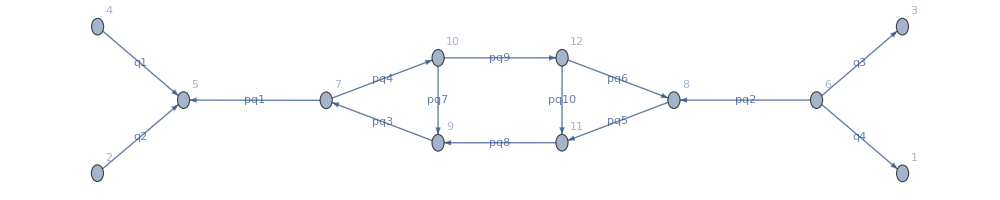

```mathematica
GetSuperGraph[SGYAMLinfo,ShowVertexLabels->Automatic,Size->1000]
```

And all of its LMBs

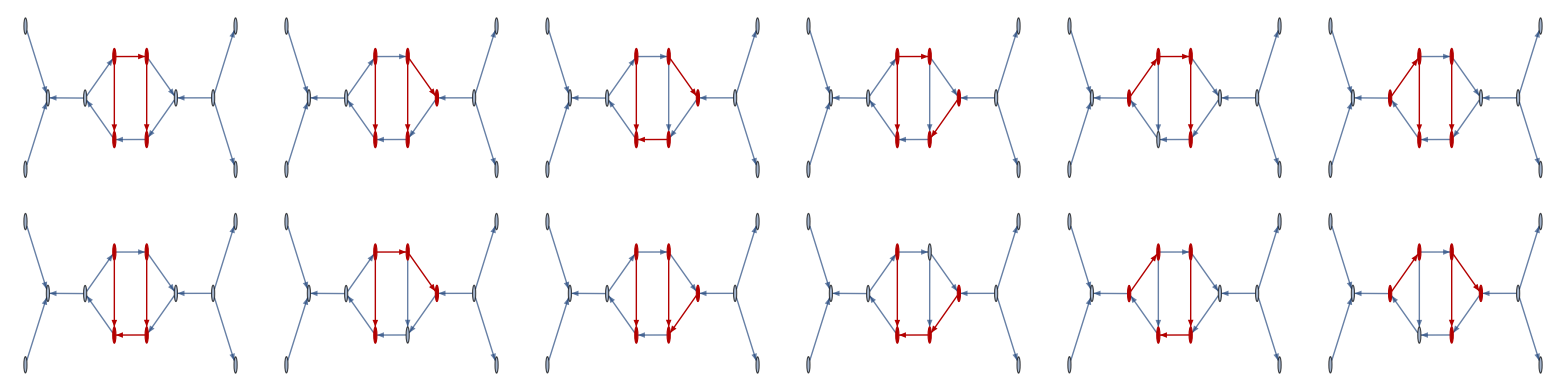

```mathematica
Table[HighlightGraph[GetSuperGraph[SGYAMLinfo],lmb],{lmb, GenerateAllLMBs[SGYAMLinfo]⟦;;12⟧}]//Multicolumn[#,6]&
```

We can automatically generate all E-surfaces (the only slow part is finding whether or not points exists on them)

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->Hyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
```

And display them:

All 9 s-channel E-surfaces:

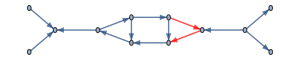
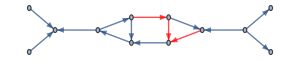
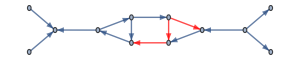
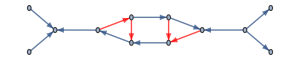
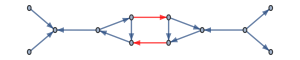
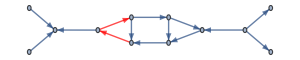
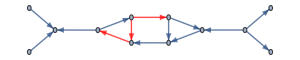
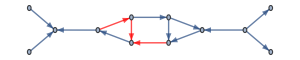
ID 1: | -Graphics- | ID 3: | -Graphics- | ID 5: | -Graphics- | ID 7: | -Graphics- | ID 9: | -Graphics-
ID 2: | -Graphics- | ID 4: | -Graphics- | ID 6: | -Graphics- | ID 8: | -Graphics- |

All 6 soft E-surfaces:

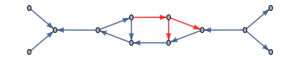
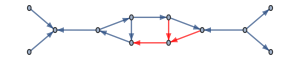
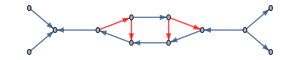
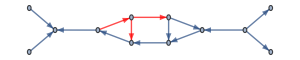
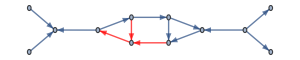
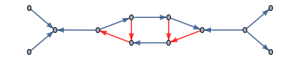
ID 1: | -Graphics- | ID 3: | -Graphics- | ID 5: | -Graphics- |  | 
ID 2: | -Graphics- | ID 4: | -Graphics- | ID 6: | -Graphics- |  |

All 7 internal E-surfaces:

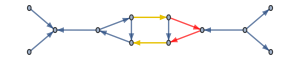
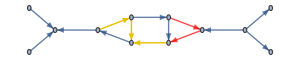
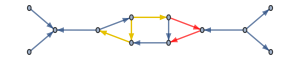
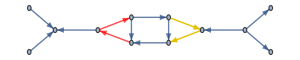
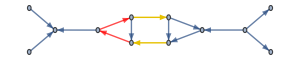
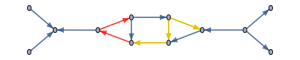
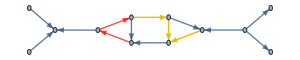
ID 1: | -Graphics- | ID 3: | -Graphics- | ID 5: | -Graphics- | ID 7: | -Graphics- | 
ID 2: | -Graphics- | ID 4: | -Graphics- | ID 6: | -Graphics- |  |

All 4 composite E-surfaces:

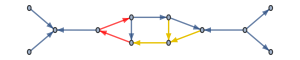
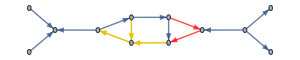
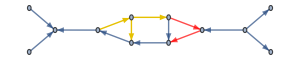
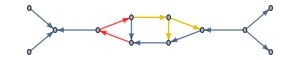
ID 1: | -Graphics- | ID 2: | -Graphics- | ID 3: | -Graphics- | ID 4: | -Graphics- |

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Size->300,Colors->{Red}]
```

Or just one particular one

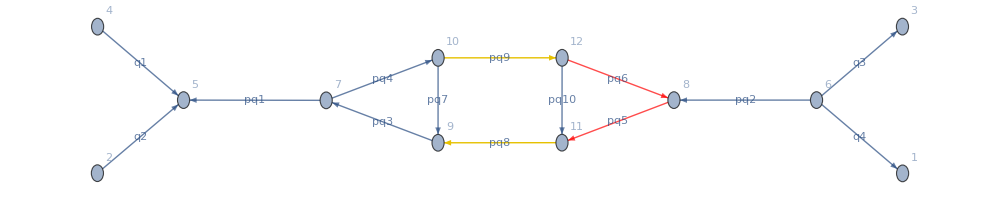

```mathematica
DisplayESurface[SGYAMLinfo,allESurfaces["internal"]⟦1⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

And access a wealth of information about each, e.g.:

```mathematica
MyDataset[allESurfaces["s-channel"]⟦3⟧]
```

We can build a helper association to directly access Cutkosky cut E-surfaces.

```mathematica
CutkoskyEsurfaces=Association[Table[es["OutgoingEdges"]->es,{es,allESurfaces["s-channel"]}]];
```

And easily find a point on (multiple) E-surfaces as follows:

```mathematica
aPointToExplore=FindPointOnEsurfaces[{CutkoskyEsurfaces[{"pq4","pq3"}],CutkoskyEsurfaces[{"pq5","pq6"}]},SGYAMLinfo,Hyperparams,DEBUG->False,AcceptThreshold->10^-25]
```

<|pq4→{-369.6512013372561213994587,276.5261967769529778957255,-83.44010933596155557008353},pq6→{431.2233839198687652239635,178.7049973993773098480702,46.71099512091363448117113},pq9→{-211.3900503914457019882351,4.2063076095350938552246,-156.6475485949850256603654}|>

And we can verify that it is indeed located on these three E-surfaces

```mathematica
MyDataset[Association[Table[e->CutkoskyEsurfaces[e]["Eq"]/.GenerateLoopMomenta[SGYAMLinfo,moms->aPointToExplore],{e,Keys[CutkoskyEsurfaces]}]]]
```

Look at all momenta for this configuration:

```mathematica
ComputeAllMomenta[aPointToExplore,SGYAMLinfo,Hyperparams,DatasetOutput->True]
```

```mathematica
ints=FindExistingIntersections[<|"s-channel"->allESurfaces["s-channel"]|>,SGYAMLinfo,Hyperparams,MaxNEsurfaces->5];
```

```mathematica
Association[Table[n->Length[ints[n]],{n,Keys[ints]}]]
```

<|1→9,2→22,3→19,4→7,5→1|>

```mathematica
ints[5]
```

{{{{s-channel,1},{s-channel,2},{s-channel,3},{s-channel,5},{s-channel,9}},<|pq4→{415.9740193155329,64.54527647454107,207.0519802834682},pq6→{-116.2107629011054,441.9232958396661,-106.1595929727975},pq9→{-116.2107629011053,441.9232958396661,-106.1595929727975}|>}}

### Algebraic subtraction of the cFF expression

#### Graph Construction

```mathematica
EdgeIDtoNameMap=<|
1->"q1","q1"->1,
2->"q2","q2"->2,
3->"q3","q3"->3,
4->"q4","q4"->4,
5->"pq1","pq1"->5,
6->"pq2","pq2"->6,
7->"pq3","pq3"->7,
8->"pq4","pq4"->8,
9->"pq5","pq5"->9,
10->"pq6","pq6"->10,
11->"pq7","pq7"->11,
12->"pq8","pq8"->12,
13->"pq9","pq9"->13,
14->"pq10","pq10"->14
|>;
```

```mathematica
EdgeNameToMassMap=Association[Table[prop["name"]->PDGtoMasses[prop["PDG"]],{prop,SGYAMLinfo["propagators"]}]];
EdgeNameToMassMap=Join[EdgeNameToMassMap,Association[Table[e⟦1⟧->0.,{e,Select[SGYAMLinfo["topo_edges"],Not[MemberQ[Keys[EdgeNameToMassMap],#⟦1⟧]]&]}]]];
```

```mathematica
StrippedSG=MakeAllExternalLegsIncoming[GetSuperGraph[SGYAMLinfo]];
SG=AssignSignatures[StrippedSG,
masses->Association[Table[EdgeIDtoNameMap[e⟦1⟧]->EdgeNameToMassMap[e⟦1⟧],{e,SGYAMLinfo["topo_edges"]}]],
lmb->Table[EdgeIDtoNameMap[e],{e,SGYAMLinfo["loop_momentum_basis"]}]
];
```

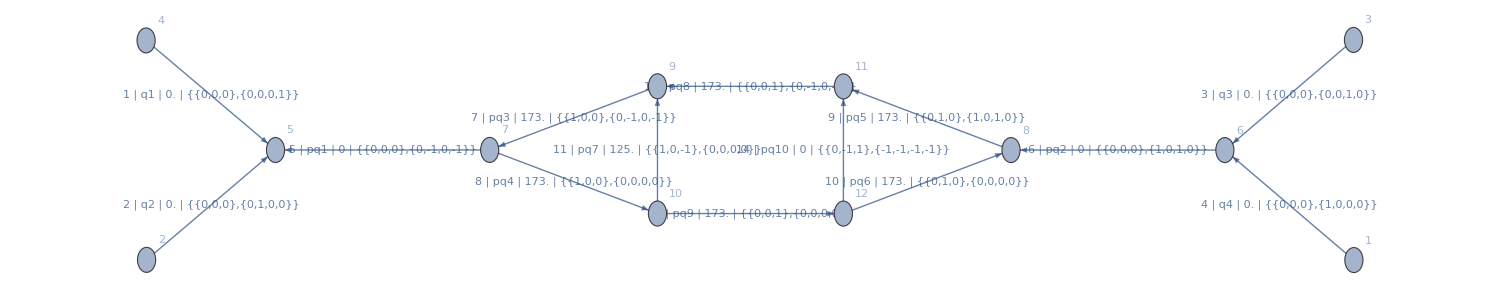

```mathematica
ShowGraph[SG,size->1500,edgeIDMap->EdgeIDtoNameMap]
```

```mathematica
(*CrossFreeFamilyLTD[SG,ConvertToNormalisedFormat->True,Orientations->{{True,True,True,True,True,False,True,True,False,False}},DEBUG->True]*)
```

```mathematica
SGCFF=CrossFreeFamilyLTD[SG,ConvertToNormalisedFormat->True];
SGCFFExplicit=CrossFreeFamilyLTD[SG,ConvertToNormalisedFormat->False,wrapEtaDefinitions->True];
```

```mathematica
ESurfacesEdgeIDsMap=GetEsurfacesToEdgeIdsMap[allESurfaces,EdgeIDtoNameMap,{"s-channel","soft"}];
```

#### Example of applications of various core functions

Automatically assign the shift for a cut based on the SG and a CFF orientation

```mathematica
AssignShiftToCut[SG,(*{12,13}*){7,11,14,10},
BuildOrientationMap[SG,SGCFFExplicit⟦4⟧],
<|
1->p1E,
2->p2E,
3->p3E,
4->p4E
|>
]
```

-p1E-p2E

Example of one CFF term

```mathematica
SGCFFExplicit⟦4⟧
```

{{True,True,True,True,True,False,True,False,False,False},((1/(eta[{12,13}] eta[{10,13,14}])+1/(eta[{10,13,14}] eta[{8,10,11,14}]))/(eta[{5}] eta[{8,11,12}])+1/(eta[{5}] eta[{10,13,14}] eta[{7,10,11,14}] eta[{8,10,11,14}]))/(eta[{6}] eta[{9,10}] eta[{7,11,12}])}

Which we can dress with shifts easily using `SubstituteShiftInCFFTerm`.

```mathematica
SubstituteShiftInCFFTerm[SG,SGCFFExplicit⟦4⟧,<|1->p1E,2->p2E,3->p3E,4->-p1E-p2E-p3E|>]
SubstituteShiftInCFFTerm[SG,SGCFFExplicit⟦4⟧,<|1->p1E,2->p2E,3->p3E,4->-p1E-p2E-p3E|>,NumericalExternals->{p1E->1,p2E->1,p3E->-1}]
```

{{True,True,True,True,True,False,True,False,False,False},((1/(eta[{12,13},p1E+p2E] eta[{10,13,14},0])+1/(eta[{10,13,14},0] eta[{8,10,11,14},0]))/(eta[{5},-p1E-p2E] eta[{8,11,12},p1E+p2E])+1/(eta[{5},-p1E-p2E] eta[{10,13,14},0] eta[{7,10,11,14},-p1E-p2E] eta[{8,10,11,14},0]))/(eta[{6},-p1E-p2E] eta[{9,10},-p1E-p2E] eta[{7,11,12},0])}

{{True,True,True,True,True,False,True,False,False,False},((1/(eta[{12,13},+,p1E+p2E] eta[{10,13,14},s,0])+1/(eta[{10,13,14},s,0] eta[{8,10,11,14},s,0]))/(eta[{5},-,-p1E-p2E] eta[{8,11,12},+,p1E+p2E])+1/(eta[{5},-,-p1E-p2E] eta[{10,13,14},s,0] eta[{7,10,11,14},-,-p1E-p2E] eta[{8,10,11,14},s,0]))/(eta[{6},-,-p1E-p2E] eta[{9,10},-,-p1E-p2E] eta[{7,11,12},s,0])}

Alternatively one can also use `SubstituteEsurfInCFFTerm` to dress the shifts using the momentum signature of each edge

```mathematica
SubstituteEsurfInCFFTerm[SG,SGCFFExplicit⟦4⟧,ESurfacesEdgeIDsMap,{-3/4,3/4,-1/4,1/4}]⟦2⟧
```

((1/(eta[s-channel,9,-1] eta[soft,1,0])+1/(eta[soft,1,0] eta[soft,5,0]))/(eta[s-channel,6,-1] OSE[5])+1/(eta[s-channel,8,1] eta[soft,1,0] eta[soft,5,0] OSE[5]))/(eta[s-channel,1,1] eta[soft,4,0] OSE[6])

The collectEssurface function is useful to gather all denominators showing up in an expression

```mathematica
CollectEsurfaces[((1/AAA+1/BBB)/CCC+1/DDD+1/AAA)/EEE]
```

{AAA,BBB,CCC,DDD,EEE}

And particular combinations can easily be removed using `RemoveTermsWithoutEsurfContributionsFrom`

```mathematica
RemoveTermsWithoutEsurfContributionsFrom[{CCC,EEE},((1/AAA+1/BBB)/CCC+1/DDD)/EEE]
```

(1/AAA+1/BBB)/(CCC EEE)

This graph factorization is helpful to later apply the algebraic subtraction, you can find below what it looks like

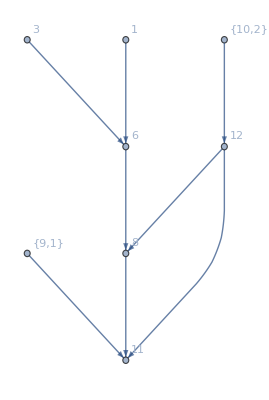
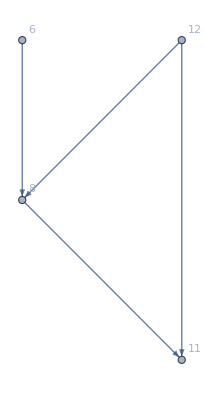
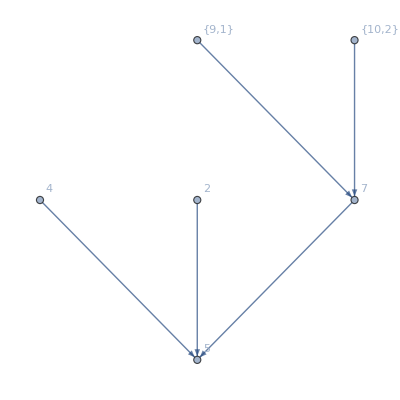
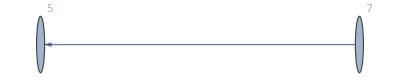
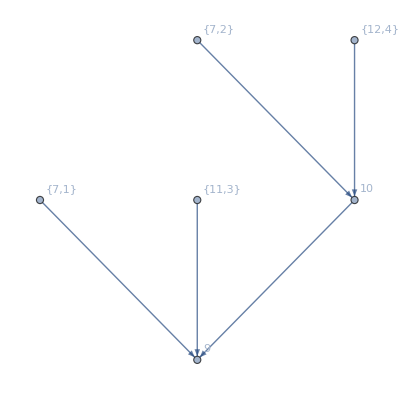
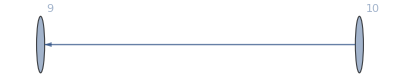
{<|graph→-Graphics-,graphNoHalfEdges→-Graphics-,internalEdgeIDs→{6,9,10,14},internalTreeEdgeIDs→{6},internalLoopEdgeIDs→{9,10,14},orientation→{True,True,False,False},orientationMap→<|3→False,4→False,6→True,9→True,10→False,12→False,13→True,14→False|>,external_sign_wrt_incoming→<|12→-1,3→1,4→1,13→1|>|>,<|graph→-Graphics-,graphNoHalfEdges→-Graphics-,internalEdgeIDs→{5},internalTreeEdgeIDs→{5},internalLoopEdgeIDs→{},orientation→{True},orientationMap→<|1→False,2→False,5→True,7→True,8→True|>,external_sign_wrt_incoming→<|8→-1,1→1,2→1,7→1|>|>,<|graph→-Graphics-,graphNoHalfEdges→-Graphics-,internalEdgeIDs→{11},internalTreeEdgeIDs→{11},internalLoopEdgeIDs→{},orientation→{False},orientationMap→<|7→True,8→True,11→False,12→False,13→True|>,external_sign_wrt_incoming→<|7→-1,13→-1,8→1,12→1|>|>}

```mathematica
FGtest=FactorizeGraph[SG,SGCFFExplicit⟦4⟧,
Table[
GetEdgeId[GetMatchingEdge[EdgeList[SG],e]]
,{e,Join@@Table[Flatten[esurf["edges"]],{esurf,
{allESurfaces["s-channel"]⟦2⟧,allESurfaces["s-channel"]⟦9⟧}
}]}]
]
```

Then the cross-free family of each bit of the graph can be nicely computed individually, e.g.

Now considering orientation: {-1}

------------------------------------------------------------

Now considering the following graph:

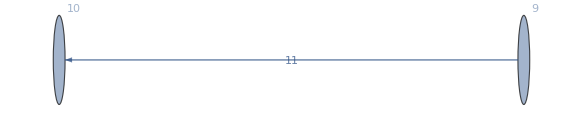

Reached termination condition, returning Esurf:{11}

Now considering orientation: {1}

------------------------------------------------------------

Now considering the following graph:

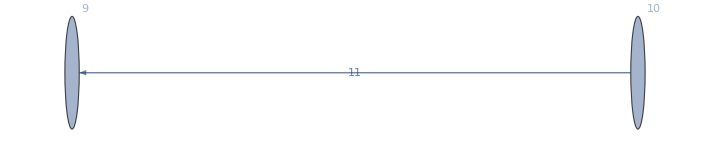

Reached termination condition, returning Esurf:{11}

{{{True},1/OSE[11]},{{False},1/OSE[11]}}

```mathematica
CrossFreeFamilyLTD[FGtest⟦3⟧["graph"],ConvertToNormalisedFormat->False,DEBUG->True]
```

Ok this function is actually not useful then :P

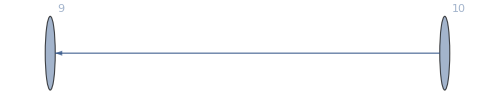

```mathematica
GetGraphBetweenEsurfaces[SG,allESurfaces["s-channel"]⟦2⟧,allESurfaces["s-channel"]⟦9⟧,1,2]
```

Now let’s apply the subtraction building block to one particular orientation (#71) which has a double-real cut, and let’s immediately assign the shifts with particular Energy signs so that we can get a differentiation of the E-surfaces that can possibly exist (labeled with “-“) and those which don’t (labeled with “+“).

```mathematica
CFFTermToTest=SubstituteShiftInCFFTerm[
SG,SGCFFExplicit⟦71⟧,
<|1->p1E,2->p2E,3->p3E,4->-p1E-p2E-p3E|>,
NumericalExternals->{p1E->1,p2E->1,p3E->-1}
]
```

{{True,True,False,True,True,True,False,True,False,True},(1/(eta[{5},-,-p1E-p2E] eta[{7,8},-,-p1E-p2E] eta[{12,13},-,-p1E-p2E] eta[{8,11,12},-,-p1E-p2E])+1/(eta[{5},-,-p1E-p2E] eta[{7,8},-,-p1E-p2E] eta[{8,11,12},-,-p1E-p2E] eta[{8,9,11,14},-,-p1E-p2E]))/(eta[{6},-,-p1E-p2E] eta[{9,10},-,-p1E-p2E] eta[{9,13,14},-,-p1E-p2E])}

With this representation, notice that one can at any point write it entirely in terms of OSE and shifts directly with `SubstituteEsurfToOSE`.

```mathematica
SubstituteEsurfToOSE[
CFFTermToTest,
etas->{eta,etaApprox,etaDef,etaDefApprox,etaProp},keepEtas->False
]
```

{{True,True,False,True,True,True,False,True,False,True},(1/((-p1E-p2E+OSE[5]) (-p1E-p2E+OSE[7]+OSE[8]) (-p1E-p2E+OSE[8]+OSE[11]+OSE[12]) (-p1E-p2E+OSE[12]+OSE[13]))+1/((-p1E-p2E+OSE[5]) (-p1E-p2E+OSE[7]+OSE[8]) (-p1E-p2E+OSE[8]+OSE[11]+OSE[12]) (-p1E-p2E+OSE[8]+OSE[9]+OSE[11]+OSE[14])))/((-p1E-p2E+OSE[6]) (-p1E-p2E+OSE[9]+OSE[10]) (-p1E-p2E+OSE[9]+OSE[13]+OSE[14]))}

Or even keeping the Eta notation for easy labeling later on (the last entry is not the full expression and not the shift, so that “expr” is used to signal this difference

```mathematica
SubstituteEsurfToOSE[
CFFTermToTest,
etas->{eta,etaApprox,etaDef,etaDefApprox,etaProp},keepEtas->True
]
```

{{True,True,False,True,True,True,False,True,False,True},(1/(eta[{5},-,expr,-p1E-p2E+OSE[5]] eta[{7,8},-,expr,-p1E-p2E+OSE[7]+OSE[8]] eta[{12,13},-,expr,-p1E-p2E+OSE[12]+OSE[13]] eta[{8,11,12},-,expr,-p1E-p2E+OSE[8]+OSE[11]+OSE[12]])+1/(eta[{5},-,expr,-p1E-p2E+OSE[5]] eta[{7,8},-,expr,-p1E-p2E+OSE[7]+OSE[8]] eta[{8,11,12},-,expr,-p1E-p2E+OSE[8]+OSE[11]+OSE[12]] eta[{8,9,11,14},-,expr,-p1E-p2E+OSE[8]+OSE[9]+OSE[11]+OSE[14]]))/(eta[{6},-,expr,-p1E-p2E+OSE[6]] eta[{9,10},-,expr,-p1E-p2E+OSE[9]+OSE[10]] eta[{9,13,14},-,expr,-p1E-p2E+OSE[9]+OSE[13]+OSE[14]])}

Let us try now to Compute the T approximation operator on the three defining E-surface of the the double-real emission singularity:

```mathematica
TopRes=Toperator[
SG,
{
{{7,8},"-",__},
{{8,11,12},"-",__},
{{8,9,11,14},"-",__}
},
CFFTermToTest,
DEBUG->False
]
```

1/(etaApprox[{9,10},-,-OSE[8]-OSE[9]-OSE[11]-OSE[14]] etaApprox[{9,13,14},-,-OSE[8]-OSE[9]-OSE[11]-OSE[14]] etaDef[{7,8},-,-p1E-p2E] etaDef[{8,11,12},-,-p1E-p2E] etaDef[{8,9,11,14},-,-p1E-p2E] etaProp[{5},-,-p1E-p2E] etaProp[{6},-,-p1E-p2E])

Which, once again, can be written directly in terms of OSEs but keeping the eta notation

```mathematica
SubstituteEsurfToOSE[
TopRes
,etas->{eta,etaApprox,etaDef,etaDefApprox,etaProp},keepEtas->True
]
```

1/(etaApprox[{9,10},-,expr,-OSE[8]+OSE[10]-OSE[11]-OSE[14]] etaApprox[{9,13,14},-,expr,-OSE[8]-OSE[11]+OSE[13]] etaDef[{7,8},-,expr,-p1E-p2E+OSE[7]+OSE[8]] etaDef[{8,11,12},-,expr,-p1E-p2E+OSE[8]+OSE[11]+OSE[12]] etaDef[{8,9,11,14},-,expr,-p1E-p2E+OSE[8]+OSE[9]+OSE[11]+OSE[14]] etaProp[{5},-,expr,-p1E-p2E+OSE[5]] etaProp[{6},-,expr,-p1E-p2E+OSE[6]])

We can construct the explicit expression of the E-surfaces as follows:

```mathematica
explicitEsurfaceEquationsToTest=SubstituteEsurfToOSE[(eta@@#)&/@{
{{7,8},"-",-p1E-p2E},
{{8,11,12},"-",-p1E-p2E},
{{8,9,11,14},"-",-p1E-p2E}
}]
```

{-p1E-p2E+OSE[7]+OSE[8],-p1E-p2E+OSE[8]+OSE[11]+OSE[12],-p1E-p2E+OSE[8]+OSE[9]+OSE[11]+OSE[14]}

And use them in a function that I identifies remaining limits by applying “Together” to the expression and performing numerator vs denominator simplification

```mathematica
IdentifyLimits[
explicitEsurfaceEquationsToTest,
SubstituteEsurfToOSE[CFFTermToTest⟦2⟧-TopRes],
deltas->{Δ[1],Δ[2],Δ[3]},
deltasOnly->True
]
```

{{Δ[1],Δ[2]}}

The above confirms that the 1/(Δ1 Δ2 Δ3) singularity is gone, and we’re only left with a subleading one here.

Alternatively one can get a similar conclusion from applying a Taylor series:

```mathematica
ComputeAsymptoticLimit[
explicitEsurfaceEquationsToTest,
SubstituteEsurfToOSE[CFFTermToTest⟦2⟧-TopRes],
variablesToSolvePattern->OSE[7|11|14](*OSE[_Integer]*),
deltas->{Δ[1],Δ[2],Δ[3]},
extraDepths->{1,1,1},
deltasOnly->False,
DEBUG->True
]//Expand//Collect[#,{Δ[1]Δ[2]Δ[3]}]&
```

Solving system:

{-p1E-p2E+OSE[7]+OSE[8],-p1E-p2E+OSE[8]+OSE[11]+OSE[12],-p1E-p2E+OSE[8]+OSE[9]+OSE[11]+OSE[14]}=={Δ[1],Δ[2],Δ[3]}

In variables:

{OSE[7],OSE[11],OSE[14]}

Solution found for approach: {OSE[7] -> p1E + p2E - OSE[8] + Δ[1], OSE[11] -> p1E + p2E - OSE[8] - OSE[12] + Δ[2], OSE[14] -> -OSE[9] + OSE[12] - Δ[2] + Δ[3]}

Taylor arguments for expansion:

{-1/((-p1E-p2E+OSE[5]) (-p1E-p2E+OSE[6]) Δ[1] (-p1E-p2E+OSE[12]+OSE[13]-Δ[2]) Δ[2] (-p1E-p2E+OSE[9]+OSE[10]-Δ[3]) Δ[3])+(1/((-p1E-p2E+OSE[5]) (-p1E-p2E+OSE[12]+OSE[13]) Δ[1] Δ[2])+1/((-p1E-p2E+OSE[5]) Δ[1] Δ[2] Δ[3]))/((-p1E-p2E+OSE[6]) (-p1E-p2E+OSE[9]+OSE[10]) (-p1E-p2E+OSE[12]+OSE[13]-Δ[2]+Δ[3])),{Δ[1],0,0},{Δ[2],0,0},{Δ[3],0,0}}

-(2 p1E)/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])-(2 p2E)/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])+OSE[9]/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])+OSE[10]/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])+OSE[12]/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])+OSE[13]/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13])^3 Δ[1])+1/((p1E+p2E-OSE[5]) (p1E+p2E-OSE[6]) (p1E+p2E-OSE[9]-OSE[10])^2 (p1E+p2E-OSE[12]-OSE[13]) Δ[1] Δ[2])

But with deltasOnly->True, it’s easier to immediately be able to read off the singularity left

```mathematica
ComputeAsymptoticLimit[
explicitEsurfaceEquationsToTest,
SubstituteEsurfToOSE[CFFTermToTest⟦2⟧-TopRes],
variablesToSolvePattern->OSE[7|11|14](*OSE[_Integer]*),
deltas->{Δ[1],Δ[2],Δ[3]},
extraDepths->{1,1,1},
deltasOnly->True,
DEBUG->False
]
```

{{Δ[1]},{Δ[1],Δ[2]}}

#### Full subtraction of the double-real emission sector of the corresponding orientation #71

First dress with shifts the CFF term we want to test:

```mathematica
CFFTermToTest=SubstituteShiftInCFFTerm[
SG,SGCFFExplicit⟦71⟧,
<|1->p1E,2->p2E,3->p3E,4->-p1E-p2E-p3E|>,
NumericalExternals->{p1E->1,p2E->1,p3E->-1}
]
```

{{True,True,False,True,True,True,False,True,False,True},(1/(eta[{5},-,-p1E-p2E] eta[{7,8},-,-p1E-p2E] eta[{12,13},-,-p1E-p2E] eta[{8,11,12},-,-p1E-p2E])+1/(eta[{5},-,-p1E-p2E] eta[{7,8},-,-p1E-p2E] eta[{8,11,12},-,-p1E-p2E] eta[{8,9,11,14},-,-p1E-p2E]))/(eta[{6},-,-p1E-p2E] eta[{9,10},-,-p1E-p2E] eta[{9,13,14},-,-p1E-p2E])}

We can compute directly a Z subtraction term, assigning a “tag” for this sector, i.e. a list of name for each defining E-surface

```mathematica
ZResult=Zoperator[SG,
{
{{7,8},"-",__},
{{8,11,12},"-",__},
{{8,9,11,14},"-",__}
},
{2,6},
CFFTermToTest,
Tag->{2,6,9},
DEBUG->False,
MinNEsurfToSubtract->1,
ComputeSubtraction->True
];
ZResult["T_substitutions"]//Dataset
ZResult["expression"]
```

T[{{2,6}}]-T[{{2,6},{2,6,9}}]

And as usual directly write the terms using OSEs and shift only (except for the etaProp, which is nice to keep factorized)

```mathematica
SubstituteEsurfToOSE[
ZResult["T_substitutions"],etas->{eta,etaApprox,etaDef,etaDefApprox},keepEtas->False
]//Dataset
```

But of course, even better, we can also directly compute the full algebraic subtraction forest:

```mathematica
forestResult=SubtractForest[
SG,
{
{{7,8},"-",__},
{{8,11,12},"-",__},
{{8,9,11,14},"-",__}
},
CFFTermToTest,
Tag->{2,6,9},
DEBUG->False,
MinNEsurfToSubtract->1,
ComputeSubtraction->True
];
forestResult["expression"]
forestResult["Z_substitutions"]//Dataset
forestResult["T_substitutions"]//Dataset
```

Z[{2}]+Z[{6}]+Z[{9}]+Z[{2,6}]+Z[{2,9}]+Z[{6,9}]+Z[{2,6,9}]

We can now check what is the evaluation of all these Z operators:

```mathematica
Table[{z,SubstituteEsurfToOSE[
((z)/.forestResult["Z_substitutions"])/.forestResult["T_substitutions"]
]},{z,{
Z[{6}],
Z[{9}],
Z[{6,9}],
Z[{2,9}],
Z[{2,6,9}],
Z[{2,6}],
Z[{2}]
}}]//Dataset
```

And as it turns out, in this case, the sum of all Z operators gives the original graph:

```mathematica
SubstituteEsurfToOSE[
CFFTermToTest⟦2⟧-
(forestResult["expression"]/.forestResult["Z_substitutions"])/.forestResult["T_substitutions"]
]
```

0

We can however test How the residual singularities get progressively removed as we subtract more Z operators

```mathematica
Table[{zs,IdentifyLimits[

SubstituteEsurfToOSE[(eta@@#)&/@{
{{7,8},"-",-p1E-p2E},
{{8,11,12},"-",-p1E-p2E},
{{8,9,11,14},"-",-p1E-p2E}
}],

SubstituteEsurfToOSE[
CFFTermToTest⟦2⟧-
((zs)/.forestResult["Z_substitutions"])/.forestResult["T_substitutions"]
],
variablesToSolvePattern->OSE[8|9|11](*OSE[_Integer]*),
deltas->{Δ[1],Δ[2],Δ[3]},
extraDepths->{1,1,1},
deltasOnly->True,
DEBUG->False
]},{ zs,
{
Z[{2,6,9}],
Z[{2,6,9}]+Z[{2,6}],
Z[{2,6,9}]+Z[{2,6}]+Z[{2}]
}
}]//Dataset
```

## e^+ e^- → ϕ d d̄ | Triangle Box Triangle (NLO)

### Preamble (general information needed for all sections)

```mathematica
SGYAMLinfo=<|"FORM_integrand"-><|"call_signature"-><|"id"->2|>|>,"cutkosky_cuts"->{<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq3","parametric_shift"->{{1,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{0,1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq10pq5pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{0,0,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{0,1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->8|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq10pq5pq7_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{1,0,0,0,0,1,0,1,1},"cuts"->{<|"m_squared"->0.,"name"->"pq4","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,-1,1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq5","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{0,1,0},{-1,-1,0,0}}|>,<|"m_squared"->0.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->-1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->0,"lmb_to_cb"->{1,0,0,0,-1,1,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","parametric_shift"->{{0,0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{1,1,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->12|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq6pq10pq3pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{1,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{1,1,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->9|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq6pq10pq3pq7_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,1,1,0,0,1,1,0},"cuts"->{<|"m_squared"->0.,"name"->"pq6","particle_id"->2,"power"->1,"sign"->1,"signature"->{{0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,-1,1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq3","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,0,0},{-1,-1,0,0}}|>,<|"m_squared"->0.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->1,"lmb_to_cb"->{0,1,0,0,-1,1,1,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","parametric_shift"->{{0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->10|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq9pq3pq7_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{1,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{-1,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->8|>},"loop_momentum_map"->{{{0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG6_pq9pq3pq7_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,0},{-1,-1,0,0}},"amp_sig"->{1},"id"->0,"lmb_sig"->{{0,1,0},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->1,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->2,"lmb_sig"->{{0,-1,1},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->3,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->5,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{5,3},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{3,3},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{0,1,0,0,0,1,1,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq9","particle_id"->2,"power"->1,"sign"->1,"signature"->{{0,0,1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq3","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,0,0},{-1,-1,0,0}}|>,<|"m_squared"->0.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->1,"signature"->{{1,0,-1},{0,0,0,0}}|>},"id"->2,"lmb_to_cb"->{0,0,1,1,0,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq3","parametric_shift"->{{1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG6_pq4pq7pq8_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->8|>},"loop_momentum_map"->{{{0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG6_pq4pq7pq8_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,0},{-1,-1,0,0}},"amp_sig"->{1},"id"->0,"lmb_sig"->{{0,1,0},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->1,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->2,"lmb_sig"->{{0,-1,1},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->3,"lmb_sig"->{{0,1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->5,"lmb_sig"->{{0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{5,3},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{1.},"foci"->{3,3},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{1,0,0,0,0,1,1,-1,0},"cuts"->{<|"m_squared"->0.,"name"->"pq4","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->-1,"signature"->{{1,0,-1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq8","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{0,0,1},{-1,-1,0,0}}|>},"id"->3,"lmb_to_cb"->{1,0,0,1,0,-1,0,1,0}|>},"default_fixed_cut_momenta"->{{},{}},"e_cm_squared"->1.*10^6,"edge_PDGs"->{{"q1",-11},{"q2",11},{"q3",-11},{"q4",11},{"pq1",22},{"pq2",22},{"pq3",2},{"pq4",2},{"pq5",2},{"pq6",2},{"pq7",1337},{"pq8",2},{"pq9",2},{"pq10",21}},"edge_signatures"-><|"pq1"->{{0,0,0},{-1,-1,0,0}},"pq10"->{{0,-1,1},{0,0,0,0}},"pq2"->{{0,0,0},{-1,-1,0,0}},"pq3"->{{1,0,0},{-1,-1,0,0}},"pq4"->{{1,0,0},{0,0,0,0}},"pq5"->{{0,1,0},{-1,-1,0,0}},"pq6"->{{0,1,0},{0,0,0,0}},"pq7"->{{1,0,-1},{0,0,0,0}},"pq8"->{{0,0,1},{-1,-1,0,0}},"pq9"->{{0,0,1},{0,0,0,0}},"q1"->{{0,0,0},{1,0,0,0}},"q2"->{{0,0,0},{0,1,0,0}},"q3"->{{0,0,0},{0,0,1,0}},"q4"->{{0,0,0},{0,0,0,1}}|>,"external_momenta"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_momentum_basis"->{"pq4","pq6","pq9"},"multi_channeling_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->0,"defining_propagator_masses"->{0.,173.,125.},"defining_propagators"->{"pq10","pq5","pq7"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{0,-1,1},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->1,"defining_propagator_masses"->{0.,173.,125.},"defining_propagators"->{"pq10","pq3","pq7"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{0,-1,1},{0,0,0,0}},{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->2,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq3","pq7","pq6"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,1,0},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->2,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq3","pq7","pq5"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq8","pq10"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,173.},"defining_propagators"->{"pq7","pq8","pq6"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->3,"defining_propagator_masses"->{125.,173.,173.},"defining_propagators"->{"pq7","pq8","pq5"},"defining_propagators_powers"->{1,1,1},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}}}|>},"multi_channeling_lmb_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq9","pq10"},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq6","pq7","pq10"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq6","pq7","pq9"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq5","pq7","pq10"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq5","pq7","pq9"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.},"defining_propagators"->{"pq7","pq8","pq10"},"signatures"->{{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq5","pq7","pq8"},"signatures"->{{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.},"defining_propagators"->{"pq6","pq7","pq8"},"signatures"->{{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq9","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq9"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq9"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq4","pq8","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq8"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq8"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq4","pq7","pq10"},"signatures"->{{{1,0,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq4","pq6","pq7"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq4","pq5","pq7"},"signatures"->{{{1,0,0},{0,0,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq9"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq9"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.},"defining_propagators"->{"pq3","pq8","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq8"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq8"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{0,0,1},{-1,-1,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.},"defining_propagators"->{"pq3","pq7","pq10"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}},{{0,-1,1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq3","pq5","pq7"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{-1,-1,0,0}},{{1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.},"defining_propagators"->{"pq3","pq6","pq7"},"signatures"->{{{1,0,0},{-1,-1,0,0}},{{0,1,0},{0,0,0,0}},{{1,0,-1},{0,0,0,0}}}|>},"n_incoming_momenta"->2,"n_loops"->3,"name"->"SG_QG6","optimal_channel_ids"->{1},"overall_numerator"->1.,"propagators"->{<|"PDG"->22,"m_squared"->0.,"name"->"pq1","power"->1,"signature"->{{0,0,0},{-1,-1,0,0}},"vertices"->{7,5}|>,<|"PDG"->22,"m_squared"->0.,"name"->"pq2","power"->1,"signature"->{{0,0,0},{-1,-1,0,0}},"vertices"->{6,8}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq3","power"->1,"signature"->{{1,0,0},{-1,-1,0,0}},"vertices"->{9,7}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq4","power"->1,"signature"->{{1,0,0},{0,0,0,0}},"vertices"->{7,10}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq5","power"->1,"signature"->{{0,1,0},{-1,-1,0,0}},"vertices"->{8,11}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq6","power"->1,"signature"->{{0,1,0},{0,0,0,0}},"vertices"->{12,8}|>,<|"PDG"->1337,"m_squared"->0.,"name"->"pq7","power"->1,"signature"->{{1,0,-1},{0,0,0,0}},"vertices"->{10,9}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq8","power"->1,"signature"->{{0,0,1},{-1,-1,0,0}},"vertices"->{11,9}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq9","power"->1,"signature"->{{0,0,1},{0,0,0,0}},"vertices"->{10,12}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq10","power"->1,"signature"->{{0,-1,1},{0,0,0,0}},"vertices"->{12,11}|>},"topo"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq1","power"->2,"q"->{-1000.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq3","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq5","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1,0},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq7","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,-1},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq8","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,1},"start_node"->11|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,-1,1},"start_node"->8|>},"ltd_cut_structure"->{{0,0,0,1,1,-1},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,1,0,0,1,-1},{0,1,1,0,0,1},{0,1,1,0,1,0},{0,1,0,-1,0,-1},{0,1,1,-1,0,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->3,"name"->"SG_QG6"|>,"topo_edges"->{{"q1",4,5,0},{"q2",2,5,0},{"q3",6,3,0},{"q4",6,1,0},{"pq1",7,5,1},{"pq2",6,8,1},{"pq3",9,7,1},{"pq4",7,10,1},{"pq5",8,11,1},{"pq6",12,8,1},{"pq7",10,9,1},{"pq8",11,9,1},{"pq9",10,12,1},{"pq10",12,11,1}}|>;
```

Some general information is loaded here

```mathematica
GlobalECM=Total[Hyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
allCutkoskyEsurfaces=Association[Table[AlphabeticSort[es["OutgoingEdges"]]->es,{es,allESurfaces["s-channel"]}]];
```

## e^+ e^- → H t t̄ | Triangle Box Box Triangle (NNLO)

-Graphics-

### Preamble (general information needed for all sections)

```mathematica
SGYAMLinfo=<|"FORM_integrand"-><|"call_signature"-><|"id"->0|>|>,"cutkosky_cuts"->{<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq3","parametric_shift"->{{0,0,1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{0,0,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq11","parametric_shift"->{{0,-1,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq4pq7pq5_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{-1,-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{0,0,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","parametric_shift"->{{0,-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->8|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq4pq7pq5_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq4","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq5","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,-1,-1,-1},{-1,-1,0,0}}|>},"id"->0,"lmb_to_cb"->{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","parametric_shift"->{{0,0,0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{0,0,-1,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","parametric_shift"->{{0,-1,-1,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->12|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq7pq3pq6_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{-1,-1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{0,0,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq11","parametric_shift"->{{0,-1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->9|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq7pq3pq6_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq3","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>,<|"m_squared"->29929.,"name"->"pq6","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,-1,-1,-1},{0,0,0,0}}|>},"id"->1,"lmb_to_cb"->{0,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq3","parametric_shift"->{{0,1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{0,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq13pq4pq7pq11_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{0,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","parametric_shift"->{{-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->11|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{1,-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->11|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG182_pq13pq4pq7pq11_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{-1,1,-1,0},{-1,-1,0,0}},"amp_sig"->{-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,-1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->3,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->5,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{5,4},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{4,4},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq4","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq11","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,-1,0,-1},{-1,-1,0,0}}|>},"id"->2,"lmb_to_cb"->{0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","parametric_shift"->{{1,1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{1,0,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->14|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq13pq7pq12pq3_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{1,0,1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq11","parametric_shift"->{{0,0,1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->9|>,<|"end_node"->9,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{0,0,-1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{0,0,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->9|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG182_pq13pq7pq12pq3_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,1,0},{-1,-1,0,0}},"amp_sig"->{-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->3,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->5,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{5,4},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{4,4},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{1,1,1,0,0,1,0,0,0,0,0,1,1,0,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq12","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,-1,0,-1},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq3","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>},"id"->3,"lmb_to_cb"->{0,0,0,1,0,1,0,0,1,-1,0,-1,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","parametric_shift"->{{0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->10|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq7pq3pq9_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq8","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{-1,-1},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq11","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","parametric_shift"->{{1,-1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq13","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1},"start_node"->9|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}},"ltd_cut_structure"->{{0,0,1,1},{0,-1,0,1},{0,-1,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->2,"name"->"SG_QG182_pq7pq3pq9_1"|>,"n_loops"->2,"propagators"->{<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{1,1,0,0}},"amp_sig"->{-1,-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->3,"lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{1,1,0,0}},"amp_sig"->{0,-1},"id"->4,"lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq12","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->5,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->6,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->7,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->8,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->9,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->10,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->11,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->12,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->13,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->8,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->9,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->10,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->11,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->12,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->13,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->14,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->15,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->16,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->17,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{8,7},"id"->18,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{7,7},"id"->19,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,12,10},"id"->20,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,13,10},"id"->21,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,12},"id"->22,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,13},"id"->23,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{10,10},"id"->24,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,7},"id"->25,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{7,7},"id"->26,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>}|>},"cb_to_lmb"->{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1},"cuts"->{<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq3","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>,<|"m_squared"->29929.,"name"->"pq9","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,-1,0,0},{0,0,0,0}}|>},"id"->4,"lmb_to_cb"->{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq3","parametric_shift"->{{1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq4pq7pq8_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->13,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","parametric_shift"->{{1,-1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{-1,-1},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq11","parametric_shift"->{{-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq13","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1},"start_node"->13|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}},"ltd_cut_structure"->{{0,0,1,1},{0,-1,0,1},{0,-1,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->2,"name"->"SG_QG182_pq4pq7pq8_1"|>,"n_loops"->2,"propagators"->{<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"amp_sig"->{-1,-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"amp_sig"->{0,-1},"id"->3,"lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->4,"lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq12","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->5,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->6,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->7,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->8,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->9,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->10,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->173.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->11,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->12,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->173.,"name"->"pq11","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->13,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->8,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->9,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->10,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->11,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->12,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->13,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->14,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->15,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->16,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->17,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{8,7},"id"->18,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{7,7},"id"->19,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,12,10},"id"->20,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,13,10},"id"->21,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,12},"id"->22,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,13},"id"->23,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{10,10},"id"->24,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,7},"id"->25,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{7,7},"id"->26,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>}|>},"cb_to_lmb"->{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},"cuts"->{<|"m_squared"->29929.,"name"->"pq4","particle_id"->6,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->25,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->29929.,"name"->"pq8","particle_id"->6,"power"->1,"sign"->-1,"signature"->{{1,-1,0,0},{-1,-1,0,0}}|>},"id"->5,"lmb_to_cb"->{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1}|>},"default_fixed_cut_momenta"->{{},{}},"e_cm_squared"->1.*10^6,"edge_PDGs"->{{"q1",-11},{"q2",11},{"q3",-11},{"q4",11},{"pq1",22},{"pq2",22},{"pq3",6},{"pq4",6},{"pq5",6},{"pq6",6},{"pq7",25},{"pq8",6},{"pq9",6},{"pq10",21},{"pq11",6},{"pq12",6},{"pq13",21}},"edge_signatures"-><|"pq1"->{{0,0,0,0},{-1,-1,0,0}},"pq10"->{{0,0,1,0},{0,0,0,0}},"pq11"->{{1,-1,0,-1},{-1,-1,0,0}},"pq12"->{{1,-1,0,-1},{0,0,0,0}},"pq13"->{{0,0,0,1},{0,0,0,0}},"pq2"->{{0,0,0,0},{-1,-1,0,0}},"pq3"->{{1,0,0,0},{-1,-1,0,0}},"pq4"->{{1,0,0,0},{0,0,0,0}},"pq5"->{{1,-1,-1,-1},{-1,-1,0,0}},"pq6"->{{1,-1,-1,-1},{0,0,0,0}},"pq7"->{{0,1,0,0},{0,0,0,0}},"pq8"->{{1,-1,0,0},{-1,-1,0,0}},"pq9"->{{1,-1,0,0},{0,0,0,0}},"q1"->{{0,0,0,0},{1,0,0,0}},"q2"->{{0,0,0,0},{0,1,0,0}},"q3"->{{0,0,0,0},{0,0,1,0}},"q4"->{{0,0,0,0},{0,0,0,1}}|>,"external_momenta"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_momentum_basis"->{"pq4","pq7","pq10","pq13"},"multi_channeling_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->0,"defining_propagator_masses"->{0.,0.,125.,173.},"defining_propagators"->{"pq10","pq13","pq7","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->1,"defining_propagator_masses"->{0.,0.,173.,173.},"defining_propagators"->{"pq10","pq13","pq3","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,125.,173.,0.},"defining_propagators"->{"pq13","pq7","pq11","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,125.,173.,173.},"defining_propagators"->{"pq13","pq7","pq11","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,125.,173.,173.},"defining_propagators"->{"pq13","pq7","pq11","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,173.,173.,0.},"defining_propagators"->{"pq13","pq12","pq3","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,173.,173.,173.},"defining_propagators"->{"pq13","pq12","pq3","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,173.,173.,173.},"defining_propagators"->{"pq13","pq12","pq3","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq9","pq10","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq9","pq10","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq9","pq6","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq9","pq6","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq9","pq5","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq9","pq5","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->4,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq8","pq10","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq8","pq10","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,173.},"defining_propagators"->{"pq7","pq8","pq6","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,173.},"defining_propagators"->{"pq7","pq8","pq6","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,173.},"defining_propagators"->{"pq7","pq8","pq5","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,173.},"defining_propagators"->{"pq7","pq8","pq5","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->5,"defining_propagator_masses"->{125.,173.,173.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>},"multi_channeling_lmb_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,0.,173.,0.},"defining_propagators"->{"pq7","pq10","pq12","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq12","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,0.},"defining_propagators"->{"pq6","pq7","pq10","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq12","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,0.},"defining_propagators"->{"pq5","pq7","pq10","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,0.,173.,0.},"defining_propagators"->{"pq7","pq10","pq11","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq11","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq11","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,0.},"defining_propagators"->{"pq7","pq9","pq10","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq9","pq10","pq12"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq6","pq7","pq9","pq12"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq10"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq5","pq7","pq9","pq12"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq10"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq9","pq10","pq11"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq5","pq7","pq9","pq11"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq6","pq7","pq9","pq11"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq8","pq10","pq11"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq5","pq7","pq8","pq11"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq10"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq6","pq7","pq8","pq11"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq10"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{125.,173.,0.,173.},"defining_propagators"->{"pq7","pq8","pq10","pq12"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq6","pq7","pq8","pq12"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,173.,173.},"defining_propagators"->{"pq5","pq7","pq8","pq12"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->30,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,0.,173.,0.},"defining_propagators"->{"pq4","pq10","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->31,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->32,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq4","pq6","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->33,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->34,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq4","pq5","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->35,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,0.,173.,0.},"defining_propagators"->{"pq4","pq10","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->36,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->37,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->38,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq4","pq9","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->39,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq4","pq9","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->40,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->41,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq9","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->42,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->43,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->44,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq9","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->45,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->46,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq4","pq9","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->47,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq9","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->48,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq9","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->49,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq4","pq8","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->50,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq4","pq8","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->51,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->52,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq8","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->53,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->54,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->55,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq8","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->56,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->57,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq4","pq8","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->58,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq6","pq8","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->59,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq4","pq5","pq8","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->60,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,0.},"defining_propagators"->{"pq4","pq7","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->61,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,173.},"defining_propagators"->{"pq4","pq7","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->62,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->63,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq4","pq6","pq7","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->64,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->65,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->66,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq4","pq5","pq7","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->67,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->68,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,173.},"defining_propagators"->{"pq4","pq7","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->69,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq4","pq5","pq7","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->70,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq4","pq6","pq7","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->71,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,0.,173.,0.},"defining_propagators"->{"pq3","pq10","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->72,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->73,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq3","pq6","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->74,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->75,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq3","pq5","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->76,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,0.,173.,0.},"defining_propagators"->{"pq3","pq10","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->77,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->78,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->79,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->80,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq9","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->81,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->82,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq9","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->83,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->84,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->85,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq9","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->86,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->87,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq9","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->88,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq9","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->89,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq9","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->90,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,0.},"defining_propagators"->{"pq3","pq8","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->91,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq8","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->92,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->93,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq8","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->94,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->95,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->96,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq8","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->97,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->98,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,0.,173.},"defining_propagators"->{"pq3","pq8","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->99,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq6","pq8","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->100,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,173.,173.},"defining_propagators"->{"pq3","pq5","pq8","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->101,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,0.},"defining_propagators"->{"pq3","pq7","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->102,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,173.},"defining_propagators"->{"pq3","pq7","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->103,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->104,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq3","pq5","pq7","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->105,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->106,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->107,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq3","pq6","pq7","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->108,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->109,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,125.,0.,173.},"defining_propagators"->{"pq3","pq7","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->110,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq3","pq6","pq7","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->111,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{173.,173.,125.,173.},"defining_propagators"->{"pq3","pq5","pq7","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>},"n_incoming_momenta"->2,"n_loops"->4,"name"->"SG_QG182","optimal_channel_ids"->{0},"overall_numerator"->1.,"propagators"->{<|"PDG"->22,"m_squared"->0.,"name"->"pq1","power"->1,"signature"->{{0,0,0,0},{-1,-1,0,0}},"vertices"->{7,5}|>,<|"PDG"->22,"m_squared"->0.,"name"->"pq2","power"->1,"signature"->{{0,0,0,0},{-1,-1,0,0}},"vertices"->{6,8}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq3","power"->1,"signature"->{{1,0,0,0},{-1,-1,0,0}},"vertices"->{9,7}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq4","power"->1,"signature"->{{1,0,0,0},{0,0,0,0}},"vertices"->{7,10}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq5","power"->1,"signature"->{{1,-1,-1,-1},{-1,-1,0,0}},"vertices"->{8,11}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq6","power"->1,"signature"->{{1,-1,-1,-1},{0,0,0,0}},"vertices"->{12,8}|>,<|"PDG"->25,"m_squared"->15625.,"name"->"pq7","power"->1,"signature"->{{0,1,0,0},{0,0,0,0}},"vertices"->{10,9}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq8","power"->1,"signature"->{{1,-1,0,0},{-1,-1,0,0}},"vertices"->{13,9}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq9","power"->1,"signature"->{{1,-1,0,0},{0,0,0,0}},"vertices"->{10,14}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq10","power"->1,"signature"->{{0,0,1,0},{0,0,0,0}},"vertices"->{12,11}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq11","power"->1,"signature"->{{1,-1,0,-1},{-1,-1,0,0}},"vertices"->{11,13}|>,<|"PDG"->6,"m_squared"->29929.,"name"->"pq12","power"->1,"signature"->{{1,-1,0,-1},{0,0,0,0}},"vertices"->{14,12}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq13","power"->1,"signature"->{{0,0,0,1},{0,0,0,0}},"vertices"->{14,13}|>},"topo"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq1","power"->2,"q"->{-1000.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0,0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->29929.,"name"->"pq3","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq4","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->29929.,"name"->"pq5","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq6","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,-1,-1},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->15625.,"name"->"pq7","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1,0,0},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->29929.,"name"->"pq8","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq9","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,0,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,1,0},"start_node"->8|>,<|"end_node"->13,"propagators"->{<|"m_squared"->29929.,"name"->"pq11","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->29929.,"name"->"pq12","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,0,-1},"start_node"->11|>,<|"end_node"->13,"propagators"->{<|"m_squared"->0.,"name"->"pq13","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0,1},"start_node"->8|>},"ltd_cut_structure"->{{0,0,0,1,0,1,1,1},{0,0,0,1,1,1,0,1},{0,0,0,1,1,1,-1,0},{0,0,-1,1,0,0,1,1},{0,0,1,1,0,1,0,1},{0,0,-1,1,1,0,0,1},{0,0,-1,1,1,0,-1,0},{0,0,-1,1,1,-1,0,0},{0,1,0,0,0,1,-1,1},{0,1,0,0,-1,1,0,1},{0,1,0,0,1,1,-1,0},{0,1,-1,0,0,0,1,1},{0,1,-1,0,0,1,0,1},{0,1,-1,0,1,0,0,1},{0,1,-1,0,1,0,-1,0},{0,1,-1,0,1,-1,0,0},{0,1,0,1,0,1,0,1},{0,1,-1,-1,0,0,0,1},{0,1,-1,-1,0,-1,0,0},{0,1,0,-1,0,1,-1,0},{0,1,-1,-1,0,0,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->4,"name"->"SG_QG182"|>,"topo_edges"->{{"q1",4,5,0},{"q2",2,5,0},{"q3",6,3,0},{"q4",6,1,0},{"pq1",7,5,1},{"pq2",6,8,1},{"pq3",9,7,1},{"pq4",7,10,1},{"pq5",8,11,1},{"pq6",12,8,1},{"pq7",10,9,1},{"pq8",13,9,1},{"pq9",10,14,1},{"pq10",12,11,1},{"pq11",11,13,1},{"pq12",14,12,1},{"pq13",14,13,1}}|>;
```

Some general information is loaded here

```mathematica
GlobalECM=Total[Hyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
allCutkoskyEsurfaces=Association[Table[AlphabeticSort[es["OutgoingEdges"]]->es,{es,allESurfaces["s-channel"]}]];
```

### Study of a soft limit

We can easily generate a random soft point as follows:

```mathematica
aSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1]
```

<|pq4→{1547.44,583.935,1251.27},pq7→{817.389,111.42,789.526},pq10→{0.,0.,0.},pq13→{542.247,231.155,396.006}|>

Then investigate what all loop momenta look like in this limit

```mathematica
ComputeAllMomenta[aSoftPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

And also evaluate the supergraph on a slightly shifted soft point

```mathematica
RefreshHooks[];
epsilonShift=10^-5{1,2,3};
aShiftedSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM epsilonShift|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1];
MyDataset[EvaluatePoint[HookWithDeformation,aShiftedSoftPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And analyze a double-sided approach to this soft point

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

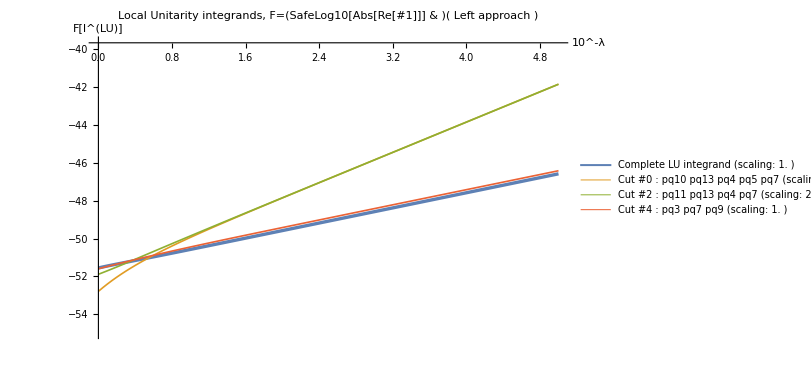
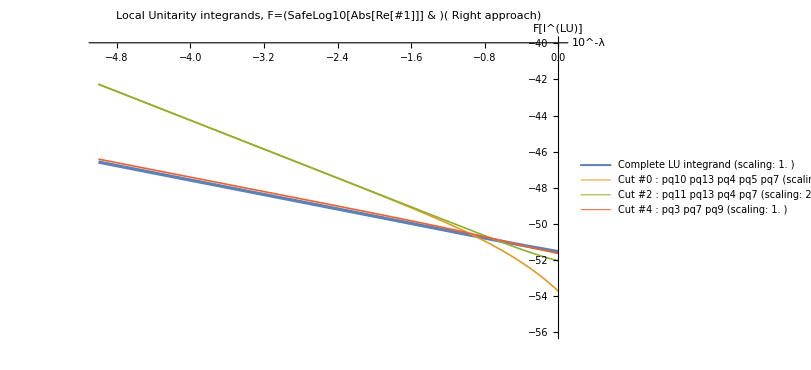
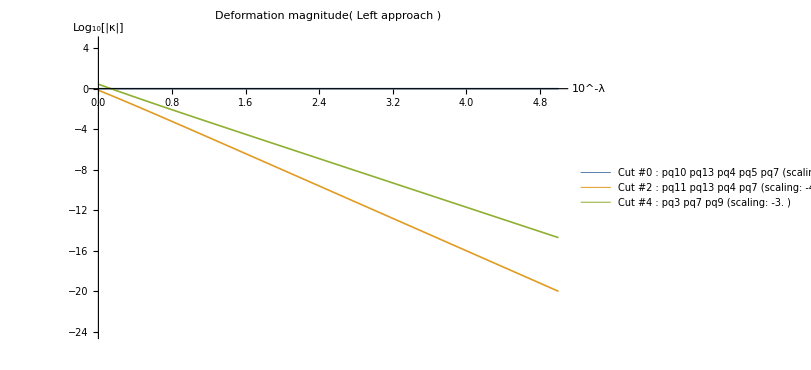
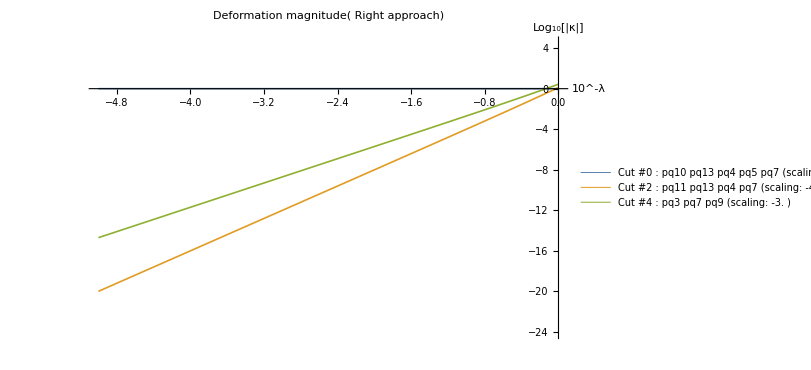
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

### Study of approach of (intersections of) thresholds

We can display the supergraph

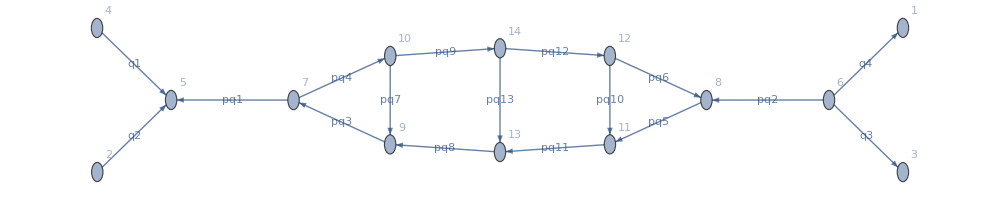

```mathematica
GetSuperGraph[SGYAMLinfo,ShowVertexLabels->Automatic,Size->1000]
```

And all of its LMBs, of which we show here the first twelve

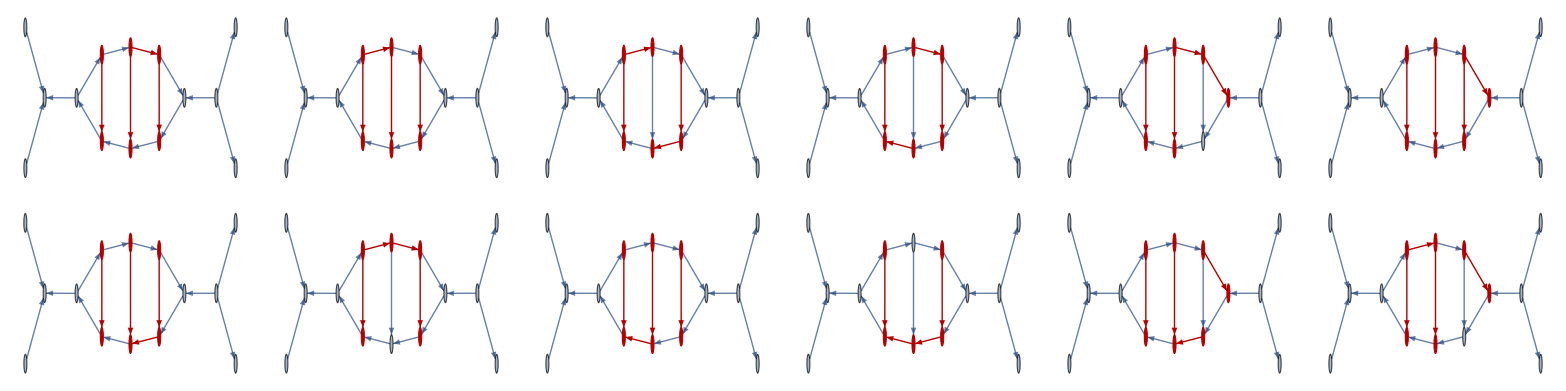

```mathematica
Table[HighlightGraph[GetSuperGraph[SGYAMLinfo],lmb],{lmb, GenerateAllLMBs[SGYAMLinfo]⟦;;12⟧}]//Multicolumn[#,6]&
```

We can automatically generate all E-surfaces (the only slow part is finding whether or not points exists on them)

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
```

And display them:

All 16 s-channel E-surfaces:

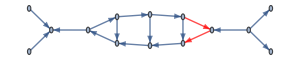
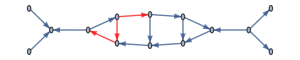
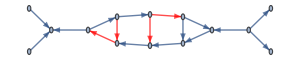
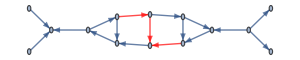
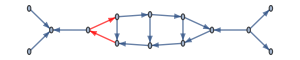
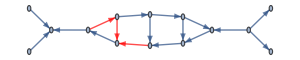
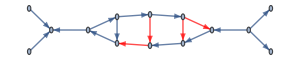
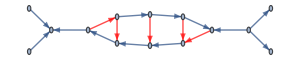
ID 1: | -Graphics- | ID 5: | -Graphics- | ID 9: | -Graphics- | ID 13: | -Graphics- | 
ID 2: | -Graphics- | ID 6: | -Graphics- | ID 10: | -Graphics- | ID 14: | -Graphics- | 
ID 3: | -Graphics- | ID 7: | -Graphics- | ID 11: | -Graphics- | ID 15: | -Graphics- | 
ID 4: | -Graphics- | ID 8: | -Graphics- | ID 12: | -Graphics- | ID 16: | -Graphics- |

All 12 soft E-surfaces:

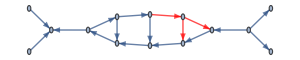
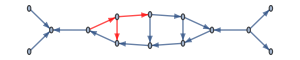
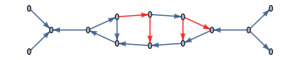
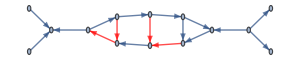
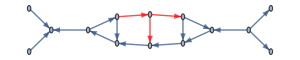
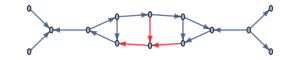
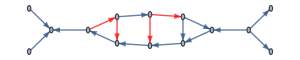
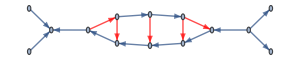
ID 1: | -Graphics- | ID 4: | -Graphics- | ID 7: | -Graphics- | ID 10: | -Graphics- | 
ID 2: | -Graphics- | ID 5: | -Graphics- | ID 8: | -Graphics- | ID 11: | -Graphics- | 
ID 3: | -Graphics- | ID 6: | -Graphics- | ID 9: | -Graphics- | ID 12: | -Graphics- |

All 26 internal E-surfaces:

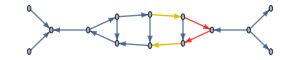
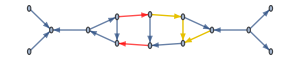
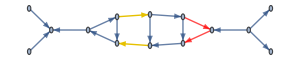
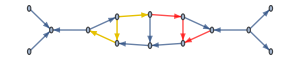
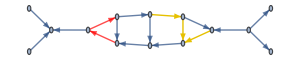
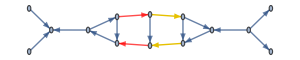
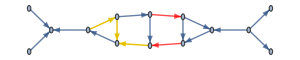
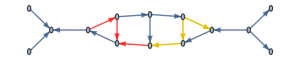
ID 1: | -Graphics- | ID 7: | -Graphics- | ID 13: | -Graphics- | ID 19: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 8: | -Graphics- | ID 14: | -Graphics- | ID 20: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 9: | -Graphics- | ID 15: | -Graphics- | ID 21: | -Graphics- | 
ID 4: | -Graphics- | ID 10: | -Graphics- | ID 16: | -Graphics- | ID 22: | -Graphics- | 
ID 5: | -Graphics- | ID 11: | -Graphics- | ID 17: | -Graphics- | ID 23: | -Graphics- | 
ID 6: | -Graphics- | ID 12: | -Graphics- | ID 18: | -Graphics- | ID 24: | -Graphics- |

All 30 composite E-surfaces:

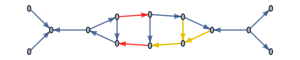
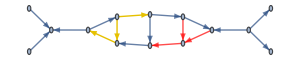
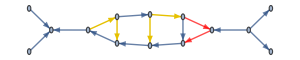
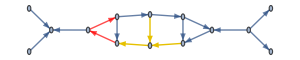
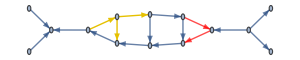
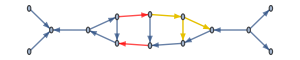
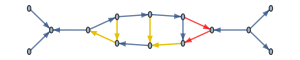
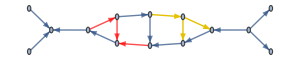
ID 1: | -Graphics- | ID 7: | -Graphics- | ID 13: | -Graphics- | ID 19: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 8: | -Graphics- | ID 14: | -Graphics- | ID 20: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 9: | -Graphics- | ID 15: | -Graphics- | ID 21: | -Graphics- | ID 27: | -Graphics-
ID 4: | -Graphics- | ID 10: | -Graphics- | ID 16: | -Graphics- | ID 22: | -Graphics- | ID 28: | -Graphics-
ID 5: | -Graphics- | ID 11: | -Graphics- | ID 17: | -Graphics- | ID 23: | -Graphics- | ID 29: | -Graphics-
ID 6: | -Graphics- | ID 12: | -Graphics- | ID 18: | -Graphics- | ID 24: | -Graphics- | ID 30: | -Graphics-

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Size->300,Colors->{Red}]
```

Or just one particular one

```mathematica
DisplayESurface[SGYAMLinfo,allESurfaces["internal"]⟦8⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

-Graphics-

And access a wealth of information about each, e.g.:

```mathematica
MyDataset[allESurfaces["internal"]⟦8⟧]
```

We can build a helper association to directly access Cutkosky cut E-surfaces.

```mathematica
CutkoskyEsurfaces=Association[Table[es["OutgoingEdges"]->es,{es,allESurfaces["s-channel"]}]];
```

And easily find a point on (multiple) E-surfaces as follows:

```mathematica
aPointToExplore=FindPointOnEsurfaces[{CutkoskyEsurfaces[{"pq3","pq7","pq9"}],CutkoskyEsurfaces[{"pq11","pq12"}],CutkoskyEsurfaces[{"pq5","pq6"}]},SGYAMLinfo,NoDeformationHyperparams,DEBUG->False,AcceptThreshold->10^-25]
```

<|pq4→{0.748698076509614778096305,188.5462339045764623364008,-96.31191404047328318224088},pq7→{-22.80762598441086201094969,-119.022908250074953658373,200.0212201705006127852929},pq10→{-60.88859303925227122362449,76.13077927795284010713445,96.52516039899613526165371},pq13→{104.2369245441488449475185,-76.79846975737861477410443,-39.77284964083868346565634}|>

And we can verify that it is indeed located on these three E-surfaces

```mathematica
MyDataset[Association[Table[e->CutkoskyEsurfaces[e]["Eq"]/.GenerateLoopMomenta[SGYAMLinfo,moms->aPointToExplore],{e,Keys[CutkoskyEsurfaces]}]]]
```

Look at all momenta for this configuration:

```mathematica
ComputeAllMomenta[aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

Evaluate the LU expression on it, first without E-surface analysis:

```mathematica
MyDataset[EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And then including the E-surface analysis

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
MyDataset[evaluationWithEsurfaceAnalysis]
```

And now with more detailed info about the E-surface analysis

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel","soft"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

--------------------------------------------------

Analysis of soft E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

We can now approach this point automatically in a double-sided fashion with:

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

But it sometimes better to not look in Log Log plot and study separately the real and imaginary part of the integrand

```mathematica
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Re[#]&)]⟦1⟧}]
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Im[#]&)]⟦1⟧}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

And one can bypass the double-sided study and just directly look at a single approach

```mathematica
RefreshHooks[];
ApproachRawData=AnalyzeApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->300,Seed->1, LambdaMax->5.,LambdaMin->0,ApproachSide->-1];
```

```mathematica
Grid[MonitorApproachResult[ApproachRawData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},ApproachSide->-1,IntegrandToPlot->(Re[#]&)]]
```

-Graphics-
-Graphics-

### Cross-checking YAML E-surfaces

```mathematica
allYAMLEsurfaces=ImportEsurfacesFromYaml[SGYAMLinfo,NoDeformationHyperparams,GenerateExamplePoints->False,EsurfID->None(*{5,1,2,11}*)];
```

```mathematica
YAMLEsurfacesMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,allYAMLEsurfaces["YAML"]}]];
```

One can look at all E-surfaces imported this way

```mathematica
SGYAMLinfo["cutkosky_cuts"]⟦3⟧["amplitudes"]⟦2⟧["thresholds"]⟦1⟧
```

<|foci→{2,0},id→0,mass_shift→0.,shift_in_lmb_sig→{{1,-1,0,-1},{-1,-1,0,0}}|>

```mathematica
SGYAMLinfo["cutkosky_cuts"]⟦3⟧["amplitudes"]⟦2⟧["thresholds"]⟦2⟧
```

<|foci→{2,0},id→1,mass_shift→0.,shift_in_lmb_sig→{{-1,1,0,1},{1,1,0,0}}|>

```mathematica
DisplayESurfaces[SGYAMLinfo,allYAMLEsurfaces,Colors->Automatic,nCols->4]
```

All 48 YAML E-surfaces:

ID #1 ({3, 1, 2, 1}): | -Graphics- | ID #13 ({5, 1, 2, 1}): | -Graphics- | ID #25 ({5, 1, 2, 13}): | -Graphics- | ID #37 ({6, 1, 2, 7}): | -Graphics-
ID #2 ({3, 1, 2, 2}): | -Graphics- | ID #14 ({5, 1, 2, 2}): | -Graphics- | ID #26 ({5, 1, 2, 14}): | -Graphics- | ID #38 ({6, 1, 2, 8}): | -Graphics-
ID #3 ({3, 1, 2, 3}): | -Graphics- | ID #15 ({5, 1, 2, 3}): | -Graphics- | ID #27 ({5, 1, 2, 15}): | -Graphics- | ID #39 ({6, 1, 2, 9}): | -Graphics-
ID #4 ({3, 1, 2, 4}): | -Graphics- | ID #16 ({5, 1, 2, 4}): | -Graphics- | ID #28 ({5, 1, 2, 16}): | -Graphics- | ID #40 ({6, 1, 2, 10}): | -Graphics-
ID #5 ({3, 1, 2, 5}): | -Graphics- | ID #17 ({5, 1, 2, 5}): | -Graphics- | ID #29 ({5, 1, 2, 17}): | -Graphics- | ID #41 ({6, 1, 2, 11}): | -Graphics-
ID #6 ({3, 1, 2, 6}): | -Graphics- | ID #18 ({5, 1, 2, 6}): | -Graphics- | ID #30 ({5, 1, 2, 18}): | -Graphics- | ID #42 ({6, 1, 2, 12}): | -Graphics-
ID #7 ({4, 1, 2, 1}): | -Graphics- | ID #19 ({5, 1, 2, 7}): | -Graphics- | ID #31 ({6, 1, 2, 1}): | -Graphics- | ID #43 ({6, 1, 2, 13}): | -Graphics-
ID #8 ({4, 1, 2, 2}): | -Graphics- | ID #20 ({5, 1, 2, 8}): | -Graphics- | ID #32 ({6, 1, 2, 2}): | -Graphics- | ID #44 ({6, 1, 2, 14}): | -Graphics-
ID #9 ({4, 1, 2, 3}): | -Graphics- | ID #21 ({5, 1, 2, 9}): | -Graphics- | ID #33 ({6, 1, 2, 3}): | -Graphics- | ID #45 ({6, 1, 2, 15}): | -Graphics-
ID #10 ({4, 1, 2, 4}): | -Graphics- | ID #22 ({5, 1, 2, 10}): | -Graphics- | ID #34 ({6, 1, 2, 4}): | -Graphics- | ID #46 ({6, 1, 2, 16}): | -Graphics-
ID #11 ({4, 1, 2, 5}): | -Graphics- | ID #23 ({5, 1, 2, 11}): | -Graphics- | ID #35 ({6, 1, 2, 5}): | -Graphics- | ID #47 ({6, 1, 2, 17}): | -Graphics-
ID #12 ({4, 1, 2, 6}): | -Graphics- | ID #24 ({5, 1, 2, 12}): | -Graphics- | ID #36 ({6, 1, 2, 6}): | -Graphics- | ID #48 ({6, 1, 2, 18}): | -Graphics-

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Colors->{Red},nCols->4]
```

All 16 s-channel E-surfaces:

ID 1: | -Graphics- | ID 5: | -Graphics- | ID 9: | -Graphics- | ID 13: | -Graphics-
ID 2: | -Graphics- | ID 6: | -Graphics- | ID 10: | -Graphics- | ID 14: | -Graphics-
ID 3: | -Graphics- | ID 7: | -Graphics- | ID 11: | -Graphics- | ID 15: | -Graphics-
ID 4: | -Graphics- | ID 8: | -Graphics- | ID 12: | -Graphics- | ID 16: | -Graphics-

All 12 soft E-surfaces:

ID 1: | -Graphics- | ID 4: | -Graphics- | ID 7: | -Graphics- | ID 10: | -Graphics-
ID 2: | -Graphics- | ID 5: | -Graphics- | ID 8: | -Graphics- | ID 11: | -Graphics-
ID 3: | -Graphics- | ID 6: | -Graphics- | ID 9: | -Graphics- | ID 12: | -Graphics-

All 26 internal E-surfaces:

ID 1: | -Graphics- | ID 8: | -Graphics- | ID 15: | -Graphics- | ID 22: | -Graphics-
ID 2: | -Graphics- | ID 9: | -Graphics- | ID 16: | -Graphics- | ID 23: | -Graphics-
ID 3: | -Graphics- | ID 10: | -Graphics- | ID 17: | -Graphics- | ID 24: | -Graphics-
ID 4: | -Graphics- | ID 11: | -Graphics- | ID 18: | -Graphics- | ID 25: | -Graphics-
ID 5: | -Graphics- | ID 12: | -Graphics- | ID 19: | -Graphics- | ID 26: | -Graphics-
ID 6: | -Graphics- | ID 13: | -Graphics- | ID 20: | -Graphics- | 
ID 7: | -Graphics- | ID 14: | -Graphics- | ID 21: | -Graphics- |

All 30 composite E-surfaces:

ID 1: | -Graphics- | ID 9: | -Graphics- | ID 17: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 10: | -Graphics- | ID 18: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 11: | -Graphics- | ID 19: | -Graphics- | ID 27: | -Graphics-
ID 4: | -Graphics- | ID 12: | -Graphics- | ID 20: | -Graphics- | ID 28: | -Graphics-
ID 5: | -Graphics- | ID 13: | -Graphics- | ID 21: | -Graphics- | ID 29: | -Graphics-
ID 6: | -Graphics- | ID 14: | -Graphics- | ID 22: | -Graphics- | ID 30: | -Graphics-
ID 7: | -Graphics- | ID 15: | -Graphics- | ID 23: | -Graphics- | 
ID 8: | -Graphics- | ID 16: | -Graphics- | ID 24: | -Graphics- |

Or one at a time:

```mathematica
DisplayESurface[SGYAMLinfo,allYAMLEsurfaces["YAML"]⟦1⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

-Graphics-

Or one can also look at the YAML raw data for this E-surface:

```mathematica
(SGYAMLinfo["cutkosky_cuts"]⟦ #⟦1⟧ ⟧["amplitudes"]⟦ #⟦3⟧ ⟧["thresholds"]⟦ #⟦4⟧ ⟧&)@allYAMLEsurfaces["YAML"]⟦2⟧["id"]
```

<|foci→{2,0},id→1,mass_shift→0.,shift_in_lmb_sig→{{-1,1,0,1},{1,1,0,0}}|>

And the data generated for it too

```mathematica
Dataset[allYAMLEsurfaces["YAML"]⟦1⟧]
```

```mathematica
DisplayESurface[SGYAMLinfo,allYAMLEsurfaces["YAML"]⟦1⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

-Graphics-

Find correspondences with independent generation of these E-surfaces

```mathematica
EsurfMappings=FindMappingOfYAMLEsurfaces[SGYAMLinfo,allYAMLEsurfaces,allESurfaces];
```

Let’s compare two different representations of the same E-surface thresholds:

```mathematica
EsurfMappings[3][{{"s-channel",12},{"s-channel",4,False}}]
```

{YAML,{3,1,2,3}}

First as a combination of two thresholds

```mathematica
{DisplayESurface[SGYAMLinfo,allESurfaces["s-channel"]⟦12⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic],
DisplayESurface[SGYAMLinfo,allESurfaces["s-channel"]⟦4⟧,Size->1000,Colors->{Green},ShowVertexLabels->Automatic],
}//Multicolumn[#,2]&
```

-Graphics- | 
-Graphics- |

And then as a YAML amplitude-Esurface

```mathematica
DisplayESurface[SGYAMLinfo,YAMLEsurfacesMap[EsurfMappings[3][{{"s-channel",12},{"s-channel",4,False}}]⟦2⟧],Size->1000,Colors->{Red,Green},ShowVertexLabels->Automatic]
```

-Graphics-

And finally compare their evaluation of the E-surface equation for particular momenta lying on the corresponding Cutkosky cuts:

```mathematica
failedEqComparisons=CompareEquations[SGYAMLinfo,NoDeformationHyperparams,EsurfMappings,allYAMLEsurfaces,allESurfaces,DEBUG->True,AcceptThreshold->10^-12];
```

SUCCESS: All 48 equation comparisons are successful.

Notice that this is a non-trivial check because the equations look very different, i.e.:

```mathematica
allESurfaces["s-channel"]⟦4⟧["Eq"]
```

-1000.+√(k3x^2+k3y^2+k3z^2)+√(29929.+(k1x-k2x-k4x)^2+(k1y-k2y-k4y)^2+(k1z-k2z-k4z)^2)+√(29929.+(k1x-k2x-k3x-k4x)^2+(k1y-k2y-k3y-k4y)^2+(k1z-k2z-k3z-k4z)^2)

vs

```mathematica
YAMLEsurfacesMap[{3,1,2,3}]["Eq"]
```

0.-√(29929.+k1x^2+k1y^2+k1z^2)-√(15625.+k2x^2+k2y^2+k2z^2)+√(0.+(0.+k3x)^2+(0.+k3y)^2+(0.+k3z)^2)+√(29929.+(0.+k1x-k2x-k3x-k4x)^2+(0.+k1y-k2y-k3y-k4y)^2+(0.+k1z-k2z-k3z-k4z)^2)-√(k4x^2+k4y^2+k4z^2)

And they match only when evaluated on the Cutkosky cut, i.e. the difference reads:

```mathematica
(allESurfaces["s-channel"]⟦4⟧["Eq"]-YAMLEsurfacesMap[{3,1,2,3}]["Eq"])//Simplify
```

-1000.+√(29929.+k1x^2+k1y^2+k1z^2)+√(15625.+k2x^2+k2y^2+k2z^2)+√(k4x^2+k4y^2+k4z^2)+√(29929.+(-k1x+k2x+k4x)^2+(-k1y+k2y+k4y)^2+(-k1z+k2z+k4z)^2)

Which is exactly the equation of the cutkosky cut, i.e.:

```mathematica
allESurfaces["s-channel"]⟦12⟧["Eq"]
```

-1000.+√(29929.+k1x^2+k1y^2+k1z^2)+√(15625.+k2x^2+k2y^2+k2z^2)+√(29929.+(k1x-k2x-k4x)^2+(k1y-k2y-k4y)^2+(k1z-k2z-k4z)^2)+√(k4x^2+k4y^2+k4z^2)

```mathematica
allESurfaces["s-channel"]⟦12⟧["Eq"]-(allESurfaces["s-channel"]⟦4⟧["Eq"]-YAMLEsurfacesMap[{3,1,2,3}]["Eq"])//Simplify
```

0

### Analysis of a max weight point

We can automatically map the xs variable to the point in the sampling basis active at run time (use all integration channels if multichanneling was enabled

```mathematica
maxWgtPoint=MapFromXs[HookWithDeformation,
{0.849593720848453,0.24429579449322847,0.6402108135745326,0.8560665730509239,0.7384368123709596,0.36724149939496614,0.14036138814108864,0.16762193841514772,0.6144196438490055,0.34658379011798746,0.16176951799648479,0.7382519129987205}, 
SGYAMLinfo,NoDeformationHyperparams,basis->{"pq10", "pq13", "pq7", "pq5"}]
```

<|pq4→{102.169,234.105,294.913},pq7→{78.6458,138.126,37.3648},pq10→{194.287,5418.53,1584.01},pq13→{-416.242,-5719.04,-1579.2}|>

And now run the standard set of analysis tools onto it

```mathematica
ComputeAllMomenta[maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
Dataset[evaluationWithEsurfaceAnalysis][All,"Rescaling"]
```

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,maxWgtPoint,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Multi-channeled evaluation dissection

Here is a multi-channeled max weight point:

```mathematica
xsPointForMultiChannelAnalysis={0.07209142507053912,0.7211560788564384,0.48690233076922596,
0.0042818577494472265,0.2789711025543511,0.8129998685326427,
0.05190556729212403,0.9428516994230449,0.7796795438043773,
0.15656883548945189,0.8171080858446658,0.2982940352521837};
```

We can evaluate it directly using the API

```mathematica
RefreshHooks[];
RFM$EvaluateIntegrand[HookRunConfig,xsPointForMultiChannelAnalysis]
```

8.7804×10^-6+0.00010524 ⅈ

Or dissect it with “MultiChannelPointAnalyzer”, beware however that one must supply a Hook here which has loaded a yaml that does *not* use multichanneling, since we will be using non-multichanneled evaluations to dissect the evaluation

```mathematica
RefreshHooks[];
multiChannelAnalysis=MultiChannelPointAnalyzer[HookWithDeformation,SGYAMLinfo,RunConfigHyperparams,xsPointForMultiChannelAnalysis,Esurfaces->allYAMLEsurfaces,DEBUG->False];
```

And we recover the multi-channeled evaluation above, and gather additional stats

```mathematica
MyDataset[multiChannelAnalysis["statistics"]]
```

One can then look at the result from each channel, sorted from most to least relevant

```mathematica
MyDataset[multiChannelAnalysis["summary"]]
```

One can then look at details of the evaluation for each channel and each Cutkosky cut:

```mathematica
MyDataset[multiChannelAnalysis["full"][{"optimised",0}][3]]
```

And conveniently display E-surface evaluations:

```mathematica
DisplayEvaluationEsurf[multiChannelAnalysis["full"][{"optimised",0}],SGYAMLinfo]
```

--------------------------------------------------

Analysis of YAML E-surfaces:

--------------------------------------------------

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #3 | {pq12,pq13,pq3,pq7}
 | Cut #5 | {pq4,pq7,pq8}

--------------------------------------------------

Analysis of UV E-surfaces:

--------------------------------------------------

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #3 | {pq12,pq13,pq3,pq7}
 | Cut #5 | {pq4,pq7,pq8}

### Testing deformation on (intersections of) E-surfaces

```mathematica
allIntersections=FindYAMLEsurfaceIntersections[allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,MaxNEsurfaces->2];
```

WARNING: Notice there are many UV E-surface copies

```mathematica
allYAMLEsurfacesMap[{"UV",{3, 1, 2, 7}}]["Eq"]
```

0.+√(36100.+(0.-k3x)^2+(0.-k3y)^2+(0.-k3z)^2)+√(36100.+(0.+k3x)^2+(0.+k3y)^2+(0.+k3z)^2)

```mathematica
allYAMLEsurfacesMap[{"UV",{3, 1, 2, 8}}]["Eq"]
```

0.+2 √(36100.+(0.-k3x)^2+(0.-k3y)^2+(0.-k3z)^2)

First test the non-existing UV E-surfaces

```mathematica
RefreshHooks[];
NonExistingEsurfAnalysisResults=AnalyzeEsurfaceIntersections[
HookWithoutDeformation,HookWithDeformation,allIntersections,allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,
Seed->Automatic,CheckNonExistingEsurfaces->True,CheckExistingEsurfaces->False,NonExistingEsurfCategories->{"UV"},
SelectedMethod->"DifferentialEvolution",MinimizeNiterations->500,
AcceptThreshold->10^-8,PrecisionIncrease->10,DEBUG->False
];
```

All 18 non-existing E-surface tests passed! (no complex solutions: 4)

And look at individual results

```mathematica
MyDataset[NonExistingEsurfAnalysisResults["details"][{"UV",{3, 1, 2, 7}}]["summary"]]
```

```mathematica
NonExistingEsurfAnalysisResults["details"][{"UV",{3, 1, 2, 7}}]["details"]["intersection_point"]//MyDataset
```

```mathematica
NonExistingEsurfAnalysisResults["details"][{"UV",{3, 1, 2, 7}}]["details"]["no_deformation_evaluations"]//MatrixForm
```

(0.00001 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→1.20733×10^-29+1.77985×10^-29 ⅈ,Rescaling→1.00001,MomentaInLMB→{{-26.6436,57.2107,-56.3547},{43.814,-15.0356,-38.0673},{-1.16865,-33.7798,8.66883},{-338.135,42.0423,40.9771}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386355,complex eval→0.00185107-0.00198614 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-0.000136352|>}|>,CutsSum→<|Res→1.20733×10^-29+1.77985×10^-29 ⅈ|>,FullIntegrand→<|Res→0.|>|>
1.×10^-6 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→3.81745×10^-27+5.62841×10^-27 ⅈ,Rescaling→1.,MomentaInLMB→{{-26.6482,57.2044,-56.3629},{43.806,-15.0413,-38.0731},{-1.17339,-33.7823,8.66609},{-338.136,42.0341,40.9755}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386356,complex eval→0.000585351-0.000628076 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-0.0000136344|>}|>,CutsSum→<|Res→3.81745×10^-27+5.62841×10^-27 ⅈ|>,FullIntegrand→<|Res→0.|>|>
1.×10^-7 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→1.20717×10^-24+1.77986×10^-24 ⅈ,Rescaling→1.,MomentaInLMB→{{-26.6487,57.2037,-56.3637},{43.8052,-15.0418,-38.0737},{-1.17386,-33.7825,8.66581},{-338.136,42.0333,40.9754}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386356,complex eval→0.000185104-0.000198615 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-1.36344×10^-6|>}|>,CutsSum→<|Res→1.20717×10^-24+1.77986×10^-24 ⅈ|>,FullIntegrand→<|Res→0.|>|>
1.×10^-8 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→3.81739×10^-22+5.62842×10^-22 ⅈ,Rescaling→1.,MomentaInLMB→{{-26.6487,57.2037,-56.3637},{43.8051,-15.0419,-38.0737},{-1.17391,-33.7825,8.66579},{-338.136,42.0332,40.9754}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386356,complex eval→0.000058535-0.0000628077 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-1.36344×10^-7|>}|>,CutsSum→<|Res→3.81739×10^-22+5.62842×10^-22 ⅈ|>,FullIntegrand→<|Res→0.|>|>
1.×10^-9 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→1.20715×10^-19+1.77987×10^-19 ⅈ,Rescaling→1.,MomentaInLMB→{{-26.6487,57.2037,-56.3638},{43.8051,-15.0419,-38.0737},{-1.17392,-33.7825,8.66578},{-338.136,42.0332,40.9754}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386356,complex eval→0.0000185104-0.0000198616 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-1.36344×10^-8|>}|>,CutsSum→<|Res→1.20715×10^-19+1.77987×10^-19 ⅈ|>,FullIntegrand→<|Res→0.|>|>
1.×10^-10 | <|2→<|cutID→2,edges→{pq11,pq13,pq4,pq7},Res→3.81677×10^-17+5.62878×10^-17 ⅈ,Rescaling→1.,MomentaInLMB→{{-26.6487,57.2037,-56.3638},{43.8051,-15.0419,-38.0737},{-1.17392,-33.7825,8.66578},{-338.136,42.0332,40.9754}},MomentaDeformationInLMB→{{0,0,0},{0,0,0},{-191.86038,11.61698,19.296946},{0,0,0}},DeformationJacobian→1.+0. ⅈ,{TestEsurfaces,Esurf analysis}→{<|id→{UV,{3,1,2,7}},edges→{{pq10,pq5}},eval→0.386356,complex eval→5.85338×10^-6-6.2809×10^-6 ⅈ,Normalised κ⃗.∇_(k⃗) η(k⃗)→-1.36344×10^-9|>}|>,CutsSum→<|Res→3.81677×10^-17+5.62878×10^-17 ⅈ|>,FullIntegrand→<|Res→0.|>|>)

And now the existing E-surface intersections

```mathematica
RefreshHooks[];
intersectionAnalysisResults=AnalyzeEsurfaceIntersections[
HookWithoutDeformation,HookWithDeformation,allIntersections,allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,
Seed->Automatic,CheckNonExistingEsurfaces->False,CheckExistingEsurfaces->True
];
```

All 56 intersections tests passed.

And one can look at individual results then:

```mathematica
MyDataset[intersectionAnalysisResults["details"][{4,1,{{"YAML",{5, 1, 2, 2}}}}]["summary"]]
```

And the particular intersection point considered

```mathematica
MyDataset[intersectionAnalysisResults["details"][{4,1,{{"YAML",{5, 1, 2, 2}}}}]["details"]["intersection_point"]]
```

And even the evolution of certain quantities during the approach

```mathematica
MyDataset[Table[{evals⟦1⟧,evals⟦2⟧[4]["Res"]},{evals,intersectionAnalysisResults["details"][{4,1,{{"YAML",{5, 1, 2, 2}}}}]["details"]["no_deformation_evaluations"]}]]
```

### Workspace

It cannot find points on the non-existing (soft) YAML E-surfaces...

```mathematica
RefreshHooks[];
NonExistingEsurfAnalysisResults=AnalyzeEsurfaceIntersections[
HookWithoutDeformation,HookWithDeformation,allIntersections,allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,
Seed->Automatic,CheckNonExistingEsurfaces->True,CheckExistingEsurfaces->False,NonExistingEsurfCategories->{"YAML"},
SelectedMethod->"DifferentialEvolution",MinimizeNiterations->500,
AcceptThreshold->10^-8,PrecisionIncrease->10,DEBUG->True
];
```

Main issue is that NMinimize fail at solving the following:

```mathematica
NMinimize[0.001000000000000000020816681711721685132943093776702880859375`60. Norm[(
√(36100.`60.+(k3x+1.`60. ⅈ kappa3x)^2+(k3y+1.`60. ⅈ kappa3y)^2+(k3z+1.`60. ⅈ kappa3z)^2)+√(36100.`60.+(-1.`60. k4x-1.`60. ⅈ kappa4x)^2+(-1.`60. k4y-1.`60. ⅈ kappa4y)^2+(-1.`60. k4z-1.`60. ⅈ kappa4z)^2)+√(36100.`60.+(-1.`60. k3x-1.`60. k4x-1.`60. ⅈ kappa3x-1.`60. ⅈ kappa4x)^2+(-1.`60. k3y-1.`60. k4y-1.`60. ⅈ kappa3y-1.`60. ⅈ kappa4y)^2+(-1.`60. k3z-1.`60. k4z-1.`60. ⅈ kappa3z-1.`60. ⅈ kappa4z)^2))],
{k1x,k1y,k1z,k2x,k2y,k2z,k3x,k3y,k3z,k4x,k4y,k4z,kappa3x,kappa3y,kappa3z,kappa4x,kappa4y,kappa4z},MaxIterations->20000,Method->"DifferentialEvolution",AccuracyGoal->20,PrecisionGoal->20
]
```

$Aborted

```mathematica
<|"k"->{lx,ly,lz},"pA"->p⟦i⟧,"pB"->p⟦j⟧,"mA"->m⟦i⟧,"mB"->m⟦j⟧,"K"->(E[[j]]-E[[i]])|>
```

```mathematica
BilinearForm[E_,kin_]:=Module[
{
parametricBilinear={{{4 (Const+pAx-pBx) (Const-pAx+pBx),-4 (pAx-pBx) (pAy-pBy),-4 (pAx-pBx) (pAz-pBz)},{-4 (pAx-pBx) (pAy-pBy),4 (Const+pAy-pBy) (Const-pAy+pBy),-4 (pAy-pBy) (pAz-pBz)},{-4 (pAx-pBx) (pAz-pBz),-4 (pAy-pBy) (pAz-pBz),4 (Const+pAz-pBz) (Const-pAz+pBz)}},{-2 Const^2 (pAx+pBx)+2 (pAx-pBx) (MA^2-MB^2+pAx^2+pAy^2+pAz^2-pBx^2-pBy^2-pBz^2),-2 Const^2 (pAy+pBy)+2 (pAy-pBy) (MA^2-MB^2+pAx^2+pAy^2+pAz^2-pBx^2-pBy^2-pBz^2),-2 Const^2 (pAz+pBz)+2 (pAz-pBz) (MA^2-MB^2+pAx^2+pAy^2+pAz^2-pBx^2-pBy^2-pBz^2)},-Const^4-(MA^2-MB^2+pAx^2+pAy^2+pAz^2-pBx^2-pBy^2-pBz^2)^2+2 Const^2 (MA^2+MB^2+pAx^2+pAy^2+pAz^2+pBx^2+pBy^2+pBz^2)
},
matrices
},
matrices=parametricBilinear/.{
(* Adjust sign conventions w.r.t when I derived the form of the matrices of the Chebyshev system *)
Const->-(E["K"]/.kin),
pAx->If[(E["pA"]/.kin)===0,0,-(E["pA"]/.kin)⟦1⟧],
pAy->If[(E["pA"]/.kin)===0,0,-(E["pA"]/.kin)⟦2⟧],
pAz->If[(E["pA"]/.kin)===0,0,-(E["pA"]/.kin)⟦3⟧],
pBx->If[(E["pB"]/.kin)===0,0,-(E["pB"]/.kin)⟦1⟧],
pBy->If[(E["pB"]/.kin)===0,0,-(E["pB"]/.kin)⟦2⟧],
pBz->If[(E["pB"]/.kin)===0,0,-(E["pB"]/.kin)⟦3⟧],
MA->(E["mA"]/.kin),
MB->(E["mB"]/.kin)
};
<|"A"->matrices⟦1⟧,"b"->matrices⟦2⟧,"c"->matrices⟦3⟧|>
]
```

```mathematica
kvec=(Es⟦1⟧["k"]/.kin);
EvaluatedEtas=Simplify[Table[Simplify[BuildEllipsoidEq[Esurf]/.kin],{Esurf,Es}],Assumptions->{kx∈Reals,ky∈Reals,kz∈Reals}];
BilinearForms = Table[BilinearForm[E,kin],{E,Es}];
BilinearSystems=Table[kvec.bf["A"].kvec+2bf["b"].kvec+bf["c"],{bf,BilinearForms}];
constraints=Table[-r+bs<=0,{bs,BilinearSystems}];
res=FindMinimum[{r,constraints},Join[{r},kvec],Method->"InteriorPoint"];
```

```mathematica
Solve[((
√(36100.`60.+(k3x+1.`60. ⅈ kappa3x)^2+(k3y+1.`60. ⅈ kappa3y)^2+(k3z+1.`60. ⅈ kappa3z)^2)+√(36100.`60.+(-1.`60. k4x-1.`60. ⅈ kappa4x)^2+(-1.`60. k4y-1.`60. ⅈ kappa4y)^2+(-1.`60. k4z-1.`60. ⅈ kappa4z)^2)+√(36100.`60.+(-1.`60. k3x-1.`60. k4x-1.`60. ⅈ kappa3x-1.`60. ⅈ kappa4x)^2+(-1.`60. k3y-1.`60. k4y-1.`60. ⅈ kappa3y-1.`60. ⅈ kappa4y)^2+(-1.`60. k3z-1.`60. k4z-1.`60. ⅈ kappa3z-1.`60. ⅈ kappa4z)^2))/.{
k3y->1,k3z->1,k4x->1,k4y->1,k4z->1,kappa3y->1,kappa3z->1,kappa4x->1,kappa4y->1,kappa4z->1
})==0,
{k3x,kappa3x}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{kappa3x→2.5167229468015789049624474905717339986007878389323841375×10^-368 ((-6.5579195286064520687642686018929944642920972741697224204×10^369+1.86059410760274004177078641120772734099867688737124746×10^367 ⅈ)+3.973421076288382791545481697277742331591115982103220964×10^367 ⅈ k3x)},{kappa3x→2.5167229468015789049624474905717339986007878389323841375×10^-368 ((6.5181985273548006943390091173113270720650637890566247318×10^369+2.11414762710976927642573317103984570792051505932759857×10^367 ⅈ)+3.973421076288382791545481697277742331591115982103220964×10^367 ⅈ k3x)}}

```mathematica
NMinimize[0.001000000000000000020816681711721685132943093776702880859375`60. Norm[(
√(36100.`60.+(k3x+1.`60. ⅈ kappa3x)^2+(k3y+1.`60. ⅈ kappa3y)^2+(k3z+1.`60. ⅈ kappa3z)^2)+√(36100.`60.+(-1.`60. k4x-1.`60. ⅈ kappa4x)^2+(-1.`60. k4y-1.`60. ⅈ kappa4y)^2+(-1.`60. k4z-1.`60. ⅈ kappa4z)^2)+√(36100.`60.+(-1.`60. k3x-1.`60. k4x-1.`60. ⅈ kappa3x-1.`60. ⅈ kappa4x)^2+(-1.`60. k3y-1.`60. k4y-1.`60. ⅈ kappa3y-1.`60. ⅈ kappa4y)^2+(-1.`60. k3z-1.`60. k4z-1.`60. ⅈ kappa3z-1.`60. ⅈ kappa4z)^2))],
{k1x,k1y,k1z,k2x,k2y,k2z,k3x,k3y,k3z,k4x,k4y,k4z,kappa3x,kappa3y,kappa3z,kappa4x,kappa4y,kappa4z},MaxIterations->20000,Method->"DifferentialEvolution",AccuracyGoal->20,PrecisionGoal->20
]
```

```mathematica
<|"k"->{lx,ly,lz},"pA"->{3,3,3},"pB"->{0,0,0},"mA"->Sqrt[10],"mB"->Sqrt[10],"K"->(Sqrt[(kx+2)^2+(ky+2)^2+(kz+2)^2+10]/.{kx->1,ky->2,kz->3})|>
```

<|k→{lx,ly,lz},pA→{3,3,3},pB→{0,0,0},mA→√10,mB→√10,K→2 √15|>

```mathematica
NMinimize[ Norm[
Evaluate[Sqrt[(kx+2)^2+(ky+2)^2+(kz+2)^2+10]+Sqrt[(lx+3)^2+(ly+3)^2+(lz+3)^2+10]+Sqrt[(kx+lx)^2+(ky+ly)^2+(kz+lz)^2+10]/.{
kx->{rkx+ⅈ ikx},ky->{rky+ⅈ iky},kz->{rkz+ⅈ ikz},
lx->{rlx+ⅈ ilx},ly->{rly+ⅈ ily},lz->{rlz+ⅈ ilz}
}]
],
{
rkx,rky,rkz,rlx,rly,rlz,
ikx,iky,ikz,ilx,ily,ilz
},MaxIterations->1000,Method->"DifferentialEvolution",AccuracyGoal->20,PrecisionGoal->20
]
```

{0.138266,{rkx→-0.639327,rky→-0.452817,rkz→-0.70159,rlx→-2.70478,rly→-2.63096,rlz→-2.64928,ikx→-23.5494,iky→-1.29201,ikz→28.1083,ilx→-17.548,ily→-0.520576,ilz→15.3319}}

```mathematica
FindInstance[Sqrt[(x)^2+1]+Sqrt[(y)^2+1]+Sqrt[(x+y)^2+1]==0,{x,y}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[√(1+x^2)+√(1+y^2)+√(1+(x+y)^2)==0,{x,y}]

```mathematica
Sqrt[(x+ⅈ ix)^2+1]+Sqrt[(y+ⅈ iy)^2+1]+Sqrt[(x+y+ⅈ ix+ⅈ iy)^2+1]]
```

Re[√(1+(ⅈ ix+x)^2)+√(1+(ⅈ iy+y)^2)+√(1+(ⅈ ix+ⅈ iy+x+y)^2)]

```mathematica
FindInstance[ Norm[Sqrt[(x+ⅈ ix)^2-1]+Sqrt[(y+ⅈ iy)^2-1]+Sqrt[(x+y+ⅈ ix+ⅈ iy)^2-1]]==0,{x,y,ix,iy}]
```

{}

```mathematica
Solve[ Sqrt[(x+ⅈ ix)^2-1]+Sqrt[(y+ⅈ iy)^2-1]+Sqrt[(x+y+ⅈ ix+ⅈ iy)^2-1]==0,{x,y,ix,iy}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{iy→1/2 (-ix+ⅈ x-√3 √(-1-ix^2+2 ⅈ ix x+x^2)+2 ⅈ y)},{iy→1/2 (-ix+ⅈ x+√3 √(-1-ix^2+2 ⅈ ix x+x^2)+2 ⅈ y)}}

```mathematica
Solve[Sqrt[(x)^2+m^2]+Sqrt[(y)^2+m^2]+Sqrt[(x+y)^2+m^2]==0,{x,y}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→1/2 (-x-√3 √(-m^2-x^2))},{y→1/2 (-x+√3 √(-m^2-x^2))}}

## e^+ e^- → ϕ d d̄ | Triangle Box Box Triangle (NNLO)

-Graphics-

### Preamble (general information needed for all sections)

```mathematica
SGYAMLinfo=<|"FORM_integrand"-><|"call_signature"-><|"id"->0|>|>,"cutkosky_cuts"->{<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq3","parametric_shift"->{{0,0,1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{0,0,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq11","parametric_shift"->{{0,-1,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq4pq7pq5_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{-1,-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{0,0,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","parametric_shift"->{{0,-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->8|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq4pq7pq5_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq4","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq5","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,-1,-1,-1},{-1,-1,0,0}}|>},"id"->0,"lmb_to_cb"->{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","parametric_shift"->{{0,0,0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{0,0,-1,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","parametric_shift"->{{0,-1,-1,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->12|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq7pq3pq6_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{-1,-1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{0,0,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq11","parametric_shift"->{{0,-1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->9|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq10pq13pq7pq3pq6_1"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>},"cb_to_lmb"->{0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq10","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,1,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq3","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>,<|"m_squared"->0.,"name"->"pq6","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,-1,-1,-1},{0,0,0,0}}|>},"id"->1,"lmb_to_cb"->{0,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq3","parametric_shift"->{{0,1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{0,1,-1,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq13pq4pq7pq11_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{0,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","parametric_shift"->{{-1,1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->11|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{1,-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{1,-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->11|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG182_pq13pq4pq7pq11_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{-1,1,-1,0},{-1,-1,0,0}},"amp_sig"->{-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,-1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->3,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->5,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{5,4},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{4,4},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->-1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq4","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq11","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,-1,0,-1},{-1,-1,0,0}}|>},"id"->2,"lmb_to_cb"->{0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","parametric_shift"->{{1,1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{1,0,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->14|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq13pq7pq12pq3_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{1,0,1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq11","parametric_shift"->{{0,0,1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0},"start_node"->9|>,<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{0,0,-1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{0,0,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1},"start_node"->9|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}}},"ltd_cut_structure"->{{0,1}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->1,"name"->"SG_QG182_pq13pq7pq12pq3_1"|>,"n_loops"->1,"propagators"->{<|"amp_shift_in_cmb_sig"->{{0,0,1,0},{-1,-1,0,0}},"amp_sig"->{-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,1,0},{0,0,0,0}},"amp_sig"->{-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->3,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1},"id"->4,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1},"id"->5,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,0},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{1.},"foci"->{2,1},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{0,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{5,4},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-1.},"foci"->{4,4},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>}|>},"cb_to_lmb"->{1,1,1,0,0,1,0,0,0,0,0,1,1,0,0,0},"cuts"->{<|"m_squared"->0.,"name"->"pq13","particle_id"->21,"power"->1,"sign"->1,"signature"->{{0,0,0,1},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq12","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,-1,0,-1},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq3","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>},"id"->3,"lmb_to_cb"->{0,0,0,1,0,1,0,0,1,-1,0,-1,0,0,1,0}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","parametric_shift"->{{0,1,0},{1,1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->10|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq7pq3pq9_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq8","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{-1,-1},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq11","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","parametric_shift"->{{1,-1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq13","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1},"start_node"->9|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}},"ltd_cut_structure"->{{0,0,1,1},{0,-1,0,1},{0,-1,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->2,"name"->"SG_QG182_pq7pq3pq9_1"|>,"n_loops"->2,"propagators"->{<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{1,1,0,0}},"amp_sig"->{-1,-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->3,"lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{-1,1,0,0},{1,1,0,0}},"amp_sig"->{0,-1},"id"->4,"lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq12","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->5,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->6,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->7,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->8,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->9,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->10,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->11,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->12,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->13,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->8,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->9,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->10,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->11,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->12,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->13,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->14,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->15,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->16,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->17,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{8,7},"id"->18,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{7,7},"id"->19,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,12,10},"id"->20,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,13,10},"id"->21,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,12},"id"->22,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,13},"id"->23,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{10,10},"id"->24,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,7},"id"->25,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{7,7},"id"->26,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>}|>},"cb_to_lmb"->{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1},"cuts"->{<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq3","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,0,0,0},{-1,-1,0,0}}|>,<|"m_squared"->0.,"name"->"pq9","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,-1,0,0},{0,0,0,0}}|>},"id"->4,"lmb_to_cb"->{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1}|>,<|"amplitudes"->{<|"conjugate_deformation"->False,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{},"beta"->{}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->5,"propagators"->{<|"m_squared"->0.,"name"->"pq1","parametric_shift"->{{0,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq3","parametric_shift"->{{1,0,0},{-1,-1,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{},"start_node"->5|>},"loop_momentum_map"->{},"ltd_cut_structure"->{{0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->0,"name"->"SG_QG182_pq4pq7pq8_0"|>,"n_loops"->0,"propagators"->{},"thresholds"->{}|>,<|"conjugate_deformation"->True,"graph"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{},"loop_lines"->{<|"end_node"->13,"propagators"->{<|"m_squared"->0.,"name"->"pq2","parametric_shift"->{{0,0,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq5","parametric_shift"->{{1,-1,0},{0,0,-1,-1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","parametric_shift"->{{1,-1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{-1,-1},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq11","parametric_shift"->{{-1,1,0},{0,0,1,1}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","parametric_shift"->{{-1,1,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq13","parametric_shift"->{{0,0,0},{0,0,0,0}},"power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1},"start_node"->13|>},"loop_momentum_map"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}},"ltd_cut_structure"->{{0,0,1,1},{0,-1,0,1},{0,-1,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->2,"name"->"SG_QG182_pq4pq7pq8_1"|>,"n_loops"->2,"propagators"->{<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"amp_sig"->{-1,-1},"id"->0,"lmb_sig"->{{1,-1,-1,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->1,"lmb_sig"->{{1,-1,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq6","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->2,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"amp_sig"->{0,-1},"id"->3,"lmb_sig"->{{1,-1,0,-1},{-1,-1,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{1,-1,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->4,"lmb_sig"->{{1,-1,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq12","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->5,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->False,"uv_only"->False|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->6,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,0},"id"->7,"lmb_sig"->{{0,0,-1,0},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{1,0},"id"->8,"lmb_sig"->{{0,0,1,0},{0,0,0,0}},"mass"->0.,"name"->"pq10","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->9,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{-1,-1},"id"->10,"lmb_sig"->{{0,0,-1,-1},{0,0,0,0}},"mass"->0.,"name"->"pq5","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->11,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->False,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,-1},"id"->12,"lmb_sig"->{{0,0,0,-1},{0,0,0,0}},"mass"->0.,"name"->"pq11","uv_mass"->True,"uv_only"->True|>,<|"amp_shift_in_cmb_sig"->{{0,0,0,0},{0,0,0,0}},"amp_sig"->{0,1},"id"->13,"lmb_sig"->{{0,0,0,1},{0,0,0,0}},"mass"->0.,"name"->"pq13","uv_mass"->True,"uv_only"->True|>},"thresholds"->{<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,0},"id"->0,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->1,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,3,1},"id"->2,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->3,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,0},"id"->4,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,-1.},"foci"->{2,4,1},"id"->5,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1,1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->6,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,0},"id"->7,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->8,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{1.,0.,0.,1.},"foci"->{2,5,1},"id"->9,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1,-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->10,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,4},"id"->11,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->12,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{-1,-1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{3,5},"id"->13,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{1,1,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->14,"mass_shift"->0.,"shift_in_lmb_sig"->{{-1,1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{4,5},"id"->15,"mass_shift"->0.,"shift_in_lmb_sig"->{{1,-1,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->16,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{-1,-1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{0,1},"id"->17,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{1,1,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{8,7},"id"->18,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{-0.5,-0.5},"foci"->{7,7},"id"->19,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,12,10},"id"->20,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,13,10},"id"->21,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,12},"id"->22,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{12,13},"id"->23,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{10,10},"id"->24,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{8,7},"id"->25,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>,<|"fb_to_cmb"->{0.,-1.},"foci"->{7,7},"id"->26,"mass_shift"->0.,"shift_in_lmb_sig"->{{0,0,0,0},{0,0,0,0}},"sig_in_fb"->{-1}|>}|>},"cb_to_lmb"->{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},"cuts"->{<|"m_squared"->0.,"name"->"pq4","particle_id"->2,"power"->1,"sign"->1,"signature"->{{1,0,0,0},{0,0,0,0}}|>,<|"m_squared"->15625.,"name"->"pq7","particle_id"->1337,"power"->1,"sign"->-1,"signature"->{{0,1,0,0},{0,0,0,0}}|>,<|"m_squared"->0.,"name"->"pq8","particle_id"->2,"power"->1,"sign"->-1,"signature"->{{1,-1,0,0},{-1,-1,0,0}}|>},"id"->5,"lmb_to_cb"->{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1}|>},"default_fixed_cut_momenta"->{{},{}},"e_cm_squared"->1.*10^6,"edge_PDGs"->{{"q1",-11},{"q2",11},{"q3",-11},{"q4",11},{"pq1",22},{"pq2",22},{"pq3",2},{"pq4",2},{"pq5",2},{"pq6",2},{"pq7",1337},{"pq8",2},{"pq9",2},{"pq10",21},{"pq11",2},{"pq12",2},{"pq13",21}},"edge_signatures"-><|"pq1"->{{0,0,0,0},{-1,-1,0,0}},"pq10"->{{0,0,1,0},{0,0,0,0}},"pq11"->{{1,-1,0,-1},{-1,-1,0,0}},"pq12"->{{1,-1,0,-1},{0,0,0,0}},"pq13"->{{0,0,0,1},{0,0,0,0}},"pq2"->{{0,0,0,0},{-1,-1,0,0}},"pq3"->{{1,0,0,0},{-1,-1,0,0}},"pq4"->{{1,0,0,0},{0,0,0,0}},"pq5"->{{1,-1,-1,-1},{-1,-1,0,0}},"pq6"->{{1,-1,-1,-1},{0,0,0,0}},"pq7"->{{0,1,0,0},{0,0,0,0}},"pq8"->{{1,-1,0,0},{-1,-1,0,0}},"pq9"->{{1,-1,0,0},{0,0,0,0}},"q1"->{{0,0,0,0},{1,0,0,0}},"q2"->{{0,0,0,0},{0,1,0,0}},"q3"->{{0,0,0,0},{0,0,1,0}},"q4"->{{0,0,0,0},{0,0,0,1}}|>,"external_momenta"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_momentum_basis"->{"pq4","pq7","pq10","pq13"},"multi_channeling_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->0,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq10","pq13","pq7","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq10","pq13","pq3","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq7","pq11","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq7","pq11","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->2,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq7","pq11","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq12","pq3","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq12","pq3","pq6"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->3,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq13","pq12","pq3","pq5"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,0,0,1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq6","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->4,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq5","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq6","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq13"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq12"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq11"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->5,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq5","pq10"},"defining_propagators_powers"->{1,1,1,1},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>},"multi_channeling_lmb_bases"->{<|"channel_id"->0,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq10","pq12","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->1,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq12","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->2,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq10","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->3,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq12","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->4,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq10","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->5,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq10","pq11","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->6,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq11","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->7,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq11","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->8,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq9","pq10","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->9,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq9","pq10","pq12"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->10,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->11,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq12"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->12,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq10"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->13,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->14,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq12"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->15,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq10"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->16,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq9","pq10","pq11"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->17,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq9","pq11"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->18,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq9","pq11"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->19,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq13"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->20,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq11"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->21,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq13"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->22,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq11"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->23,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq10"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->24,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq13"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->25,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq11"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->26,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq10"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->27,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq7","pq8","pq10","pq12"},"signatures"->{{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->28,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq6","pq7","pq8","pq12"},"signatures"->{{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->29,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq5","pq7","pq8","pq12"},"signatures"->{{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->30,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq10","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->31,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->32,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->33,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq12","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->34,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->35,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq10","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->36,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->37,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq11","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->38,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq9","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->39,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq9","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->40,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->41,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->42,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->43,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->44,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->45,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->46,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq9","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->47,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq9","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->48,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq9","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->49,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq8","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->50,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq8","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->51,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->52,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->53,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->54,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->55,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->56,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->57,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq8","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->58,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq8","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->59,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq8","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->60,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq7","pq10","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->61,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq7","pq10","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->62,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->63,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->64,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->65,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq13"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->66,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq12"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->67,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq10"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->68,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq7","pq10","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->69,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq5","pq7","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->70,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq4","pq6","pq7","pq11"},"signatures"->{{{1,0,0,0},{0,0,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->71,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq10","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->72,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->73,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->74,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq12","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->75,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->76,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq10","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->77,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->78,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq11","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->79,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->80,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->81,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->82,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->83,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->84,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->85,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->86,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->87,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq9","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->88,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq9","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->89,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq9","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->90,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq8","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->91,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq8","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->92,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->93,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->94,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->95,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->96,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->97,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->98,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq8","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->99,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq8","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->100,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq8","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{1,-1,0,0},{-1,-1,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->101,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq7","pq10","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->102,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq7","pq10","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->103,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->104,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->105,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->106,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq13"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0}}}|>,<|"channel_id"->107,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq11"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{-1,-1,0,0}}}|>,<|"channel_id"->108,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq10"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}}}|>,<|"channel_id"->109,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq7","pq10","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->110,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq6","pq7","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{0,0,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>,<|"channel_id"->111,"cutkosky_cut_id"->-1,"defining_propagator_masses"->{0.,0.,0.,0.},"defining_propagators"->{"pq3","pq5","pq7","pq12"},"signatures"->{{{1,0,0,0},{-1,-1,0,0}},{{1,-1,-1,-1},{-1,-1,0,0}},{{0,1,0,0},{0,0,0,0}},{{1,-1,0,-1},{0,0,0,0}}}|>},"n_incoming_momenta"->2,"n_loops"->4,"name"->"SG_QG182","optimal_channel_ids"->{0},"overall_numerator"->1.,"propagators"->{<|"PDG"->22,"m_squared"->0.,"name"->"pq1","power"->1,"signature"->{{0,0,0,0},{-1,-1,0,0}},"vertices"->{7,5}|>,<|"PDG"->22,"m_squared"->0.,"name"->"pq2","power"->1,"signature"->{{0,0,0,0},{-1,-1,0,0}},"vertices"->{6,8}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq3","power"->1,"signature"->{{1,0,0,0},{-1,-1,0,0}},"vertices"->{9,7}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq4","power"->1,"signature"->{{1,0,0,0},{0,0,0,0}},"vertices"->{7,10}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq5","power"->1,"signature"->{{1,-1,-1,-1},{-1,-1,0,0}},"vertices"->{8,11}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq6","power"->1,"signature"->{{1,-1,-1,-1},{0,0,0,0}},"vertices"->{12,8}|>,<|"PDG"->1337,"m_squared"->15625.,"name"->"pq7","power"->1,"signature"->{{0,1,0,0},{0,0,0,0}},"vertices"->{10,9}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq8","power"->1,"signature"->{{1,-1,0,0},{-1,-1,0,0}},"vertices"->{13,9}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq9","power"->1,"signature"->{{1,-1,0,0},{0,0,0,0}},"vertices"->{10,14}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq10","power"->1,"signature"->{{0,0,1,0},{0,0,0,0}},"vertices"->{12,11}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq11","power"->1,"signature"->{{1,-1,0,-1},{-1,-1,0,0}},"vertices"->{11,13}|>,<|"PDG"->2,"m_squared"->0.,"name"->"pq12","power"->1,"signature"->{{1,-1,0,-1},{0,0,0,0}},"vertices"->{14,12}|>,<|"PDG"->21,"m_squared"->0.,"name"->"pq13","power"->1,"signature"->{{0,0,0,1},{0,0,0,0}},"vertices"->{14,13}|>},"topo"-><|"analytical_result_imag"->0.,"analytical_result_real"->0.,"constant_deformation"-><|"alpha"->{{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.}},"beta"->{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}|>,"external_kinematics"->{{500.,0.,0.,500.},{500.,0.,0.,-500.},{500.,0.,0.,500.},{500.,0.,0.,-500.}},"loop_lines"->{<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq1","power"->2,"q"->{-1000.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0,0},"start_node"->8|>,<|"end_node"->8,"propagators"->{<|"m_squared"->0.,"name"->"pq3","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq4","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,0,0,0},"start_node"->9|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq5","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq6","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,-1,-1},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->15625.,"name"->"pq7","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,1,0,0},"start_node"->8|>,<|"end_node"->9,"propagators"->{<|"m_squared"->0.,"name"->"pq8","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq9","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,0,0},"start_node"->13|>,<|"end_node"->11,"propagators"->{<|"m_squared"->0.,"name"->"pq10","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,1,0},"start_node"->8|>,<|"end_node"->13,"propagators"->{<|"m_squared"->0.,"name"->"pq11","power"->1,"q"->{-1000.,0.,0.,0.},"uv"->False|>,<|"m_squared"->0.,"name"->"pq12","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{1,-1,0,-1},"start_node"->11|>,<|"end_node"->13,"propagators"->{<|"m_squared"->0.,"name"->"pq13","power"->1,"q"->{0.,0.,0.,0.},"uv"->False|>},"signature"->{0,0,0,1},"start_node"->8|>},"ltd_cut_structure"->{{0,0,0,1,0,1,1,1},{0,0,0,1,1,1,0,1},{0,0,0,1,1,1,-1,0},{0,0,-1,1,0,0,1,1},{0,0,1,1,0,1,0,1},{0,0,-1,1,1,0,0,1},{0,0,-1,1,1,0,-1,0},{0,0,-1,1,1,-1,0,0},{0,1,0,0,0,1,-1,1},{0,1,0,0,-1,1,0,1},{0,1,0,0,1,1,-1,0},{0,1,-1,0,0,0,1,1},{0,1,-1,0,0,1,0,1},{0,1,-1,0,1,0,0,1},{0,1,-1,0,1,0,-1,0},{0,1,-1,0,1,-1,0,0},{0,1,0,1,0,1,0,1},{0,1,-1,-1,0,0,0,1},{0,1,-1,-1,0,-1,0,0},{0,1,0,-1,0,1,-1,0},{0,1,-1,-1,0,0,-1,0}},"maximum_ratio_expansion_threshold"->-1.,"n_loops"->4,"name"->"SG_QG182"|>,"topo_edges"->{{"q1",4,5,0},{"q2",2,5,0},{"q3",6,3,0},{"q4",6,1,0},{"pq1",7,5,1},{"pq2",6,8,1},{"pq3",9,7,1},{"pq4",7,10,1},{"pq5",8,11,1},{"pq6",12,8,1},{"pq7",10,9,1},{"pq8",13,9,1},{"pq9",10,14,1},{"pq10",12,11,1},{"pq11",11,13,1},{"pq12",14,12,1},{"pq13",14,13,1}}|>;
```

Some general information is loaded here

```mathematica
GlobalECM=Total[Hyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
allCutkoskyEsurfaces=Association[Table[AlphabeticSort[es["OutgoingEdges"]]->es,{es,allESurfaces["s-channel"]}]];
```

<|1→{{{{s-channel,1}},<|pq4→{282.3920794351733,237.8055555739205,-289.982502250786},pq6→{8.441233559685723,-453.6008695648906,119.3565947317781},pq9→{27.66001227046541,-184.9028704134911,366.7406277025369}|>},{{{s-channel,2}},<|pq4→{295.061211976572,350.6153390820079,100.3930534814289},pq6→{110.0272144525568,-292.8736463774465,60.11595897337529},pq9→{-179.4668523927723,-189.0019225194017,282.0518990558352}|>},{{{s-channel,3}},<|pq4→{78.99226609188245,13.48794969292846,38.77150000311861},pq6→{85.98572729435461,157.5122353361838,61.23078901653646},pq9→{-222.4883941547326,99.8606215573466,-178.6685465605608}|>},{{{s-channel,4}},<|pq4→{183.8314835596735,153.3547675652803,-3.599126636795151},pq6→{45.62341695755846,-167.4829171112308,72.53941007101774},pq9→{-63.24270639818986,-61.73674785710918,216.3053604779212}|>},{{{s-channel,5}},<|pq4→{78.99226609188245,13.48794969292846,38.77150000311861},pq6→{85.98572729435461,157.5122353361838,61.23078901653646},pq9→{-222.4883941547326,99.8606215573466,-178.6685465605608}|>},{{{s-channel,6}},<|pq4→{183.8314835596735,153.3547675652803,-3.599126636795151},pq6→{45.62341695755846,-167.4829171112308,72.53941007101774},pq9→{-63.24270639818986,-61.73674785710918,216.3053604779212}|>},{{{s-channel,7}},<|pq4→{46.62478386657371,38.67034232398711,49.58309087973193},pq6→{80.21274649997137,90.47759240045945,5.108191415053109},pq9→{-176.9156617468195,-19.77279379698602,-97.40639818118658}|>},{{{s-channel,8}},<|pq4→{46.62478386657371,38.67034232398711,49.58309087973193},pq6→{80.21274649997137,90.47759240045945,5.108191415053109},pq9→{-176.9156617468195,-19.77279379698602,-97.40639818118658}|>},{{{s-channel,9}},<|pq4→{210.2401787180902,164.4489811288962,-91.44286999345759},pq6→{-56.34330802296964,-370.7502094867634,29.26128759183351},pq9→{-5.775891696201367,-141.0757267115846,447.3648157912198}|>}},2→{{{{s-channel,1},{s-channel,2}},<|pq4→{343.3505857027818,313.6686275518886,-61.59031894113932},pq6→{222.8214887446576,-295.7841105348106,287.981499594584},pq9→{-147.2774725030968,-13.36391079924032,107.4751808729888}|>},{{{s-channel,1},{s-channel,3}},<|pq4→{90.2517493558841,11.06681203035593,51.48389586822973},pq6→{136.720037470206,439.0158611058261,92.97152817747746},pq9→{136.720037470206,439.0158611058261,92.97152817747747}|>},{{{s-channel,1},{s-channel,4}},<|pq4→{127.2610501225011,128.7662682466437,-37.52501229642339},pq6→{-13.27700054642398,-468.8920381645581,-5.914203443986172},pq9→{-27.10950220385544,-124.3200996697137,239.8949187031519}|>},{{{s-channel,1},{s-channel,5}},<|pq4→{90.2517493558841,11.06681203035593,51.48389586822973},pq6→{136.720037470206,439.0158611058261,92.97152817747746},pq9→{136.720037470206,439.0158611058261,92.97152817747747}|>},{{{s-channel,1},{s-channel,6}},<|pq4→{127.2610501225011,128.7662682466437,-37.52501229642339},pq6→{-13.27700054642398,-468.8920381645581,-5.914203443986172},pq9→{-27.10950220385544,-124.3200996697137,239.8949187031519}|>},{{{s-channel,1},{s-channel,9}},<|pq4→{379.4430884510711,274.4906577689818,-28.97335183807769},pq6→{-11.27785651449948,-446.3959342817101,143.7862295534503},pq9→{66.94771972515484,-102.3912073323672,452.8852431738335}|>},{{{s-channel,2},{s-channel,3}},<|pq4→{436.7689273258962,105.2760070624066,134.9846897228797},pq6→{98.41160355326549,148.0110246138454,77.04220581742034},pq9→{-230.1323434800744,86.13557255976205,-150.2765163154957}|>},{{{s-channel,2},{s-channel,5}},<|pq4→{436.7689273258962,105.2760070624066,134.9846897228797},pq6→{98.41160355326549,148.0110246138454,77.04220581742034},pq9→{-230.1323434800744,86.13557255976205,-150.2765163154957}|>},{{{s-channel,2},{s-channel,9}},<|pq4→{368.2902727027295,265.3743512379464,118.3626999421193},pq6→{11.27402545733387,-324.0098186031956,140.8444151039003},pq9→{-39.40578806608107,13.33488768072712,467.2690495179768}|>},{{{s-channel,3},{s-channel,4}},<|pq4→{15.77677969034628,31.79186853371275,93.68132783244248},pq6→{64.77396371941784,122.2186648618939,-39.87231260631509},pq9→{-267.4340664906044,-46.72922913710807,-189.2388353992328}|>},{{{s-channel,3},{s-channel,5}},<|pq4→{78.99226609188245,13.48794969292846,38.77150000311861},pq6→{85.98572729435461,157.5122353361838,61.23078901653646},pq9→{-222.4883941547326,99.8606215573466,-178.6685465605608}|>},{{{s-channel,3},{s-channel,6}},<|pq4→{15.77677969034628,31.79186853371275,93.68132783244248},pq6→{64.77396371941784,122.2186648618939,-39.87231260631509},pq9→{-267.4340664906044,-46.72922913710807,-189.2388353992328}|>},{{{s-channel,3},{s-channel,9}},<|pq4→{92.39519121330401,15.87266044817731,46.06645888731675},pq6→{-286.7110974203414,286.2376465335578,-236.50741282876},pq9→{-286.7110974203414,286.2376465335578,-236.50741282876}|>},{{{s-channel,4},{s-channel,5}},<|pq4→{15.77677969034628,31.79186853371275,93.68132783244248},pq6→{64.77396371941784,122.2186648618939,-39.87231260631509},pq9→{-267.4340664906044,-46.72922913710807,-189.2388353992328}|>},{{{s-channel,4},{s-channel,6}},<|pq4→{183.8314835596735,153.3547675652803,-3.599126636795151},pq6→{45.62341695755846,-167.4829171112308,72.53941007101774},pq9→{-63.24270639818986,-61.73674785710918,216.3053604779212}|>},{{{s-channel,4},{s-channel,7}},<|pq4→{173.3124644764623,132.7370272024299,187.6558418911754},pq6→{-83.73272868160991,114.9417870306066,-111.3624912236469},pq9→{-83.73272868160991,114.9417870306066,-111.3624912236469}|>},{{{s-channel,4},{s-channel,8}},<|pq4→{173.3124644764623,132.7370272024299,187.6558418911754},pq6→{-83.73272868160991,114.9417870306066,-111.3624912236469},pq9→{-83.73272868160991,114.9417870306066,-111.3624912236469}|>},{{{s-channel,5},{s-channel,6}},<|pq4→{15.77677969034628,31.79186853371275,93.68132783244248},pq6→{64.77396371941784,122.2186648618939,-39.87231260631509},pq9→{-267.4340664906044,-46.72922913710807,-189.2388353992328}|>},{{{s-channel,5},{s-channel,9}},<|pq4→{92.39519121330401,15.87266044817731,46.06645888731675},pq6→{-286.7110974203414,286.2376465335578,-236.50741282876},pq9→{-286.7110974203414,286.2376465335578,-236.50741282876}|>},{{{s-channel,6},{s-channel,7}},<|pq4→{173.3124644764623,132.7370272024299,187.6558418911754},pq6→{-83.73272868160991,114.9417870306066,-111.3624912236469},pq9→{-83.73272868160991,114.9417870306066,-111.3624912236469}|>},{{{s-channel,6},{s-channel,8}},<|pq4→{173.3124644764623,132.7370272024299,187.6558418911754},pq6→{-83.73272868160991,114.9417870306066,-111.3624912236469},pq9→{-83.73272868160991,114.9417870306066,-111.3624912236469}|>},{{{s-channel,7},{s-channel,8}},<|pq4→{46.62478386657371,38.67034232398711,49.58309087973193},pq6→{80.21274649997137,90.47759240045945,5.108191415053109},pq9→{-176.9156617468195,-19.77279379698602,-97.40639818118658}|>}}|>